# Supporting Information for An Allosteric Theory of Transcription Factor Induction

The following code reproduces the plots in the main text. Made on Mathematica version 11.0.1 for Windows. Sections can be opened by mouse click.

Raw data can be found here.

### Figure 5: Induction Curves for O1, O2, O3

Using Markov chain Monte Carlo (MCMC) as discussed in the section below, we fit a single curve (O2 with R=260 repressors/cell, shown in white circles below) to the functional form

fold-change=(1+(1+c/K_A)^n/((1+c/K_A)^n+(ⅇ^(-βΔ,ϵ_(A,I))(1+c/K_I))^n)R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1

where

c= concentration of inducer (given as the x-coordinate of each data point)

R= number of repressors/cell (specified in the legend below)

n=2 inducer binding sites per repressor

N_NS=4.6 10^6 number of non-specific binding sites for Lac repressor on the E. coli genome

βΔ,ϵ_(R,A)=Piecewise[{{-15.3, for O1}, {-13.9, for O2}, {-9.7, for O3}}]  is the binding energy between the operator and the repressor in the active state

βΔ,ϵ_(A,I)=4.5 is the free energy difference between the free energy of the repressor in the inactive and active allosteric states (this parameter was fit in Appendix D)

K_A=139_-22^(+29)×10^-6M is the dissociation constants between the inducer and the repressor in the active allosteric state (this parameters was fit using MCMC to the O2 curve with R=260 repressors/cell)

K_I=0.53_-0.04^(+0.04)×10^-6M is the dissociation constants between the inducer and the repressor in the inactive allosteric state (this parameters was fit using MCMC to the O2 curve with R=260 repressors/cell)

In the section below, we also demonstrate that simple nonlinear fitting yields nearly identical results to this MCMC method.

```mathematica
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];

(* Binding energies Subscript[Δϵ, RA] for {O1,O2,O3} *)
ΔϵRAlist=<|"O1"->-15.3,"O2"->-13.9,"O3"->-9.7|>;
(* Repressor copy numbers. Ignoring the ΔLacI strain which was used to subtract autofluorescence *)
Rlist=2{11,30,62,130,610,870};
computeFoldChange[operator_]:=(
(* {[IPTG] (M), fold-change} replicates for every repressor copy number. Note that all measurements were done with 10 replicates *)
foldChangeDataReplicates=Cases[data,{operator,#,__}][[All,3;;]]&/@Rlist;
(* Average the fold-change values over the replicates *)
foldChangeData=Mean/@GatherBy[#,First]&/@foldChangeDataReplicates;

(* Compute the standard error about the mean *)
standardErrorAboutMean=Map[Last,StandardDeviation/@GatherBy[#,First]&/@foldChangeDataReplicates,{2}]/Sqrt@Map[Length,GatherBy[#,First]&/@foldChangeDataReplicates,{2}];
(* And the standard error about the mean to the mean data *)
foldChangeDataWithError=foldChangeData;
(* Workaround since ErrorListPlot does not have log x-axis *)
foldChangeDataWithError=Map[{If[#[[1]]==0.,-100,Log[#[[1]]]],#[[2]]}&,foldChangeDataWithError,{2}];
foldChangeDataWithError=Partition[Riffle[foldChangeDataWithError[[#]],ErrorBar/@standardErrorAboutMean[[#]]],2]&/@Range@Length@foldChangeData;


(* Plot the results *)
leg=PointLegend[colors,font[#,10]&/@Rlist,LegendLabel->font["repressors/cell",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

(* Plot marker styles for {O1,O2,O3} *)
plotMarkersGeneral={Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}&/@Range@6;
plotMarkersO2=plotMarkersGeneral;
plotMarkersO2[[4]]={Graphics[{EdgeForm[{Thickness[Tiny],colors[[4]]}],White,Disk[{0,0},0.1]}],0.03};
plotMarkers=<|"O1"->plotMarkersGeneral,"O2"->plotMarkersO2,"O3"->plotMarkersGeneral|>;

With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6,
(* Initial conditions using MCMC best-fit parameter values *)
KA=139 10^-6,KI=0.53 10^-6,
(* 95% confidence intervals of best-fit parameter values from MCMC *)
KAmin=(139-22)*10^-6,KImin=(0.53-0.04)*10^-6,KAmax=(139+29)*10^-6,KImax=(0.53+0.04)*10^-6},
Show[LogLinearPlot[Evaluate[{(1+(1+c/KAmin)^2/((1+c/KAmin)^2+E^-ΔϵAI(1+c/KImin)^2)#/Nns E^(-ΔϵRAlist[[operator]]))^-1,(1+(1+c/KAmax)^2/((1+c/KAmax)^2+E^-ΔϵAI(1+c/KImax)^2)#/Nns E^(-ΔϵRAlist[[operator]]))^-1}&/@Rlist],{c,10^-8,10^-2},PlotStyle->None,Filling->(#[[1]]->{{#[[2]]},Lighter@Lighter@colors[[#[[2]]/2]]}&/@Partition[Range@(2Length@Rlist),2]),FrameLabel->axesLabel1,PlotLegends->If[operator==="O1",Placed[leg,{Scaled[{0.25,0.6}], {0.5, 0.5}}],None],PlotLabel->font[operator<>" (Δ,ϵ_RA="<>ToString[ΔϵRAlist[[operator]]]<>"k_BT)"],PlotRange->{{10^-8,10^-2},{-0.01,1.1}},ImageSize->280{1,1/GoldenRatio},Evaluate@opts],LogLinearPlot[Evaluate[(1+(1+c/KA)^2/((1+c/KA)^2+E^-ΔϵAI(1+c/KI)^2)#/Nns E^(-ΔϵRAlist[[operator]]))^-1&/@Rlist],{c,10^-8,10^-2},PlotStyle->colors],ErrorListPlot[foldChangeDataWithError,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]],ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}],ListLogLinearPlot[foldChangeData,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]]]]
]
)
grid=computeFoldChange/@{"O1","O2","O3"}//Row
```

-Graphics--Graphics--Graphics-

#### Nonlinear Fitting

To compare the results of the MCMC model, below we do a nonlinear regression to the O2 data with R=260 repressors/cell. As was done in the MCMC code, we assume all of the parameter values above including βΔ,ϵ_(A,I)=4.5 (see Appendix D), and we only fit for the dissociation constants K_A and K_I. The resulting fit values are nearly identical to the MCMC values:

K_A=140×10^-6M (nonlinear model fit to the O2 strain with R=260 repressors/cell)

K_I=0.54×10^-6M (nonlinear model fit to the O2 strain with R=260 repressors/cell)

```mathematica
(* Data in format {"operator binding energy","repressors/cells","IPTG (M)","fold-change"} *)
data=Rest@inductionData[[All,{2,3,4,5}]];
(* Remove the ΔLacI strain which was used to subtract autofluorescence *)
data=DeleteCases[data,{_,0,__}];

(* Fit the O2 strain (βΔ,Subscript[ϵ, R,A]=-13.9) with R=260 to characterize Subscript[K, A] and Subscript[K, I] *)
fit=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6},
NonlinearModelFit[Cases[data,{-13.9,260,__}],(1+(1+c/KA)^2/((1+c/KA)^2+E^-ΔϵAI(1+c/KI)^2)R/Nns E^-ΔϵRA)^-1,{{KA,141 10^-6},{KI,0.56 10^-6}},{ΔϵRA,R,c}]
];
fit["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
KA | 0.000139764 | 0.0000123185 | {0.000115388,0.00016414}
KI | 5.38259×10^-7 | 2.05934×10^-8 | {4.97508×10^-7,5.79009×10^-7}

We can also do a global fit to all of the data sets simultaneously. In doing so, we once again find nearly identical fit values to those found when only fitting a single strain. This implies that carefully collecting induction data from a single strain can convey all of the necessary information to fully characterize the induction response. The best-global-fit parameter values were

K_A=177×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

K_I=0.63×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

```mathematica
(* Data in format {"operator binding energy","repressors/cells","IPTG (M)","fold-change"} *)
data=Rest@inductionData[[All,{2,3,4,5}]];
(* Remove the ΔLacI strain which was used to subtract autofluorescence *)
data=DeleteCases[data,{_,0,__}];

(* Global fit using all of the data to characterize Subscript[K, A] and Subscript[K, I] *)
fit=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6},
NonlinearModelFit[data,(1+(1+c/KA)^2/((1+c/KA)^2+E^-ΔϵAI(1+c/KI)^2)R/Nns E^-ΔϵRA)^-1,{{KA,141 10^-6},{KI,0.56 10^-6}},{ΔϵRA,R,c}]
];
fit["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
KA | 0.000176837 | 4.692×10^-6 | {0.000167636,0.000186038}
KI | 6.3263×10^-7 | 9.48996×10^-9 | {6.1402×10^-7,6.5124×10^-7}

### Figure 6: Data Collapse of All Induction Data

Part A shows a 3D plot of fold-change in terms of IPTG concentration (c in the paper) and repressor copy number (R in the paper). This demonstrates that different physiological conditions can generate the same fold-change response (i.e. all points that fall within the same slice of the 3D fold-change function). This plot shows a 3D plot for O2 only, which is slightly different from the individual curves shown in the text figure for O1 and O2.

Part B demonstrates how all of the data in Figure 5 can be collapsed onto a single master curve as a function of the free energy F defined in Equation (9) of the text,

F=-k_BT (Log[(1+c/K_A)^n/((1+c/K_A)^n+(ⅇ^-βΔϵ_AI(1+c/K_I))^n)]+Log[R/N_NS]-Δϵ_AI/(k_B T))

```mathematica
(* Parameter values for O2 *)
KA=139 10^-6;KI=0.53 10^-6;βϵAI=4.5;βϵRA=-13.9;Nns=4.6 10^6;

(* 3D plot of fold-change in terms of [IPTG] and repressor copy number *)
plotA=Labeled[Show[Plot3D[{Log[(1+((1+10^logC/KA)^2/((1+10^logC/KA)^2+E^-βϵAI(1+10^logC/KI)^2))(10^logR/Nns)E^-βϵRA)^-1]},{logC,-1,4},{logR,-1,4.5},PlotStyle->Opacity[0.6],PlotRange->{-2,0.1},Ticks->None,ViewPoint->{2.274,2.224,1.154},PlotTheme->"ThickSurface",ImageSize->{300,Automatic}],Plot3D[{None,-1.5,None,-0.75},{logC,-1,4},{logR,-1,4.5},PlotStyle->Opacity[0.4],PlotTheme->"GrayMesh"],Graphics3D[{Text[Rotate[font@"fold-change",π/2],{4.98,0,-0.52}],Text[Rotate[font@"[IPTG] (M)",0.521504],{0,3.68,-3.06}],Text[Rotate[font@"repressors/cell",-0.475428],{3.1,0,-3.12}]}]],aLabel,{{Top,Left}}];

(* ====== Begin Data Collapse Plot ====== *)
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];

(* Binding energies Subscript[Δϵ, RA] for {O1,O2,O3} *)
ΔϵRAlist=<|"O1"->-15.3,"O2"->-13.9,"O3"->-9.7|>;
(* Repressor copy numbers. Ignoring the ΔLacI strain which was used to subtract autofluorescence *)
Rlist=2{11,30,62,130,610,870};
dataCollapse[operator_]:=(
(* {[IPTG] (M), fold-change} replicates for every repressor copy number. Note that all measurements were done with 10 replicates *)
foldChangeDataReplicates=Cases[data,{operator,#,__}][[All,3;;]]&/@Rlist;
(* Average the fold-change values over the replicates *)
foldChangeData=Mean/@GatherBy[#,First]&/@foldChangeDataReplicates;

(* Compute the standard error about the mean *)
standardErrorAboutMean=Map[Last,StandardDeviation/@GatherBy[#,First]&/@foldChangeDataReplicates,{2}]/Sqrt@Map[Length,GatherBy[#,First]&/@foldChangeDataReplicates,{2}];
(* And the standard error about the mean to the mean data *)
dataCollapseWithError=foldChangeData;
dataCollapseWithError=MapIndexed[{-(Log[(1+#1[[1]]/KA)^2/((1+#1[[1]]/KA)^2+E^-βϵAI(1+#1[[1]]/KI)^2)]+Log[Rlist[[#2[[1]]]]/Nns]-ΔϵRAlist[operator]),#1[[2]]}&,dataCollapseWithError,{2}];
dataCollapseWithError=Partition[Riffle[dataCollapseWithError[[#]],ErrorBar/@standardErrorAboutMean[[#]]],2]&/@Range@Length@foldChangeData
)
shape={Disk[{0,0},0.1],Rotate[Rectangle[],π/4],Rectangle[]};
plotMarkersFunction[shape_,size_]:={Graphics[{EdgeForm[{Thickness[Tiny],White}],shape}],size}
plotMarkers=<|"O1"->plotMarkersFunction[shape[[1]],0.03],"O2"->plotMarkersFunction[shape[[2]],0.04],"O3"->plotMarkersFunction[shape[[3]],0.03]|>;

leg=Grid[Prepend[Table[{font[#,10]&@Reverse[Rlist][[jj]],Graphics[{FaceForm[colors[[jj]]],EdgeForm[{Thickness[Tiny],White}],shape[[1]]},ImageSize->5],Graphics[{FaceForm[colors[[jj]]],EdgeForm[{Thickness[Tiny],White}],shape[[2]]},ImageSize->7],Graphics[{FaceForm[colors[[jj]]],EdgeForm[{Thickness[Tiny],White}],shape[[3]]},ImageSize->5]},{jj,Length@Rlist}],font[#,10]&/@{"rep./cell","O1","O2","O3"}](*,Spacings->{-0.9,0.}*)];

plotB=Labeled[Show[Plot[1/(1+E^-x),{x,-15,15},PlotStyle->Black,PlotRange->{{-14,12},{-0.04,1.1}},FrameLabel->axesLabel3,PlotLegends->Placed[leg,{Scaled[{0.24,0.58}], {0.5, 0.5}}],ImageSize->300{1,1/GoldenRatio},Evaluate@opts],Sequence@@({ErrorListPlot[dataCollapse[#],PlotMarkers->plotMarkers[[#]],PlotStyle->colors,ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}],ListPlot[dataCollapse[#][[All,All,1]],PlotStyle->colors,PlotMarkers->plotMarkers[[#]]]}&/@{"O1","O2","O3"})],bLabel,{{Top,Left}}];
grid=Grid[{{plotA,plotB}}]
```

-Graphics3D-A | -Graphics-B

### Figure S1: Two Independent Dimers (n=2) vs An Allosteric Tetramer (n=4)

The purpose of this section is to first fit the data in Figure 5 to the fold-change expression

fold-change=(1+(1+c/K_A)^n/((1+c/K_A)^n+(ⅇ^(-βΔ,ϵ_(A,I))(1+c/K_I))^n)R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1

for two different values of n. First, we show the fits assuming n=2 (which signifies that the Lac repressor is comprised of two allosterically independent dimers). Next, we show the nearly identical fits using n=4 (which assumes that the two dimers composing the Lac repressor must be simultaneously active or simultaneously inactive, and hence the Lac repressor is an allosteric tetramer).

Although we find that both the n=2 and n=4 models can fit the current data, in the Figure S2 section below we demonstrate how these two theories make radically different predictions for the behavior of the Lac repressor when the tetramerization region is removed.

#### Two Independent Allosteric Dimers (n=2)

Here, we reproduce the code from the section Figure 5: Induction Curves for O1, O2, O3/Nonlinear Fitting above, where we fit the entire data set in Figure 5 of the paper to Equation (TextNumbered) using n=2. We obtain the following best fit K_A and K_I and show the resulting best-fit fold-change curves:

K_A=177×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

K_I=0.63×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

```mathematica
(* Data in format {"operator binding energy","repressors/cells","IPTG (M)","fold-change"} *)
data=Rest@inductionData[[All,{2,3,4,5}]];
(* Remove the ΔLacI strain which was used to subtract autofluorescence *)
data=DeleteCases[data,{_,0,__}];

(* Fit the O2 strain (βΔ,Subscript[ϵ, R,A]=-13.9) with R=260 to characterize Subscript[K, A] and Subscript[K, I] *)
fit=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6},
NonlinearModelFit[data,(1+(1+c/KA)^2/((1+c/KA)^2+E^-ΔϵAI(1+c/KI)^2)R/Nns E^-ΔϵRA)^-1,{{KA,141 10^-6},{KI,0.56 10^-6}},{ΔϵRA,R,c}]
];

(* ====== Plot the resulting best-fit fold-change curves ====== *)
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];

(* Binding energies Subscript[Δϵ, RA] for {O1,O2,O3} *)
ΔϵRAlist=<|"O1"->-15.3,"O2"->-13.9,"O3"->-9.7|>;
(* Repressor copy numbers. Ignoring the ΔLacI strain which was used to subtract autofluorescence *)
Rlist=2{11,30,62,130,610,870};
computeFoldChange[operator_]:=(
(* {[IPTG] (M), fold-change} replicates for every repressor copy number. Note that all measurements were done with 10 replicates *)
foldChangeDataReplicates=Cases[data,{operator,#,__}][[All,3;;]]&/@Rlist;
(* Average the fold-change values over the replicates *)
foldChangeData=Mean/@GatherBy[#,First]&/@foldChangeDataReplicates;

(* Compute the standard error about the mean *)
standardErrorAboutMean=Map[Last,StandardDeviation/@GatherBy[#,First]&/@foldChangeDataReplicates,{2}]/Sqrt@Map[Length,GatherBy[#,First]&/@foldChangeDataReplicates,{2}];
(* And the standard error about the mean to the mean data *)
foldChangeDataWithError=foldChangeData;
(* Workaround since ErrorListPlot does not have log x-axis *)
foldChangeDataWithError=Map[{If[#[[1]]==0.,-100,Log[#[[1]]]],#[[2]]}&,foldChangeDataWithError,{2}];
foldChangeDataWithError=Partition[Riffle[foldChangeDataWithError[[#]],ErrorBar/@standardErrorAboutMean[[#]]],2]&/@Range@Length@foldChangeData;


(* Plot the results *)
leg=PointLegend[colors,font[#,10]&/@Rlist,LegendLabel->font["repressors/cell",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

(* Plot marker styles for {O1,O2,O3} *)
plotMarkersGeneral={Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}&/@Range@6;
plotMarkersO2=plotMarkersGeneral;
plotMarkersO2[[4]]={Graphics[{EdgeForm[{Thickness[Tiny],colors[[4]]}],White,Disk[{0,0},0.1]}],0.03};
plotMarkers=<|"O1"->plotMarkersGeneral,"O2"->plotMarkersO2,"O3"->plotMarkersGeneral|>;

With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6,
(* Initial conditions using MCMC best-fit parameter values *)
KA=KA/.params@fit,KI=KI/.params@fit},
Show[LogLinearPlot[Evaluate[(1+(1+c/KA)^2/((1+c/KA)^2+E^-ΔϵAI(1+c/KI)^2)#/Nns E^(-ΔϵRAlist[[operator]]))^-1&/@Rlist],{c,10^-8,10^-2},PlotStyle->colors,FrameLabel->axesLabel1,PlotLegends->If[operator==="O1",Placed[leg,{Scaled[{0.25,0.6}], {0.5, 0.5}}],None],PlotLabel->font[operator<>" (Δ,ϵ_RA="<>ToString[ΔϵRAlist[[operator]]]<>"k_BT)"],PlotRange->{{10^-8,10^-2},{-0.01,1.1}},ImageSize->275{1,1/GoldenRatio},Evaluate@opts],ErrorListPlot[foldChangeDataWithError,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]],ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}],ListLogLinearPlot[foldChangeData,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]]]]
]
)

(* Plot the results *)
panelA=Panel[font["Allosteric Independence (n=2)",16],Background->RGBColor[{Rational[223, 255], Rational[72, 85], Rational[40, 51]}],ImageSize->{Full,Automatic},Alignment->Center];
plotsA=Row[computeFoldChange/@{"O1","O2","O3"}];
Grid[{{panelA},{plotsA}}]
```

Allosteric Independence (n=2)
-Graphics--Graphics--Graphics-

#### An Allosteric Tetramer (n=4)

In this section, we fit the entire data set in Figure 5 of the paper to Equation (TextNumbered) using n=4. We obtain the following best fit K_A and K_I and show the resulting best-fit fold-change curves:

K_A=54×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

K_I=3.4×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

```mathematica
(* Data in format {"operator binding energy","repressors/cells","IPTG (M)","fold-change"} *)
data=Rest@inductionData[[All,{2,3,4,5}]];
(* Remove the ΔLacI strain which was used to subtract autofluorescence *)
data=DeleteCases[data,{_,0,__}];

(* Fit the O2 strain (βΔ,Subscript[ϵ, R,A]=-13.9) with R=260 to characterize Subscript[K, A] and Subscript[K, I] *)
fit=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6},
NonlinearModelFit[data,(1+(1+c/KA)^4/((1+c/KA)^4+E^-ΔϵAI(1+c/KI)^4)R/Nns E^-ΔϵRA)^-1,{{KA,57 10^-6},{KI,3.5 10^-6}},{ΔϵRA,R,c}]
];

(* ====== Plot the resulting best-fit fold-change curves ====== *)
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];

(* Binding energies Subscript[Δϵ, RA] for {O1,O2,O3} *)
ΔϵRAlist=<|"O1"->-15.3,"O2"->-13.9,"O3"->-9.7|>;
(* Repressor copy numbers. Ignoring the ΔLacI strain which was used to subtract autofluorescence *)
Rlist=2{11,30,62,130,610,870};
computeFoldChange[operator_]:=(
(* {[IPTG] (M), fold-change} replicates for every repressor copy number. Note that all measurements were done with 10 replicates *)
foldChangeDataReplicates=Cases[data,{operator,#,__}][[All,3;;]]&/@Rlist;
(* Average the fold-change values over the replicates *)
foldChangeData=Mean/@GatherBy[#,First]&/@foldChangeDataReplicates;

(* Compute the standard error about the mean *)
standardErrorAboutMean=Map[Last,StandardDeviation/@GatherBy[#,First]&/@foldChangeDataReplicates,{2}]/Sqrt@Map[Length,GatherBy[#,First]&/@foldChangeDataReplicates,{2}];
(* And the standard error about the mean to the mean data *)
foldChangeDataWithError=foldChangeData;
(* Workaround since ErrorListPlot does not have log x-axis *)
foldChangeDataWithError=Map[{If[#[[1]]==0.,-100,Log[#[[1]]]],#[[2]]}&,foldChangeDataWithError,{2}];
foldChangeDataWithError=Partition[Riffle[foldChangeDataWithError[[#]],ErrorBar/@standardErrorAboutMean[[#]]],2]&/@Range@Length@foldChangeData;


(* Plot the results *)
leg=PointLegend[colors,font[#,10]&/@Rlist,LegendLabel->font["repressors/cell",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

(* Plot marker styles for {O1,O2,O3} *)
plotMarkersGeneral={Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}&/@Range@6;
plotMarkersO2=plotMarkersGeneral;
plotMarkersO2[[4]]={Graphics[{EdgeForm[{Thickness[Tiny],colors[[4]]}],White,Disk[{0,0},0.1]}],0.03};
plotMarkers=<|"O1"->plotMarkersGeneral,"O2"->plotMarkersO2,"O3"->plotMarkersGeneral|>;

With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6,
(* Initial conditions using MCMC best-fit parameter values *)
KA=KA/.params@fit,KI=KI/.params@fit},
Show[LogLinearPlot[Evaluate[(1+(1+c/KA)^4/((1+c/KA)^4+E^-ΔϵAI(1+c/KI)^4)#/Nns E^(-ΔϵRAlist[[operator]]))^-1&/@Rlist],{c,10^-8,10^-2},PlotStyle->colors,FrameLabel->axesLabel1,PlotLabel->font[operator<>" (Δ,ϵ_RA="<>ToString[ΔϵRAlist[[operator]]]<>"k_BT)"],PlotRange->{{10^-8,10^-2},{-0.01,1.1}},ImageSize->275{1,1/GoldenRatio},Evaluate@opts],ErrorListPlot[foldChangeDataWithError,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]],ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}],ListLogLinearPlot[foldChangeData,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]]]]
]
)

(* Plot the results *)
panelB=Panel[font["Allosteric Dependence (n=4)",16],Background->RGBColor[{Rational[223, 255], Rational[72, 85], Rational[40, 51]}],ImageSize->{Full,Automatic},Alignment->Center];
plotsB=Row[computeFoldChange/@{"O1","O2","O3"}];
Grid[{{panelB},{plotsB}}]
```

Allosteric Dependence (n=4)
-Graphics--Graphics--Graphics-

#### Full Figure

This code assumes that the two subsections above have been run.

```mathematica
Grid[{{panelA},{plotsA},{panelB},{plotsB}}]
```

Allosteric Independence (n=2)
-Graphics--Graphics--Graphics-
Allosteric Dependence (n=4)
-Graphics--Graphics--Graphics-

### Figure S2: An Allosteric Tetramer With and Without Tetramerization

In this section we plot the predicted fold-change for the n=4 model of allostery within the Lac repressor with and without the tetramerization region. As discussed in the previous section, with the tetramerization region intact the fold-change is given by Equation (TextNumbered) with n=4. Without the tetramerization domain, we assume that none of the physical parameters change and plot the new predictions for the fold-change.

#### n=4 With Tetramerization

This section exactly replicates the code from Figure S1: Two Independent Dimers (n=2) vs An Allosteric Tetramer (n=4)/An Allosteric Tetramer (n=4) above. As before, the best fit parameter values are:

K_A=54×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

K_I=3.4×10^-6M (nonlinear model fit to the entire O1, O2, and O3 data set for all repressor copy numbers)

```mathematica
(* Data in format {"operator binding energy","repressors/cells","IPTG (M)","fold-change"} *)
data=Rest@inductionData[[All,{2,3,4,5}]];
(* Remove the ΔLacI strain which was used to subtract autofluorescence *)
data=DeleteCases[data,{_,0,__}];

(* Fit the O2 strain (βΔ,Subscript[ϵ, R,A]=-13.9) with R=260 to characterize Subscript[K, A] and Subscript[K, I] *)
fit=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6},
NonlinearModelFit[data,(1+(1+c/KA)^4/((1+c/KA)^4+E^-ΔϵAI(1+c/KI)^4)R/Nns E^-ΔϵRA)^-1,{{KA,57 10^-6},{KI,3.5 10^-6}},{ΔϵRA,R,c}]
];

(* ====== Plot the resulting best-fit fold-change curves ====== *)
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];

(* Binding energies Subscript[Δϵ, RA] for {O1,O2,O3} *)
ΔϵRAlist=<|"O1"->-15.3,"O2"->-13.9,"O3"->-9.7|>;
(* Repressor copy numbers. Ignoring the ΔLacI strain which was used to subtract autofluorescence *)
Rlist=2{11,30,62,130,610,870};
computeFoldChange[operator_]:=(
(* {[IPTG] (M), fold-change} replicates for every repressor copy number. Note that all measurements were done with 10 replicates *)
foldChangeDataReplicates=Cases[data,{operator,#,__}][[All,3;;]]&/@Rlist;
(* Average the fold-change values over the replicates *)
foldChangeData=Mean/@GatherBy[#,First]&/@foldChangeDataReplicates;

(* Compute the standard error about the mean *)
standardErrorAboutMean=Map[Last,StandardDeviation/@GatherBy[#,First]&/@foldChangeDataReplicates,{2}]/Sqrt@Map[Length,GatherBy[#,First]&/@foldChangeDataReplicates,{2}];
(* And the standard error about the mean to the mean data *)
foldChangeDataWithError=foldChangeData;
(* Workaround since ErrorListPlot does not have log x-axis *)
foldChangeDataWithError=Map[{If[#[[1]]==0.,-100,Log[#[[1]]]],#[[2]]}&,foldChangeDataWithError,{2}];
foldChangeDataWithError=Partition[Riffle[foldChangeDataWithError[[#]],ErrorBar/@standardErrorAboutMean[[#]]],2]&/@Range@Length@foldChangeData;


(* Plot the results *)
leg=PointLegend[colors,font[#,10]&/@Rlist,LegendLabel->font["repressors/cell",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

(* Plot marker styles for {O1,O2,O3} *)
plotMarkersGeneral={Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}&/@Range@6;
plotMarkersO2=plotMarkersGeneral;
plotMarkersO2[[4]]={Graphics[{EdgeForm[{Thickness[Tiny],colors[[4]]}],White,Disk[{0,0},0.1]}],0.03};
plotMarkers=<|"O1"->plotMarkersGeneral,"O2"->plotMarkersO2,"O3"->plotMarkersGeneral|>;

With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6,
(* Initial conditions using MCMC best-fit parameter values *)
KA=KA/.params@fit,KI=KI/.params@fit},
Show[LogLinearPlot[Evaluate[(1+(1+c/KA)^4/((1+c/KA)^4+E^-ΔϵAI(1+c/KI)^4)#/Nns E^(-ΔϵRAlist[[operator]]))^-1&/@Rlist],{c,10^-8,10^-2},PlotStyle->colors,FrameLabel->axesLabel1,PlotLegends->If[operator==="O1",Placed[leg,{Scaled[{0.25,0.6}], {0.5, 0.5}}],None],PlotLabel->font[operator<>" (Δ,ϵ_RA="<>ToString[ΔϵRAlist[[operator]]]<>"k_BT)"],PlotRange->{{10^-8,10^-2},{-0.01,1.1}},ImageSize->275{1,1/GoldenRatio},Evaluate@opts],ErrorListPlot[foldChangeDataWithError,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]],ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}],ListLogLinearPlot[foldChangeData,PlotStyle->colors,PlotMarkers->plotMarkers[[operator]]]]
]
)

(* Plot the results *)
panelA=Panel[font["With Tetramerization (n=4)  K_A=57μM  K_I=3.5μM",16],Background->RGBColor[{Rational[223, 255], Rational[72, 85], Rational[40, 51]}],ImageSize->{Full,Automatic},Alignment->Center];
plotsA=Row[computeFoldChange/@{"O1","O2","O3"}];
Grid[{{panelA},{plotsA}}]
```

With Tetramerization (n=4)  K_A=57μM  K_I=3.5μM
-Graphics--Graphics--Graphics-

#### n=4 Without Tetramerization

In this section, we use the same physical parameters from the previous section, but we now plot the fold-change Equation (TextNumbered) assuming n=2 after the tetramerization region has been removed.

```mathematica
(* Data in format {"operator binding energy","repressors/cells","IPTG (M)","fold-change"} *)
data=Rest@inductionData[[All,{2,3,4,5}]];
(* Remove the ΔLacI strain which was used to subtract autofluorescence *)
data=DeleteCases[data,{_,0,__}];

(* Fit the O2 strain (βΔ,Subscript[ϵ, R,A]=-13.9) with R=260 to characterize Subscript[K, A] and Subscript[K, I] *)
fit=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6},
NonlinearModelFit[data,(1+(1+c/KA)^4/((1+c/KA)^4+E^-ΔϵAI(1+c/KI)^4)R/Nns E^-ΔϵRA)^-1,{{KA,57 10^-6},{KI,3.5 10^-6}},{ΔϵRA,R,c}]
];

(* ====== Plot the resulting best-fit fold-change curves ====== *)
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];

(* Binding energies Subscript[Δϵ, RA] for {O1,O2,O3} *)
ΔϵRAlist=<|"O1"->-15.3,"O2"->-13.9,"O3"->-9.7|>;
(* Repressor copy numbers. Ignoring the ΔLacI strain which was used to subtract autofluorescence *)
Rlist=2{11,30,62,130,610,870};
computeFoldChange[operator_]:=(
(* {[IPTG] (M), fold-change} replicates for every repressor copy number. Note that all measurements were done with 10 replicates *)
foldChangeDataReplicates=Cases[data,{operator,#,__}][[All,3;;]]&/@Rlist;
(* Average the fold-change values over the replicates *)
foldChangeData=Mean/@GatherBy[#,First]&/@foldChangeDataReplicates;

(* Compute the standard error about the mean *)
standardErrorAboutMean=Map[Last,StandardDeviation/@GatherBy[#,First]&/@foldChangeDataReplicates,{2}]/Sqrt@Map[Length,GatherBy[#,First]&/@foldChangeDataReplicates,{2}];
(* And the standard error about the mean to the mean data *)
foldChangeDataWithError=foldChangeData;
(* Workaround since ErrorListPlot does not have log x-axis *)
foldChangeDataWithError=Map[{If[#[[1]]==0.,-100,Log[#[[1]]]],#[[2]]}&,foldChangeDataWithError,{2}];
foldChangeDataWithError=Partition[Riffle[foldChangeDataWithError[[#]],ErrorBar/@standardErrorAboutMean[[#]]],2]&/@Range@Length@foldChangeData;


(* Plot the results *)
leg=PointLegend[colors,font[#,10]&/@Rlist,LegendLabel->font["repressors/cell",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

(* Plot marker styles for {O1,O2,O3} *)
plotMarkersGeneral={Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03}&/@Range@6;
plotMarkersO2=plotMarkersGeneral;
plotMarkersO2[[4]]={Graphics[{EdgeForm[{Thickness[Tiny],colors[[4]]}],White,Disk[{0,0},0.1]}],0.03};
plotMarkers=<|"O1"->plotMarkersGeneral,"O2"->plotMarkersO2,"O3"->plotMarkersGeneral|>;

With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6,
(* Initial conditions using MCMC best-fit parameter values *)
KA=KA/.params@fit,KI=KI/.params@fit},
LogLinearPlot[Evaluate[(1+(1+c/KA)^2/((1+c/KA)^2+E^-ΔϵAI(1+c/KI)^2)#/Nns E^(-ΔϵRAlist[[operator]]))^-1&/@Rlist],{c,10^-8,10^-2},PlotStyle->colors,FrameLabel->axesLabel1,PlotLabel->font[operator<>" (Δ,ϵ_RA="<>ToString[ΔϵRAlist[[operator]]]<>"k_BT)"],PlotRange->{{10^-8,10^-2},{-0.01,1.1}},ImageSize->275{1,1/GoldenRatio},Evaluate@opts]
]
)

(* Plot the results *)
panelB=Panel[font["Without Tetramerization (n=2)  K_A=57μM  K_I=3.5μM",16],Background->RGBColor[{Rational[223, 255], Rational[72, 85], Rational[40, 51]}],ImageSize->{Full,Automatic},Alignment->Center];
plotsB=Row[computeFoldChange/@{"O1","O2","O3"}];
Grid[{{panelB},{plotsB}}]
```

Without Tetramerization (n=2)  K_A=57μM  K_I=3.5μM
-Graphics--Graphics--Graphics-

#### Full Figure

This code assumes that the two subsections above have been run.

```mathematica
Grid[{{panelA},{plotsA},{panelB},{plotsB}}]
```

With Tetramerization (n=4)  K_A=57μM  K_I=3.5μM
-Graphics--Graphics--Graphics-
Without Tetramerization (n=2)  K_A=57μM  K_I=3.5μM
-Graphics--Graphics--Graphics-

### Figure S10: Sloppiness in MWC Parameters

In this section, we demonstrate how degenerate sets of the three parameters K_A, K_I, and Δϵ_(A,I) can yield identical induction profiles. Thus, to extract the physical parameter values, we used another data set (discussed in the next section) to independently fit the Δϵ_(A,I) parameter. Following this, the K_A and K_I parameters can be fit from a single induction curve.

```mathematica
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Data in format {"operator","repressors/cell","IPTG (M)","fold-change"}*)
data=inductionData[[All,{1,3,4,5}]];
(* Isolate data from O2 strain with R=260 in the form {"IPTG (M)","fold-change"} *)
O2R260=Cases[data,{"O2",260,__}][[All,{3,4}]];
(* Workaround since ErrorListPlot does not have log x-axis *)
O2R260withError={{Log@Mean@#[[All,1]],Mean@#[[All,2]]},ErrorBar[StandardDeviation[#]/(√(Length@#))]}&/@GatherBy[O2R260,First];
(* Remove the data point at [IPTG]=0 which since it cannot show up on the Log plot *)
O2R260withError=DeleteCases[O2R260withError,{{Indeterminate,_},_}];
(* Fit function *)
Clear[KA,KI];
NnsValue=4.6 10^6;
fitFunction[{R_,βϵRA_},βϵAI_]:=With[{Nns=NnsValue},(1+((1+c/KA)^2(1+ⅇ^-βϵAI))/((1+c/KA)^2+ⅇ^-βϵAI(1+c/KI)^2)R/Nns ⅇ^-βϵRA)^-1]/.{KA->E^KAlog,KI->E^KIlog};

(* Initial conditions for each βϵ value *)
KAguess[βϵ_]:=If[βϵ≥0,-9.0,-8.5]
KIguess[βϵ_]:=If[βϵ≥0,Log[10^-6/E^(βϵ/2)],-12.]
βϵ=-10;
fit=NonlinearModelFit[O2R260,{fitFunction[{260,-13.9},βϵ],KAlog==-8.,KIlog==-12.},{{KAlog,-8.},{KIlog,-12.}},c];
(* Results of fitting by forcing differen βϵ values *)
fitRes=Table[fit=NonlinearModelFit[O2R260,fitFunction[{260,-13.9},βϵ],{{KAlog,KAguess[βϵ]},{KIlog,KIguess[βϵ]}},c];
{βϵ,KAlog,KIlog,fit["RSquared"]}/.fit["BestFitParameters"]
,{βϵ,-10,10,0.1}];

labels=font[#,10]&/@{"log(K_A/(1M))","log(K_I/(1M))"};
leg=PointLegend[{ColorData[97][1],ColorData[97][2],{Dashed,ColorData[97][3]}},labels,LegendMarkerSize->20,Spacings->{0.4,0.4},LegendFunction->"Frame",LegendMargins->2];
plotA=Labeled[ListPlot[{fitRes[[All,{1,2}]],fitRes[[All,{1,3}]]},Joined->True,PlotStyle->{Automatic,Automatic},PlotRange->{Automatic,{-18.2,-7.9}},PlotLegends->Placed[leg,{Scaled[{0.1,0.28}], {0, 0.5}}],FrameLabel->axesLabel2,Evaluate@opts],aLabel,{{Top,Left}}];

Clear[βϵ];
plots=fitFunction[{260,-13.9},βϵ]/.{βϵ->#[[1]],KAlog->#[[2]],KIlog->#[[3]]}&/@Cases[fitRes,{-10.|-6.|-2.|2.|6.|10.,__},∞];

(* Plot the results *)
plotStyle=Blend[{RGBColor[0.27450980392156865, 0.19607843137254902, 0.49411764705882355],RGBColor[0.6274509803921569, 0.8549019607843137, 0.22352941176470587]},#]&/@Range[0,1,0.2];
labels=Table[NumberForm[jj,{2,1}],{jj,10,-10,-4}];
leg=LineLegend[Reverse@plotStyle,font[#,10]&/@labels,LegendLabel->Column[font[#,10]&/@{"allosteric parameter","Δϵ_(A,I) (k_BT)"},Alignment->Center,Spacings->0],Spacings->{0.2,0.2},LegendFunction->"Frame",LegendMargins->2];

plotB=Labeled[Show[LogLinearPlot[Evaluate@plots,{c,10^-7,10^-2},PlotStyle->plotStyle,FrameLabel->axesLabel1,PlotRange->{Automatic,{-0.02,1.05}},PlotLegends->Placed[leg,{Scaled[{0.24,0.56}], {0.5, 0.5}}],Evaluate@opts],ErrorListPlot[O2R260withError,PlotStyle->RGBColor[0.5607843137254902, 0.6901960784313725, 0.19607843137254902],PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}]],bLabel,{{Top,Left}}];

grid=Grid[{{plotA,plotB}}]
```

-Graphics-A | -Graphics-B

### Figure S12: Determining the Δϵ_(A,I) Parameter

#### How Δϵ_(A,I) Affects Fold-Change

In this section, we use old data from Garcia et al. and Brewster et al. to determine the parameter Δϵ_(R,A). Garcia et al. fit the fold-change Equation (TextNumbered) in the limit c=0 of no inducer,

fold-change=(1+1/(1+ⅇ^(-βΔ,ϵ_(A,I)))R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1

Having previously measured R and N_NS, Garcia et al. fit the parameter combination

1/(1+ⅇ^(-βΔ,ϵ_(A,I)))ⅇ^(-βΔ,ϵ_(R,A))≡ⅇ^(-βΔ,(ϵ̃)_(R,A))

for the O1, O2, O3, and Oid strains shown in the table below. We call this parameter βϵGarciaDNA in the code below.

```mathematica
Panel[TableForm[{{"Oid","-17.0"},{"O1","-15.3"},{"O2","-13.9"},{"O3","-9.7"}},TableHeadings->{None,{"Strain","Δ,(ϵ̃)_(R,A) (k_B T)"}},TableAlignments->Center],ImageSize->{Full,Automatic},Alignment->Center,Appearance->"Frameless",Background->White]
```

Strain | Δ,(ϵ̃)_(R,A) (k_B T)
Oid | -17.0
O1 | -15.3
O2 | -13.9
O3 | -9.7

We now apply this knowledge of βΔ,(ϵ̃)_(R,A) to data collected by Brewster et al. who measured fold-change in the presence of N identical copies of the lac gene expressed on plasmid in the absence of IPTG, whose functional form is given by

fold-change=(∑_(m=0)^Min[N,R_A] (R_A!)/((N_NS)^m(R_A-m)!)(N
m)ⅇ^(-m,βΔ,ϵ_(R,A))(N-m))/(N∑_(m=0)^Min[N,R_A] (R_A!)/((N_NS)^m(R_A-m)!)(N
m)ⅇ^(-m,βΔ,ϵ_(R,A)))

where

R_A=1/(1+ⅇ^(-βΔ,ϵ_(A,I)))R

Given our knowledge of Δ,(ϵ̃)_(R,A) from Garcia et al., we can plot the predicted fold-change curves from the Brewster et al. data for different values of the single unknown parameter Δ,ϵ_(A,I), as shown below.

```mathematica
(* Fold-change formula from Equation (TextNumbered) for the setup from Brewster et al. *)
foldChange[n_,r_,βϵAI_,βϵGarciaDNA_]:=With[{rA=1./(1+E^-βϵAI)r,βϵRA=βϵGarciaDNA+Log[1./(1.+E^-βϵAI)],nNS=4.6 10^6.},
Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA)(n-m),{m,0.,Min[n,rA]}]/(n Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA),{m,0.,Min[n,rA]}])
]

(* Plot the results *)
βϵValues={4,2,0,-2,-4};
leg=PointLegend[colors[[2;;6]],font[#,10]&/@(NumberForm[#,{1,1}]&/@βϵValues),LegendLabel->font["Δϵ_(A,I) (k_BT)",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

data=Table[{10^rLog,foldChange[10,10^rLog,βϵR,-17]},{βϵR,βϵValues},{rLog,0,3,0.1}];
plotA=Labeled[ListLogLogPlot[data,PlotStyle->colors[[2;;6]],Joined->True,PlotLegends->Placed[leg,{Scaled[{0.2,0.37}], {0.5, 0.5}}],FrameLabel->axesLabel4,opts],aLabel,{{Top,Left}}]
```

-Graphics-A

#### How Multiple Promoter Copy Numbers Affects Induction

Here we consider the same affect described in Equation (TextNumbered), but this time we modify Equation (TextNumbered) to account for non-zero amounts of inducer added to the system,

R_A=(1+c/K_A)^2/((1+c/K_A)^2+(ⅇ^(-βΔ,ϵ_(A,I))(1+c/K_I))^2)R

The plots below demonstrate how the induction profile of the O2 operator with R=260 dimers would shift as the number of promoters varies.

```mathematica
(* Fold-change formula from Equation (TextNumbered) for the setup from Brewster et al. *)
foldChange[n_,r_,βϵAI_,βϵGarciaDNA_,c_]:=With[
{(* Initial conditions using MCMC best-fit parameter values *)
KA=139 10^-6,KI=0.53 10^-6},
With[{rA=(1.+c/KA)^2/((1.+c/KA)^2+E^-βϵAI(1+c/KI)^2)r,βϵRA=βϵGarciaDNA+Log[1./(1.+E^-βϵAI)],nNS=4.6 10^6.},
Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA)(n-m),{m,0.,Min[n,rA]}]/(n Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA),{m,0.,Min[n,rA]}])
]
]

(* Plot the results *)
βϵValues={4,2,0,-2,-4};
leg=PointLegend[colors[[6;;2;;-1]],font[#,10]&/@{1,10,50,100,500},LegendLabel->font["# promoters",10],Spacings->{0.2,0.0},LegendFunction->"Frame",LegendMargins->2];

data=Table[{10^cLog,foldChange[numPromoter,260,4.5,-13.9,10^cLog]},{numPromoter,{1,10,50,100,500}},{cLog,-8,-2,0.05}];
plotA=ListLogLinearPlot[data,PlotStyle->colors[[6;;2;;-1]],Joined->True,PlotLegends->Placed[leg,{Scaled[{0.835,0.4}], {0.5, 0.5}}],FrameLabel->axesLabel1,opts]
```

-Graphics-

#### Fixing the Δϵ_(A,I) Parameter (Without Error Bars)

Since the fold-change curves shift for different Δ,ϵ_(A,I) values, we can use the experimental measurements from Brewster et al. to calibrate the best-fit Δ,ϵ_(A,I) value, which turns out to be:

Δ,ϵ_(A,I)=4.5 k_B T (fitting data from Brewster et al. without error bars)

Δ,ϵ_(A,I)≥4.5 k_B T (fitting data from Brewster et al. with error bars)

In short, the data suggests that Δ,ϵ_(A,I)≥4.5 k_B T, which implies that in the absence of inducer, a fraction 1/(1+ⅇ^(-βΔ,ϵ_(A,I)))≥0.99 of the repressors will be active. Previously, both Garcia et al. and Brewster et al. assumed that this fraction was essentially 1, and this analysis confirms the validity of that assumption. The data is not sufficiently precise to determine between values such as Δ,ϵ_(A,I)=4.5 k_B T and Δ,ϵ_(A,I)=6 k_B T with certainty, so for our analysis we assumed Δ,ϵ_(A,I)=4.5 k_B T which roughly represents the smallest possible value that Δ,ϵ_(A,I) can take on while still fitting the previous data. Values larger than this are also possible, but physiologically such allosteric energies will probably not exceed more than a several k_B T’s.

```mathematica
Clear[n]
(* Fold-change formula from Equation (TextNumbered) for the setup from Brewster et al. *)
foldChange[n_,r_,βϵAI_,βϵGarciaDNA_]:=With[{rA=1./(1+E^-βϵAI)r,βϵRA=βϵGarciaDNA+Log[1./(1.+E^-βϵAI)],nNS=4.6 10^6.},
Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA)(n-m),{m,0.,Min[n,rA]}]/(n Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA),{m,0.,Min[n,rA]}])
]
```

We can fit the data from Brewster et al. without error bars to determine the best-fit value Δ,ϵ_(A,I)=4.5 k_B T. To put this value into perspective, we show what the corresponding R^2 of the fit would be for other nearby values of Δ,ϵ_(A,I). We see that nearly all values satisfying Δ,ϵ_(A,I)≥3 k_B T yield nearly identical R^2 values.

{R^2 of fit, best-fit βΔϵ_AI}:  {0.963108,{βϵAI→4.52513}}

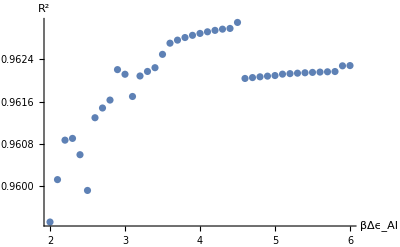

```mathematica
(* Bring the data into the form {plasmid copy number N, repressor-DNA binding energy Subscript[βΔϵ, RA], repressor copy number, fold-change} *)
fitData=Rest@brewsterData[[All,1;;3]]/.{"O1 (N=64)"->Sequence@@{64,-15.3},"O1 (N=52)"->Sequence@@{52,-15.3},"Oid (N=10)"->Sequence@@{10,-17.0}};
(* Fit data from Brewster et al. to determine the best-fit value of Subscript[βΔϵ, AI], which is represented in the code as the parameter 'βϵAI' *)
fit=Quiet@NonlinearModelFit[fitData,{foldChange[nn,R,βϵAI,ϵϵ]},{{βϵAI,4.5}},{nn,ϵϵ,R}];
Echo[fit[{"RSquared","BestFitParameters"}],"{R^2 of fit, best-fit βΔϵ_AI}: "];
(* Calculate the R^2 for many different values of Subscript[βΔϵ, AI] *)
rSquared=Table[{βϵAIvalue,NonlinearModelFit[fitData,{foldChange[n,r,βϵAI,ϵ],βϵAI==βϵAIvalue},{{βϵAI,βϵAIvalue}},{n,ϵ,r}]["RSquared"]},{βϵAIvalue,2,6,0.1}];
ListPlot[rSquared,AxesLabel->{"βΔϵ_AI","R^2"}]
```

Using the best fit value Δ,ϵ_(A,I)=4.5 k_B T, we can plot the corresponding best-fit fold-change curves on top of the Brewster et al. data.

```mathematica
(* Given the best-fit value of Subscript[βΔϵ, AI]=4.5, compute the corresponding best-fit fold-change curves *)
bestβϵAI=4.5;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,bestβϵAI,-15.3]},{10^rLog,foldChange[52,10^rLog,bestβϵAI,-15.3]},{10^rLog,foldChange[10,10^rLog,bestβϵAI,-17.]}},{rLog,0,3,0.1}];

(* Plot the results *)
labels=font[#,10]&/@{"-15.3, 64","-15.3, 52","-17.0, 10"};
leg=PointLegend[colors[[6;;4;;-1]],labels,Joined->True,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.2},LegendLabel->font["Δϵ_(R,A) (k_BT), N",10],LegendFunction->"Frame",LegendMargins->2];

plotB=Labeled[With[{opts=opts},
Show[LogLogPlot[10^10,{x,10^0,10^3},PlotLegends->Placed[leg,{Scaled[{0.05,0.26}], {0, 0.5}}],PlotRange->{{10^0,10^3},{10^-3.5,10^0.2}},FrameLabel->axesLabel4,Evaluate@opts],ListLogLogPlot[newData,Joined->True,PlotStyle->colors[[6;;4;;-1]]],ListLogLogPlot[Cases[brewsterData,{#,__}][[All,{2,3}]]&/@{"O1 (N=64)","O1 (N=52)","Oid (N=10)"},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotStyle->colors[[6;;4;;-1]]]]
],bLabel,{{Top,Left}}];
Grid[{{plotA,plotB}}]
```

-Graphics-A | -Graphics-B

#### Fixing the Δϵ_(A,I) Parameter (With Error Bars)

This section is very similar to the one above, except that in this case we will fit the data from Brewster et al. while considering the error in the fold-change measurements.

```mathematica
(* Fold-change formula from Equation (TextNumbered) for the setup from Brewster et al. *)
foldChange[n_,r_,βϵAI_,βϵGarciaDNA_]:=With[{rA=1./(1+E^-βϵAI)r,βϵRA=βϵGarciaDNA+Log[1./(1.+E^-βϵAI)],nNS=4.6 10^6.},
Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA)(n-m),{m,0.,Min[n,rA]}]/(n Sum[(rA!)/(nNS^m(rA-m)!)Binomial[n,m] E^(-m βϵRA),{m,0.,Min[n,rA]}])
]
```

First, we note that the error is given relative to the mean since the data was plotted on a log-log plot. Thus, we first convert the relative error into absolute error by computing μ (Log[μ+σ]-Log[μ]) where μ is the mean value of fold-change and σ represents the relative error. Then, we fit the data with error by assigning a weight 1/error^2 for each data point.

```mathematica
(* Bring the data into the form {plasmid copy number N, repressor-DNA binding energy Subscript[βΔϵ, RA], repressor copy number, fold-change} *)
fullFitData=Rest@brewsterData[[All]]/.{"O1 (N=64)"->Sequence@@{64,-15.3},"O1 (N=52)"->Sequence@@{52,-15.3},"Oid (N=10)"->Sequence@@{10,-17.0}};
fitData=fullFitData[[All,1;;4]];

(* Compute the absolute error of each data point *)
absoluteError=#[[4]](Log[#[[4]]+#[[6]]]-Log[#[[4]]])&/@fullFitData;
weights=1/absoluteError^2;
```

The plot below demonstrates that any value above Δ,ϵ_(A,I)≥4.5 k_B T is virtually equivalent in terms of fit quality. Care must be taken when interpreting slight deviations in the R^2 value, as this fit will be heavily dominated by the few data points that have (unrealistically) low error due to the serendipitous chance that for these data points the replicates happened to yield fold-change values very close together.

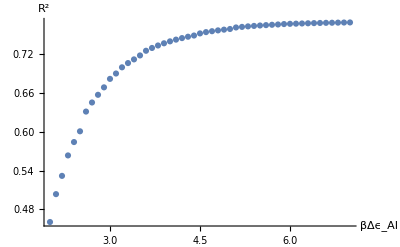

```mathematica
(* Calculate the R^2 for many different values of Subscript[βΔϵ, AI] *)
rSquared=Table[{βϵAIvalue,NonlinearModelFit[fitData,{foldChange[n,r,βϵAI,ϵ],βϵAI==βϵAIvalue},{{βϵAI,βϵAIvalue}},{n,ϵ,r},Weights->weights]["RSquared"]},{βϵAIvalue,2,7,0.1}];
ListPlot[rSquared,AxesLabel->{"βΔϵ_AI","R^2"}]
```

```mathematica
(* Load ErrorBarPlots for showing error bars *)
Needs["ErrorBarPlots`"]

(* Given the best-fit value of Subscript[βΔϵ, AI]=4.5, compute the corresponding best-fit fold-change curves *)
bestβϵAI=4.5;
newData=Transpose@Table[{{10^rLog,foldChange[64,10^rLog,bestβϵAI,-15.3]},{10^rLog,foldChange[52,10^rLog,bestβϵAI,-15.3]},{10^rLog,foldChange[10,10^rLog,bestβϵAI,-17.]}},{rLog,0,3,0.1}];

(* Plot the results *)
labels=font[#,10]&/@{"-15.3, 64","-15.3, 52","-17.0, 10"};
leg=PointLegend[colors[[6;;4;;-1]],labels,Joined->True,LegendMarkers->({Graphics[{EdgeForm[{Thickness[Medium],White}],{White,Thin,Circle[{0,0},0.1]},Disk[{0,0},0.1]}],0.03}&/@Range@4),Spacings->{0.5,0.2},LegendLabel->font["Δϵ_(R,A) (k_BT), N",10],LegendFunction->"Frame",LegendMargins->2];

(* Bring the data into the form {plasmid copy number N, repressor-DNA binding energy Subscript[βΔϵ, RA], repressor copy number, fold-change} *)
fullFitData=Rest@brewsterData[[All]]/.{"O1 (N=64)"->Sequence@@{64,-15.3},"O1 (N=52)"->Sequence@@{52,-15.3},"Oid (N=10)"->Sequence@@{10,-17.0}};
fitData=fullFitData[[All,1;;4]];

(* Compute the relative error for plotting *)
relativeError=(Log[#[[4]]+#[[6]]]-Log[#[[4]]])&/@fullFitData;
errorData=Map[Most@#&,SplitBy[{Log@#[[1]],ErrorBar[#[[2]]],#[[3]]}&/@Transpose@{fitData[[All,{3,4}]],relativeError,fitData[[All,1]]},Last],{2}];

(* Plotting *)
plotB=Labeled[With[{opts=opts},
Show[LogLogPlot[10^10,{x,10^0,10^3},PlotLegends->Placed[leg,{Scaled[{0.05,0.26}], {0, 0.5}}],PlotRange->{{10^0,10^3},{10^-3.5,10^0.2}},FrameLabel->axesLabel4,Evaluate@opts],ListLogLogPlot[newData,Joined->True,PlotStyle->colors[[6;;4;;-1]]],ErrorListPlot[errorData,PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotStyle->colors[[6;;4;;-1]],ErrorBarFunction->Function[{coords, errs}, {Line[{coords+{0,errs⟦2,1⟧},coords+{0,errs⟦2,2⟧}}]}],Method->{"OptimizePlotMarkers"->False}],ListLogLogPlot[Cases[brewsterData,{#,__}][[All,{2,3}]]&/@{"O1 (N=64)","O1 (N=52)","Oid (N=10)"},PlotMarkers->{Graphics[{EdgeForm[{Thickness[Tiny],White}],Disk[{0,0},0.1]}],0.03},PlotStyle->colors[[6;;4;;-1]]]]
],bLabel,{{Top,Left}}];
Grid[{{plotA,plotB}}]
```

-Graphics-A | -Graphics-B

### Appendix G: Calculations of Leakiness, Dynamic Range, [EC_50], and the Effective Hill Coefficient

In this section, we calculate the leakiness, dynamic range, [EC_50], and effective Hill coefficient of the fold-change Equation (TextNumbered) analytically. These expressions can be simplified into the following forms:

leakiness=(1+1/(1+ⅇ^(-βΔ,ϵ_(A,I)))R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1

dynamic range=(1+1/(1+ⅇ^(-βΔ,ϵ_(A,I))(K_A/K_I)^n)R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1-(1+1/(1+ⅇ^(-βΔ,ϵ_(A,I)))R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1

[EC_50]/K_A=(K_A/K_I-1)/(K_A/K_I-(((1+R/N_NS ⅇ^(-βΔϵ_(R,A)))+(K_A/K_I)^n (2 ⅇ^(-βΔϵ_(A,I))+(1+R/N_NS ⅇ^(-βΔϵ_(R,A)))))/(2(1+R/N_NS ⅇ^(-βΔϵ_(R,A)))+ⅇ^(-βΔϵ_(A,I))+(K_A/K_I)^n ⅇ^(-βΔϵ_(A,I))))^(1/n))-1

The [EC_50] formula is already rather cumbersome, and because the effective Hill coefficient formula

h=(2ⅆ/ⅆLog[c]Log[(fold-change(c)-leakiness)/(dynamic range-leakiness)])_(c=[EC_50])

requires you to substitute in the value of c=[EC_50], that formula will be even more monstrous. We show the full effective Hill coefficient formula below.

To make these analytic formulas more useful, we suggest making approximations based on the physical parameters to ignore irrelevant terms. For example, βΔϵ_(A,I)=4.5 implies that ⅇ^(-βΔϵ_(A,I))≪1. Similarly, depending on which operator and repressor copy numbers are under consideration, the term (1+R/N_NS ⅇ^(-βΔϵ_(R,A))) can be approximated as either 1 or R/N_NS ⅇ^(-βΔϵ_(R,A)).

```mathematica
$Assumptions=0<KI<KA&&0<βϵAI&&βϵRA<0&&0<Nns&&0<R&&n∈Integers&&n>0;
(* Leakiness *)
leakiness=Echo[Limit[(1+(1+c/KA)^n/((1+c/KA)^n+E^-βϵAI(1+c/KI)^n)R/Nns E^-βϵRA)^-1,c->0],"Leakiness: "];
(* Dynamic Range *)
dynamicRange=Echo[FullSimplify[Limit[(1+(1+c/KA)^n/((1+c/KA)^n+E^-βϵAI(1+c/KI)^n)R/Nns E^-βϵRA)^-1,c->∞]],"Dynamic Range: "];
(* [Subscript[EC, 50]] *)
EC50=Echo[c/.FullSimplify@First@Quiet@Solve[(1+(1+c/KA)^n/((1+c/KA)^n+E^-βϵAI(1+c/KI)^n)R/Nns E^-βϵRA)^-1==(leakiness+dynamicRange)/2,c],"[EC_50]: "];
(* Effective Hill Coefficient *)
h=Echo[Simplify[2 c D[(1+(1+c/KA)^n/((1+c/KA)^n+E^-βϵAI(1+c/KI)^n)R/Nns E^-βϵRA)^-1,c]/.c->EC50],"Effective Hill Coefficient: "];
```

Leakiness:  (ⅇ^βϵRA (1+ⅇ^βϵAI) Nns)/(ⅇ^βϵRA Nns+ⅇ^(βϵAI+βϵRA) Nns+ⅇ^βϵAI R)

Dynamic Range:  (ⅇ^βϵRA (KA^n+ⅇ^βϵAI KI^n) Nns)/(ⅇ^βϵRA KA^n Nns+ⅇ^βϵAI KI^n (ⅇ^βϵRA Nns+R))

[EC_50]:  KI (-1+(-KA+KI)/(KI-ⅇ^((2 ⅈ π)/n) KA ((2 ⅇ^βϵRA KA^n Nns+ⅇ^(βϵAI+βϵRA) (KA^n+KI^n) Nns+ⅇ^βϵAI (KA^n+KI^n) R)/(ⅇ^βϵRA KA^n Nns+KI^n (ⅇ^βϵRA Nns+2 ⅇ^βϵAI (ⅇ^βϵRA Nns+R))))^(-1/n)))

Effective Hill Coefficient:  -((ⅇ^(-(2 ⅈ π)/n+βϵAI+βϵRA) n Nns R (2 ⅇ^(βϵAI+βϵRA) KI^n Nns+ⅇ^βϵRA (KA^n+KI^n) Nns+2 ⅇ^βϵAI KI^n R) (2 ⅇ^βϵRA KA^n Nns+ⅇ^(βϵAI+βϵRA) (KA^n+KI^n) Nns+ⅇ^βϵAI (KA^n+KI^n) R)^((-1+n)/n) (ⅇ^βϵRA KA^n Nns+KI^n (ⅇ^βϵRA Nns+2 ⅇ^βϵAI (ⅇ^βϵRA Nns+R)))^(1/n) (ⅇ^((2 ⅈ π)/n)-((2 ⅇ^βϵRA KA^n Nns+ⅇ^(βϵAI+βϵRA) (KA^n+KI^n) Nns+ⅇ^βϵAI (KA^n+KI^n) R)/(ⅇ^βϵRA KA^n Nns+KI^n (ⅇ^βϵRA Nns+2 ⅇ^βϵAI (ⅇ^βϵRA Nns+R))))^(1/n)) (ⅇ^((2 ⅈ π)/n) KA-KI ((2 ⅇ^βϵRA KA^n Nns+ⅇ^(βϵAI+βϵRA) (KA^n+KI^n) Nns+ⅇ^βϵAI (KA^n+KI^n) R)/(ⅇ^βϵRA KA^n Nns+KI^n (ⅇ^βϵRA Nns+2 ⅇ^βϵAI (ⅇ^βϵRA Nns+R))))^(1/n)))/(2 (KA-KI) (ⅇ^βϵRA Nns+ⅇ^(βϵAI+βϵRA) Nns+ⅇ^βϵAI R)^2 (ⅇ^βϵRA KA^n Nns+ⅇ^(βϵAI+βϵRA) KI^n Nns+ⅇ^βϵAI KI^n R)^2))

## Markov chain Monte Carlo (MCMC)

In this section, we use Josh Burkart’s Mathematica MCMC implementation to determine the values of K_A and K_I using data from the O2 strain with R=260 repressors/cell. This package named mcmc.m is included in the same directory within the GitHub as this notebook. We note that this implementation is slightly different from the emcee package used in the Python analysis of this data, but the results will be nearly identical.

### MCMC Setup

#### Defining the MCMC

The initial guesses for the K_A and K_I parameters will come from the best-fit parameters of nonlinear fitting. As discussed on the paper website, for numerical stability we fit the parameters (k̃)_A=-Log[K_A/c_0] and (k̃)_I=-Log[K_I/c_0] where c_0=1M is a reference concentration. Thus the fold-change takes the form

fold-change=(1+((1+c/c_0 ⅇ^((k̃)_A))^n)/((1+c/c_0 ⅇ^((k̃)_A))^n+(ⅇ^(-βΔ,ϵ_(A,I))(1+c/c_0 ⅇ^((k̃)_I)))^n)R/N_NS ⅇ^(-βΔ,ϵ_(R,A)))^-1

```mathematica
(* Load the data from the O2 strain with R=260. Data in format {"IPTG (M)","fold-change"}*)
O2R260data=Cases[inductionData[[All,{1,3,4,5}]],{"O2",260,__}][[All,{3,4}]];
(* Use nonlinear fitting to get a first guess of the Subscript[K, A] and Subscript[K, I] parameters *)
initalValuesMCMC=With[{(* Known parameter values *)
ΔϵAI=4.5,Nns=4.6 10^6,ΔϵRA=-13.9,R=260},
NonlinearModelFit[O2R260data,(1+((1+c E^ka)^2)/((1+c E^ka)^2+E^-ΔϵAI(1+c E^ki)^2)R/Nns E^-ΔϵRA)^-1,{{ka,-Log[141 10^-6.]},{ki,-Log[0.56 10^-6]}},{c}]
];
```

Using Bayes’ Theorem, the posterior probability distribution of the unknown parameters is given by

P[(k̃)_A,(k̃)_I,σ|D,I]=(P[D|(k̃)_A,(k̃)_I,σ,I]P[(k̃)_A,(k̃)_I,σ|I])/P[D|I]

We assume Jeffry’s priors for K_A and K_I (which translates into uniform priors for (k̃)_A and (k̃)_I). We further assume that the error in the experimental measurements is independent and Gaussian with a standard deviation σ, and we assume that σ obeys a Jeffrey’s prior. Thus we can write the prior as

P[(k̃)_A,(k̃)_I,σ|I]=1/((k̃)_A_max-(k̃)_A_min)1/((k̃)_I_max-(k̃)_I_min)1/(σ Log[σ_max/σ_min])

With our assumption of Gaussian error, the posterior is given by

P[D|(k̃)_A,(k̃)_I,σ,I]=1/((2π σ^2)^(n/2))Π_(j=1)^n Exp[-((fc_exp^(i)-fc_theory[(k̃)_A,(k̃)_I,R^(j),Δϵ_RA^(j),c^(j)])^2)/(2 σ^2)]

Finally, the denominator P[D|I] in Equation (TextNumbered) serves as a normalization constant. We will opt to drop this constant for now and normalize the resulting distribution at the end. Combining all terms, the posterior probability distribution becomes

P[(k̃)_A,(k̃)_I,σ|D,I]∝(1/((2π σ^2)^(n/2))Π_(j=1)^n Exp[-((fc_exp^(i)-fc_theory[(k̃)_A,(k̃)_I,R^(j),Δϵ_RA^(j),c^(j)])^2)/(2 σ^2)])(1/((k̃)_A_max-(k̃)_A_min)1/((k̃)_I_max-(k̃)_I_min)1/(σ Log[σ_max/σ_min]))

For numerical stability, MCMC algorithms always compute using the log of the posterior probability distribution. We use this opportunity to throw away all of the terms in the second parenthesis of Equation (TextNumbered) save 1/σ. In doing this, we are implicitly assuming that the range of (k̃)_A, (k̃)_I, and σ will be sufficiently large to capture the true values of these parameters. The MCMC code below will assume that the range of (k̃)_A and (k̃)_I is infinitely large, which certainly satisfies this assumption. We will also assume that σ∈[0.045,0.075] and find that the resulting distribution of σ lies well within this range (additionally, one can increase the range of σ without changing the results of the MCMC). We now return to the log posterior probability distribution and code it in Mathematica.

Log[P[(k̃)_A,(k̃)_I,σ|D,I]]∝-(n+1)Log[σ]-Σ_(j=1)^n((fc_exp^(i)-fc_theory[(k̃)_A,(k̃)_I,R^(j),Δϵ_RA^(j),c^(j)])^2)/(2 σ^2)

```mathematica
(* Import mcmc.m file, assuming it is in the same directory as this notebook *)
Get[FileNameJoin[{NotebookDirectory[],"mcmc.m"}]];

(* Define the theoretical fold-change function, given by Equation (5) in the paper *)
fc[c_]:=With[{(* Known parameter values for the O2 strain with R=260 repressors/cell *)
ΔϵAI=4.5,Nns=4.6 10^6,ΔϵRA=-13.9,R=260},
(1+((1+c E^ka)^2)/((1+c E^ka)^2+E^-ΔϵAI(1+c E^ki)^2)R/Nns E^-ΔϵRA)^-1
]
(* Number of data points *)
n=Length@O2R260data;
(* Log posterior probability distribution *)
probLog=-(n+1)Log[σ]-Sum[(O2R260data[[j,-1]]-fc[O2R260data[[j,-2]]])^2/(2 σ^2),{j,n}];
(* Initial guesses for the Subscript[k̃, A] and Subscript[k̃, I] parameters *)
{kaInitial,kiInitial}={ka,ki}/.initalValuesMCMC["BestFitParameters"];
(* Restrict the values of σ to the following discrete (but very fine) range *)
σRange=Range[0.045,0.075,0.0001];
```

#### Running the MCMC

Because this MCMC implementation runs a single walker, we will use a very long walk of 100,000 steps. The format for each parameter argument is {paramater, initialValue, spread, domain} where

initialValue is the initial guess of the parameter (taken from the nonlinear fitting results)

spread roughly represents the change in the parameter value for each step of the Markov chain. This routine selects new parameters values based on an exponential distribution of the form ⅇ^(Δparamater/spread)

domain is either Reals or a uniform grid of all possible values for the parameter

```mathematica
mcmc=MCMC[probLog,{{ka,kaInitial,0.05,Reals},{ki,kiInitial,0.05,Reals},{σ,0.1,0.02,σRange}},100000,"BurnFraction"->0.05];
(* Properties of the resulting MCMC *)
mcmc[{"BestFitParameters","ParameterErrors","AverageAcceptance","TimeSpent","NumSteps","Parameters","ProposalSpreads","BurnFraction","BurnEnd","CorrelationMatrix"}]
```

{BestFitParameters→{ka→8.86301,ki→14.4314,σ→0.0557803},ParameterErrors→{ka→0.092164,ki→0.0392406,σ→0.00345475},AverageAcceptance→0.166338,TimeSpent→137.333884 Second,NumSteps→100000,Parameters→{ka,ki,σ},ProposalSpreads→{0.05,0.05,200.},BurnFraction→0.05,BurnEnd→5000,CorrelationMatrix→(1. | 0.891797 | -0.0215612
0.891797 | 1. | -0.014889
-0.0215612 | -0.014889 | 1.)}

### Analyzing the MCMC

#### Parameter Values

We report the values of (k̃)_A, (k̃)_I, and σ over the MCMC walk. For clarity, we return to the original parameters of interest K_A=c_0 ⅇ^(-(k̃)_A), K_I=c_0 ⅇ^(-(k̃)_I), and σ, where c_0=1M.

```mathematica
(* Labels for the three parameters *)
fullParameterLabels=font[#,14]&/@{"K_A"," K_I"," σ"};
(* Values of Subscript[k̃, A], Subscript[k̃, I],and σ, ignoring the burn-in *)
parameterDistributionData=mcmc["ParameterRun"][[mcmc["BurnEnd"];;]];

(* Find the 95% credible region by adding the histogram bins in order from greatest to least until you reach 95% *)
credibleRegion[parameterIndex_]:=(
credibleCutoff=0.95;
bins=HistogramList[Transpose[parameterDistributionData][[parameterIndex]],{0.01},"Probability"];
(* Find the threshold above which 95% of the parameter probability exists *)
binsOrdered=Reverse@Sort@bins[[2]];
index=First@FirstPosition[Accumulate@binsOrdered,f_/;f>credibleCutoff];
threshold=binsOrdered[[index]];
(* Find the bounds of the credible region *)
credibleBounds=MinMax@bins[[1,Flatten@Position[bins[[2]],f_/;f>threshold]]];
(* Print the corresponding bounds of the Subscript[K, A] and Subscript[K, I] parameters *)
bestFitValue=mcmc["BestFitParameters"][[parameterIndex,2]];
Row[{fullParameterLabels[[parameterIndex]],": ",Subsuperscript[ToString@#[[1]],ToString@#[[2]],"+"<>ToString@#[[3]]]," μM"}]&@Round[(10^6{E^-bestFitValue,E^(-credibleBounds[[2]])-E^-bestFitValue,E^(-credibleBounds[[1]])-E^-bestFitValue}),10^-3.]
)
(* Credible region for the σ error parameter *)
errorParameter=Row[{"  ",fullParameterLabels[[3]],": ",Round[mcmc["BestFitParameters"][[-1,2]],10^-3.]}];
(* Summary of the results *)
Panel[Column[Style[#,FontSize->14,RGBColor[0.7725490196078432, 0.16078431372549018, 0.13333333333333333],FontFamily->"Times"]&/@{credibleRegion[1],credibleRegion[2],errorParameter}],ImageSize->{Full,Automatic},Alignment->Center,Appearance->"Frameless",Background->White]
```

K_A: 141.528_-21.765^(+28.423) μM
 K_I: 0.54_-0.036^(+0.04) μM
   σ: 0.056

We note that these values are nearly identical to those reported in the paper (shown below), which were found using the Python emcee package:

K_A:139.59_-22.64^(+28.20)μM
K_I:0.53_-0.040^(+0.043)μM
σ:0.055

#### Corner Plots

A way to quickly visualize the results of an MCMC is to show the projections of its different parameters, analogous to the Python corner plot package.

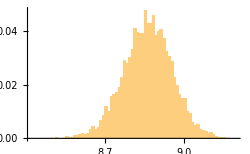
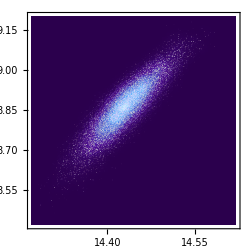
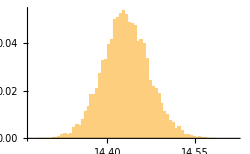
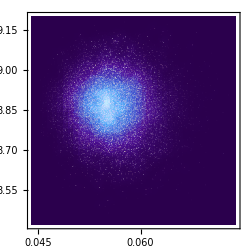
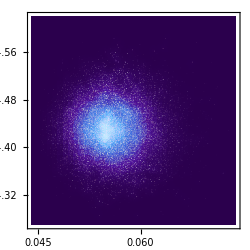
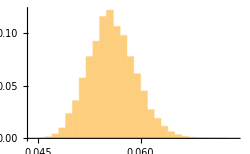
| -Graphics- |  | 
(k̃)_I | -Graphics- | -Graphics- | 
σ | -Graphics- | -Graphics- | -Graphics-
 | (k̃)_A | (k̃)_I | σ

```mathematica
(* Values of Subscript[k̃, A], Subscript[k̃, I],and σ, ignoring the burn-in *)
parameterDistributionData=mcmc["ParameterRun"][[mcmc["BurnEnd"];;]];

(* Making Histograms *)
plotRange={{8.42,9.2},{14.27,14.62},{0.044,0.074}};
binWidth={{0.01},{0.005},{0.001}};
(* Maginalized distributions of individual parameters *)
hist[j_]:=Histogram[Transpose[parameterDistributionData][[j]],binWidth[[j]],"Probability",PlotRange->{plotRange[[j]],Automatic},ImageSize->250];
corner[j_,j_]:=hist[j]
corner[j_,k_/;k>j]:=Null
(* Correlation between two different parameters *)
corner[j_,k_]:=Show[SmoothDensityHistogram[parameterDistributionData[[All,{j,k}]],Mesh->4,PlotRange->{plotRange[[j]],plotRange[[k]]},ColorFunction->"DeepSeaColors",ImageSize->250],ListPlot[parameterDistributionData[[All,{j,k}]],PlotStyle->{White,Opacity[0.03]}]]

(* Plotting *)
labels=Style[#,FontSize->20,FontFamily->"Times",Bold,RGBColor[Rational[2, 3], 0.33333333333333337, 0]]&/@{"(k̃)_A","(k̃)_I","σ"};
plots=Table[corner[j,k],{j,1,3},{k,1,3}];
Grid[Append[Transpose@Prepend[Transpose@plots,ReplacePart[labels,1->" "]],Prepend[labels,""]]]
```

## Initialization

#### Induction Data

Induction data in the form {operator, binding energy (k_B T units), repressors/cell, IPTG (M), fold-change}. There are a few minor differences between this data and that found on the GitHub repository:

IPTG concentration here is expressed in Molar, whereas on the GitHub repository it is expressed in μM

The repressors/cell shown here denotes R, the number of Lac repressor dimers in the cell (following the paper's notation). In the GitHub repository, the repressor copy number represents the number of Lac repressor tetramers that are natively expressed in the cell (i.e. half the value shown here)

This data is first used in Figure 5.

```mathematica
inductionData={{"operator","binding energy (k_BT units)","repressors/cell","IPTG (M)","fold-change"},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00714631523096},{"O2",-13.9,1220,0.,0.00684677147324},{"O2",-13.9,260,0.,0.0130591233153},{"O2",-13.9,124,0.,0.0218525396595},{"O2",-13.9,60,0.,0.0419880028037},{"O2",-13.9,22,0.,0.171314836665},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00548639850507},{"O2",-13.9,1220,1.*^-7,0.00828194170052},{"O2",-13.9,260,1.*^-7,0.00869911418906},{"O2",-13.9,124,1.*^-7,0.0229894179228},{"O2",-13.9,60,1.*^-7,0.0436287887782},{"O2",-13.9,22,1.*^-7,0.170253452941},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0106515830755},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0144091598672},{"O2",-13.9,260,4.9999999999999996*^-6,0.0457685717625},{"O2",-13.9,124,4.9999999999999996*^-6,0.0898861439469},{"O2",-13.9,60,4.9999999999999996*^-6,0.153229124862},{"O2",-13.9,22,4.9999999999999996*^-6,0.398560119514},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0263318129177},{"O2",-13.9,1220,9.999999999999999*^-6,0.0361204599457},{"O2",-13.9,260,9.999999999999999*^-6,0.11115082527},{"O2",-13.9,124,9.999999999999999*^-6,0.171585510018},{"O2",-13.9,60,9.999999999999999*^-6,0.220264179218},{"O2",-13.9,22,9.999999999999999*^-6,0.526678905359},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0645066444831},{"O2",-13.9,1220,0.000024999999999999998,0.121197346217},{"O2",-13.9,260,0.000024999999999999998,0.334437227468},{"O2",-13.9,124,0.000024999999999999998,0.492073798927},{"O2",-13.9,60,0.000024999999999999998,0.529756083667},{"O2",-13.9,22,0.000024999999999999998,0.90755841088},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.160726959751},{"O2",-13.9,1220,0.000049999999999999996,0.20631783958},{"O2",-13.9,260,0.000049999999999999996,0.518623540951},{"O2",-13.9,124,0.000049999999999999996,0.68350330161},{"O2",-13.9,60,0.000049999999999999996,0.706763615984},{"O2",-13.9,22,0.000049999999999999996,0.977111464812},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.112833049941},{"O2",-13.9,1220,0.000075,0.286389224044},{"O2",-13.9,260,0.000075,0.657032320063},{"O2",-13.9,124,0.000075,0.846586881562},{"O2",-13.9,60,0.000075,0.899766920475},{"O2",-13.9,22,0.000075,1.01666021857},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.14993431695},{"O2",-13.9,1220,0.00009999999999999999,0.271793683843},{"O2",-13.9,260,0.00009999999999999999,0.742593517576},{"O2",-13.9,124,0.00009999999999999999,0.857932718582},{"O2",-13.9,60,0.00009999999999999999,0.935425385001},{"O2",-13.9,22,0.00009999999999999999,0.993062999137},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.560148630916},{"O2",-13.9,1220,0.0005,0.656186880324},{"O2",-13.9,260,0.0005,0.936247153816},{"O2",-13.9,124,0.0005,0.991263406657},{"O2",-13.9,60,0.0005,0.980171487206},{"O2",-13.9,22,0.0005,1.03088317257},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.772189588103},{"O2",-13.9,1220,0.001,0.718067738024},{"O2",-13.9,260,0.001,0.909398549454},{"O2",-13.9,124,0.001,0.968878535609},{"O2",-13.9,60,0.001,0.977465064514},{"O2",-13.9,22,0.001,1.045953029},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.725383432702},{"O2",-13.9,1220,0.005,0.741041409861},{"O2",-13.9,260,0.005,0.968663129353},{"O2",-13.9,124,0.005,1.00187398546},{"O2",-13.9,60,0.005,0.985034576506},{"O2",-13.9,22,0.005,1.05404762117},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00753763431899},{"O2",-13.9,1220,0.,0.00784867602071},{"O2",-13.9,260,0.,0.0148466802302},{"O2",-13.9,124,0.,0.0302158309415},{"O2",-13.9,60,0.,0.052411006895},{"O2",-13.9,22,0.,0.180618855461},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00392054668013},{"O2",-13.9,1220,1.*^-7,0.00508514488127},{"O2",-13.9,260,1.*^-7,0.0165369238003},{"O2",-13.9,124,1.*^-7,0.0300404651659},{"O2",-13.9,60,1.*^-7,0.0511801444569},{"O2",-13.9,22,1.*^-7,0.180291110291},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.00993408425075},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0132469310589},{"O2",-13.9,260,4.9999999999999996*^-6,0.0365964945742},{"O2",-13.9,124,4.9999999999999996*^-6,0.0691079820658},{"O2",-13.9,60,4.9999999999999996*^-6,0.12190041964},{"O2",-13.9,22,4.9999999999999996*^-6,0.430914942032},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0116827310716},{"O2",-13.9,1220,9.999999999999999*^-6,0.0220767979519},{"O2",-13.9,260,9.999999999999999*^-6,0.0927236519928},{"O2",-13.9,124,9.999999999999999*^-6,0.17507023234},{"O2",-13.9,60,9.999999999999999*^-6,0.271428523878},{"O2",-13.9,22,9.999999999999999*^-6,0.734049658011},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0367580327767},{"O2",-13.9,1220,0.000024999999999999998,0.058915479311},{"O2",-13.9,260,0.000024999999999999998,0.212471869473},{"O2",-13.9,124,0.000024999999999999998,0.418684640546},{"O2",-13.9,60,0.000024999999999999998,0.552109873589},{"O2",-13.9,22,0.000024999999999999998,0.992898798061},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.070172671526},{"O2",-13.9,1220,0.000049999999999999996,0.142929409875},{"O2",-13.9,260,0.000049999999999999996,0.486983171144},{"O2",-13.9,124,0.000049999999999999996,0.654088070904},{"O2",-13.9,60,0.000049999999999999996,0.77322746555},{"O2",-13.9,22,0.000049999999999999996,0.953512172762},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.109916078325},{"O2",-13.9,1220,0.000075,0.203123017487},{"O2",-13.9,260,0.000075,0.613530098102},{"O2",-13.9,124,0.000075,0.806364455574},{"O2",-13.9,60,0.000075,0.887951923795},{"O2",-13.9,22,0.000075,0.996588618496},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.24026229177},{"O2",-13.9,1220,0.00009999999999999999,0.408628944212},{"O2",-13.9,260,0.00009999999999999999,0.728194784079},{"O2",-13.9,124,0.00009999999999999999,0.861946852219},{"O2",-13.9,60,0.00009999999999999999,0.911694715425},{"O2",-13.9,22,0.00009999999999999999,0.993432947164},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.54848937416},{"O2",-13.9,1220,0.00025,0.624479144156},{"O2",-13.9,260,0.00025,0.860369756428},{"O2",-13.9,124,0.00025,0.912871053164},{"O2",-13.9,60,0.00025,0.9385363658},{"O2",-13.9,22,0.00025,0.998883033485},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.644256103195},{"O2",-13.9,1220,0.0005,0.763804706422},{"O2",-13.9,260,0.0005,0.974827340827},{"O2",-13.9,124,0.0005,0.976211702447},{"O2",-13.9,60,0.0005,0.969939894176},{"O2",-13.9,22,0.0005,1.12571487032},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.682698576314},{"O2",-13.9,1220,0.001,0.69030173152},{"O2",-13.9,260,0.001,0.952114312366},{"O2",-13.9,124,0.001,1.02658289455},{"O2",-13.9,60,0.001,1.05620094983},{"O2",-13.9,22,0.001,1.0783102894},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.812214747077},{"O2",-13.9,1220,0.005,0.816322117267},{"O2",-13.9,260,0.005,0.909622798488},{"O2",-13.9,124,0.005,0.963225437051},{"O2",-13.9,60,0.005,0.984831601017},{"O2",-13.9,22,0.005,0.985323075169},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00953843184702},{"O2",-13.9,1220,0.,0.00309134218574},{"O2",-13.9,260,0.,0.0136895997035},{"O2",-13.9,124,0.,0.0296465638972},{"O2",-13.9,60,0.,0.0399135513062},{"O2",-13.9,22,0.,0.168342170863},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00601775745036},{"O2",-13.9,1220,1.*^-7,0.00453174174457},{"O2",-13.9,260,1.*^-7,0.0148741425602},{"O2",-13.9,124,1.*^-7,0.0289369831764},{"O2",-13.9,60,1.*^-7,0.0411582146451},{"O2",-13.9,22,1.*^-7,0.164757500771},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0198834246711},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0241128950952},{"O2",-13.9,260,4.9999999999999996*^-6,0.0714025295552},{"O2",-13.9,124,4.9999999999999996*^-6,0.102643409464},{"O2",-13.9,60,4.9999999999999996*^-6,0.111640999642},{"O2",-13.9,22,4.9999999999999996*^-6,0.287593304233},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0126200590053},{"O2",-13.9,1220,9.999999999999999*^-6,0.022427589752},{"O2",-13.9,260,9.999999999999999*^-6,0.0825550310209},{"O2",-13.9,124,9.999999999999999*^-6,0.150871668438},{"O2",-13.9,60,9.999999999999999*^-6,0.225054734361},{"O2",-13.9,22,9.999999999999999*^-6,0.599296698628},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0427273032932},{"O2",-13.9,1220,0.000024999999999999998,0.0733112306758},{"O2",-13.9,260,0.000024999999999999998,0.302731966139},{"O2",-13.9,124,0.000024999999999999998,0.462874043495},{"O2",-13.9,60,0.000024999999999999998,0.511120513006},{"O2",-13.9,22,0.000024999999999999998,1.00025001575},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.13839005187},{"O2",-13.9,1220,0.000049999999999999996,0.210497414126},{"O2",-13.9,260,0.000049999999999999996,0.474771148477},{"O2",-13.9,124,0.000049999999999999996,0.572627145239},{"O2",-13.9,60,0.000049999999999999996,0.685236078725},{"O2",-13.9,22,0.000049999999999999996,0.998241817761},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.174515492647},{"O2",-13.9,1220,0.000075,0.284357340411},{"O2",-13.9,260,0.000075,0.639589037643},{"O2",-13.9,124,0.000075,0.74512393915},{"O2",-13.9,60,0.000075,0.751639204679},{"O2",-13.9,22,0.000075,1.0221605803},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.271961659513},{"O2",-13.9,1220,0.00009999999999999999,0.419902521416},{"O2",-13.9,260,0.00009999999999999999,0.796314031868},{"O2",-13.9,124,0.00009999999999999999,0.847604794377},{"O2",-13.9,60,0.00009999999999999999,0.917224333755},{"O2",-13.9,22,0.00009999999999999999,1.05167274031},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.375941914844},{"O2",-13.9,1220,0.00025,0.531282199346},{"O2",-13.9,260,0.00025,0.848775866223},{"O2",-13.9,124,0.00025,0.863261050618},{"O2",-13.9,60,0.00025,0.965512041914},{"O2",-13.9,22,0.00025,1.03684455827},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.622808354448},{"O2",-13.9,1220,0.0005,0.691293285509},{"O2",-13.9,260,0.0005,0.870078813439},{"O2",-13.9,124,0.0005,0.873702474323},{"O2",-13.9,60,0.0005,0.939682094457},{"O2",-13.9,22,0.0005,1.00290278603},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.704111471213},{"O2",-13.9,1220,0.001,0.739159702352},{"O2",-13.9,260,0.001,0.898935492422},{"O2",-13.9,124,0.001,0.914040018823},{"O2",-13.9,60,0.001,0.960663402881},{"O2",-13.9,22,0.001,1.01159773684},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.669035682885},{"O2",-13.9,1220,0.005,0.704629601224},{"O2",-13.9,260,0.005,0.847142895607},{"O2",-13.9,124,0.005,0.914499245772},{"O2",-13.9,60,0.005,0.97984498201},{"O2",-13.9,22,0.005,1.07730509281},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00344916329128},{"O2",-13.9,1220,0.,0.00669904223372},{"O2",-13.9,260,0.,0.0147430988208},{"O2",-13.9,124,0.,0.0274005979889},{"O2",-13.9,60,0.,0.0452906369149},{"O2",-13.9,22,0.,0.176945784651},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00266477153196},{"O2",-13.9,1220,1.*^-7,0.00440430731855},{"O2",-13.9,260,1.*^-7,0.015667271628},{"O2",-13.9,124,1.*^-7,0.0227241365734},{"O2",-13.9,60,1.*^-7,0.287876186346},{"O2",-13.9,22,1.*^-7,0.18116116494},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0116395530997},{"O2",-13.9,1220,4.9999999999999996*^-6,0.00980717386885},{"O2",-13.9,260,4.9999999999999996*^-6,0.0459090365936},{"O2",-13.9,124,4.9999999999999996*^-6,0.125537691205},{"O2",-13.9,60,4.9999999999999996*^-6,0.215926225132},{"O2",-13.9,22,4.9999999999999996*^-6,0.529720887019},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.020642844826},{"O2",-13.9,1220,9.999999999999999*^-6,0.0228656643888},{"O2",-13.9,260,9.999999999999999*^-6,0.07296456697},{"O2",-13.9,124,9.999999999999999*^-6,0.179770501238},{"O2",-13.9,60,9.999999999999999*^-6,0.265079621742},{"O2",-13.9,22,9.999999999999999*^-6,0.721789994429},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0473621515754},{"O2",-13.9,1220,0.000024999999999999998,0.0527334019105},{"O2",-13.9,260,0.000024999999999999998,0.14499256407},{"O2",-13.9,124,0.000024999999999999998,0.309663471309},{"O2",-13.9,60,0.000024999999999999998,0.469270035164},{"O2",-13.9,22,0.000024999999999999998,0.940897357278},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.106568767803},{"O2",-13.9,1220,0.000049999999999999996,0.179343480721},{"O2",-13.9,260,0.000049999999999999996,0.497495852522},{"O2",-13.9,124,0.000049999999999999996,0.730886058437},{"O2",-13.9,60,0.000049999999999999996,0.777456479585},{"O2",-13.9,22,0.000049999999999999996,0.918405761081},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.192756481813},{"O2",-13.9,1220,0.000075,0.231267808977},{"O2",-13.9,260,0.000075,0.613594460372},{"O2",-13.9,124,0.000075,0.814784520242},{"O2",-13.9,60,0.000075,0.861618549016},{"O2",-13.9,22,0.000075,0.994349336178},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.24799908229},{"O2",-13.9,1220,0.00009999999999999999,0.337196273727},{"O2",-13.9,260,0.00009999999999999999,0.664821622858},{"O2",-13.9,124,0.00009999999999999999,0.855379276651},{"O2",-13.9,60,0.00009999999999999999,0.930280990939},{"O2",-13.9,22,0.00009999999999999999,0.991714257231},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.4657421714},{"O2",-13.9,1220,0.00025,0.57303118703},{"O2",-13.9,260,0.00025,0.880253190148},{"O2",-13.9,124,0.00025,0.936503302693},{"O2",-13.9,60,0.00025,0.945154164828},{"O2",-13.9,22,0.00025,0.9988265937},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.503860183138},{"O2",-13.9,1220,0.0005,0.582255330819},{"O2",-13.9,260,0.0005,0.883840149413},{"O2",-13.9,124,0.0005,0.949511747642},{"O2",-13.9,60,0.0005,0.957425736468},{"O2",-13.9,22,0.0005,1.00636257544},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.590315974063},{"O2",-13.9,1220,0.001,0.680109437082},{"O2",-13.9,260,0.001,0.894270203863},{"O2",-13.9,124,0.001,0.935511099709},{"O2",-13.9,60,0.001,0.9482587373},{"O2",-13.9,22,0.001,0.992074408111},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00655349466724},{"O2",-13.9,1220,0.,0.00346465498587},{"O2",-13.9,260,0.,0.0109531528937},{"O2",-13.9,124,0.,0.0238056537179},{"O2",-13.9,60,0.,0.0451776217229},{"O2",-13.9,22,0.,0.181434949979},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00369363796067},{"O2",-13.9,1220,1.*^-7,0.00513983886671},{"O2",-13.9,260,1.*^-7,0.0133292678085},{"O2",-13.9,124,1.*^-7,0.0273408389544},{"O2",-13.9,60,1.*^-7,0.0510013955672},{"O2",-13.9,22,1.*^-7,0.179568757694},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0119584907058},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0116575631865},{"O2",-13.9,260,4.9999999999999996*^-6,0.0468030326595},{"O2",-13.9,124,4.9999999999999996*^-6,0.110564672068},{"O2",-13.9,60,4.9999999999999996*^-6,0.193413284443},{"O2",-13.9,22,4.9999999999999996*^-6,0.537791765712},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.00810990379533},{"O2",-13.9,1220,9.999999999999999*^-6,0.0245778229},{"O2",-13.9,260,9.999999999999999*^-6,0.0827843853706},{"O2",-13.9,124,9.999999999999999*^-6,0.219786729618},{"O2",-13.9,60,9.999999999999999*^-6,0.373821335758},{"O2",-13.9,22,9.999999999999999*^-6,0.909485942688},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0350240578555},{"O2",-13.9,1220,0.000024999999999999998,0.0560756830896},{"O2",-13.9,260,0.000024999999999999998,0.217032648137},{"O2",-13.9,124,0.000024999999999999998,0.449543142515},{"O2",-13.9,60,0.000024999999999999998,0.629943379321},{"O2",-13.9,22,0.000024999999999999998,0.985187295303},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.107111211476},{"O2",-13.9,1220,0.000049999999999999996,0.179317769018},{"O2",-13.9,260,0.000049999999999999996,0.485828973796},{"O2",-13.9,124,0.000049999999999999996,0.675773304089},{"O2",-13.9,60,0.000049999999999999996,0.782111497421},{"O2",-13.9,22,0.000049999999999999996,0.990763946047},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.116468587529},{"O2",-13.9,1220,0.000075,0.180952297915},{"O2",-13.9,260,0.000075,0.574322874356},{"O2",-13.9,124,0.000075,0.802592489067},{"O2",-13.9,60,0.000075,0.904363573407},{"O2",-13.9,22,0.000075,1.00604239694},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.176889368237},{"O2",-13.9,1220,0.00009999999999999999,0.331963391691},{"O2",-13.9,260,0.00009999999999999999,0.756156338753},{"O2",-13.9,124,0.00009999999999999999,0.868028279401},{"O2",-13.9,60,0.00009999999999999999,0.925174030419},{"O2",-13.9,22,0.00009999999999999999,0.979269321095},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.386808561181},{"O2",-13.9,1220,0.00025,0.498036776477},{"O2",-13.9,260,0.00025,0.822560355165},{"O2",-13.9,124,0.00025,0.934812084243},{"O2",-13.9,60,0.00025,0.931695256718},{"O2",-13.9,22,0.00025,1.0288444309},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.54549477423},{"O2",-13.9,1220,0.0005,0.618590202994},{"O2",-13.9,260,0.0005,0.894112430394},{"O2",-13.9,124,0.0005,0.935602733629},{"O2",-13.9,60,0.0005,0.956282379542},{"O2",-13.9,22,0.0005,1.01552136124},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.6883127687},{"O2",-13.9,1220,0.001,0.718811256152},{"O2",-13.9,260,0.001,0.923903101846},{"O2",-13.9,124,0.001,0.952110208309},{"O2",-13.9,60,0.001,0.970025762696},{"O2",-13.9,22,0.001,0.986239910047},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.877528617761},{"O2",-13.9,1220,0.005,0.849443240857},{"O2",-13.9,260,0.005,0.973318573946},{"O2",-13.9,124,0.005,0.963621278099},{"O2",-13.9,60,0.005,0.941919000288},{"O2",-13.9,22,0.005,0.993245108952},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00484638747334},{"O2",-13.9,1220,0.,0.0047170255448},{"O2",-13.9,260,0.,0.0150842794494},{"O2",-13.9,124,0.,0.0309909508589},{"O2",-13.9,60,0.,0.0411100872442},{"O2",-13.9,22,0.,0.171976913404},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00762112619528},{"O2",-13.9,1220,1.*^-7,0.00539305680404},{"O2",-13.9,260,1.*^-7,0.0132177432071},{"O2",-13.9,124,1.*^-7,0.0347048373791},{"O2",-13.9,60,1.*^-7,0.0460877460557},{"O2",-13.9,22,1.*^-7,0.170259961173},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0066037633908},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0131813461855},{"O2",-13.9,260,4.9999999999999996*^-6,0.0271222269888},{"O2",-13.9,124,4.9999999999999996*^-6,0.06349587651},{"O2",-13.9,60,4.9999999999999996*^-6,0.095320457887},{"O2",-13.9,22,4.9999999999999996*^-6,0.369194845897},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0167001024752},{"O2",-13.9,1220,9.999999999999999*^-6,0.0183820368726},{"O2",-13.9,260,9.999999999999999*^-6,0.0521287722112},{"O2",-13.9,124,9.999999999999999*^-6,0.137399309098},{"O2",-13.9,60,9.999999999999999*^-6,0.172651469165},{"O2",-13.9,22,9.999999999999999*^-6,0.665954104346},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.126179036854},{"O2",-13.9,1220,0.000024999999999999998,0.119657101967},{"O2",-13.9,260,0.000024999999999999998,0.285020038737},{"O2",-13.9,124,0.000024999999999999998,0.39512381872},{"O2",-13.9,60,0.000024999999999999998,0.380937501316},{"O2",-13.9,22,0.000024999999999999998,0.742318796732},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.0999708088602},{"O2",-13.9,1220,0.000049999999999999996,0.129789357264},{"O2",-13.9,260,0.000049999999999999996,0.508547076806},{"O2",-13.9,124,0.000049999999999999996,0.768502188188},{"O2",-13.9,60,0.000049999999999999996,0.905073012384},{"O2",-13.9,22,0.000049999999999999996,1.04887737063},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.262543017852},{"O2",-13.9,1220,0.000075,0.267171801129},{"O2",-13.9,260,0.000075,0.550108194104},{"O2",-13.9,124,0.000075,0.667343964588},{"O2",-13.9,60,0.000075,0.801247725847},{"O2",-13.9,22,0.000075,1.01786050876},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.392821368748},{"O2",-13.9,1220,0.00009999999999999999,0.406233430167},{"O2",-13.9,260,0.00009999999999999999,0.712967827325},{"O2",-13.9,124,0.00009999999999999999,0.783308579919},{"O2",-13.9,60,0.00009999999999999999,0.876882100865},{"O2",-13.9,22,0.00009999999999999999,1.00797040135},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.623815137164},{"O2",-13.9,1220,0.00025,0.64060839743},{"O2",-13.9,260,0.00025,0.906028433116},{"O2",-13.9,124,0.00025,0.916413546458},{"O2",-13.9,60,0.00025,0.962795731656},{"O2",-13.9,22,0.00025,1.03065358014},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.678682508589},{"O2",-13.9,1220,0.0005,0.707338725054},{"O2",-13.9,260,0.0005,0.958126887426},{"O2",-13.9,124,0.0005,0.959092507747},{"O2",-13.9,60,0.0005,0.980606883505},{"O2",-13.9,22,0.0005,1.00738492416},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.832808383451},{"O2",-13.9,1220,0.001,0.685023738703},{"O2",-13.9,260,0.001,0.886694056315},{"O2",-13.9,124,0.001,0.927740524136},{"O2",-13.9,60,0.001,0.987281466881},{"O2",-13.9,22,0.001,1.02567944364},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.830057181856},{"O2",-13.9,1220,0.005,0.665334710167},{"O2",-13.9,260,0.005,0.818130673038},{"O2",-13.9,124,0.005,0.846417869661},{"O2",-13.9,60,0.005,0.887325165769},{"O2",-13.9,22,0.005,0.900081738139},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.0117733648435},{"O2",-13.9,1220,0.,0.0111095569434},{"O2",-13.9,260,0.,0.0196547476807},{"O2",-13.9,124,0.,0.032457110527},{"O2",-13.9,60,0.,0.046465436679},{"O2",-13.9,22,0.,0.173812017912},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00662663966911},{"O2",-13.9,1220,1.*^-7,0.00902854825715},{"O2",-13.9,260,1.*^-7,0.0177852798898},{"O2",-13.9,124,1.*^-7,0.0336612415734},{"O2",-13.9,60,1.*^-7,0.0415445460021},{"O2",-13.9,22,1.*^-7,0.184719740509},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0118925925193},{"O2",-13.9,1220,4.9999999999999996*^-6,0.012652517491},{"O2",-13.9,260,4.9999999999999996*^-6,0.0364163186105},{"O2",-13.9,124,4.9999999999999996*^-6,0.0746814766973},{"O2",-13.9,60,4.9999999999999996*^-6,0.110721327246},{"O2",-13.9,22,4.9999999999999996*^-6,0.402718596126},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0261093531272},{"O2",-13.9,1220,9.999999999999999*^-6,0.0300335715566},{"O2",-13.9,260,9.999999999999999*^-6,0.0829234407417},{"O2",-13.9,124,9.999999999999999*^-6,0.139889827522},{"O2",-13.9,60,9.999999999999999*^-6,0.191979183355},{"O2",-13.9,22,9.999999999999999*^-6,0.513590129066},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0869766636149},{"O2",-13.9,1220,0.000024999999999999998,0.105303543526},{"O2",-13.9,260,0.000024999999999999998,0.261616153962},{"O2",-13.9,124,0.000024999999999999998,0.367274053314},{"O2",-13.9,60,0.000024999999999999998,0.451932823208},{"O2",-13.9,22,0.000024999999999999998,0.883316100835},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.140215744586},{"O2",-13.9,1220,0.000049999999999999996,0.195489279156},{"O2",-13.9,260,0.000049999999999999996,0.480079284694},{"O2",-13.9,124,0.000049999999999999996,0.643354530239},{"O2",-13.9,60,0.000049999999999999996,0.703397384327},{"O2",-13.9,22,0.000049999999999999996,0.93361494911},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.0793811985502},{"O2",-13.9,1220,0.000075,0.218121727956},{"O2",-13.9,260,0.000075,0.609008570325},{"O2",-13.9,124,0.000075,0.802545417937},{"O2",-13.9,60,0.000075,0.870820296634},{"O2",-13.9,22,0.000075,0.905757223058},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.26563933106},{"O2",-13.9,1220,0.00009999999999999999,0.332645405718},{"O2",-13.9,260,0.00009999999999999999,0.713091790862},{"O2",-13.9,124,0.00009999999999999999,0.831218079738},{"O2",-13.9,60,0.00009999999999999999,0.874791831121},{"O2",-13.9,22,0.00009999999999999999,0.962539009429},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.519703857913},{"O2",-13.9,1220,0.00025,0.605525826332},{"O2",-13.9,260,0.00025,0.912469290153},{"O2",-13.9,124,0.00025,0.980224442925},{"O2",-13.9,60,0.00025,0.979767000751},{"O2",-13.9,22,0.00025,0.973243227308},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.617878587573},{"O2",-13.9,1220,0.0005,0.657435171881},{"O2",-13.9,260,0.0005,0.889276747956},{"O2",-13.9,124,0.0005,0.946347401237},{"O2",-13.9,60,0.0005,0.964073294091},{"O2",-13.9,22,0.0005,0.985257587838},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.656835074769},{"O2",-13.9,1220,0.001,0.720845935904},{"O2",-13.9,260,0.001,0.900133614969},{"O2",-13.9,124,0.001,0.922505913251},{"O2",-13.9,60,0.001,0.905053703895},{"O2",-13.9,22,0.001,0.927827757619},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.690279029775},{"O2",-13.9,1220,0.005,0.750721684971},{"O2",-13.9,260,0.005,0.863464089097},{"O2",-13.9,124,0.005,0.917327849512},{"O2",-13.9,60,0.005,0.878181978066},{"O2",-13.9,22,0.005,0.875195510994},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00764938722725},{"O2",-13.9,1220,0.,0.00911273370684},{"O2",-13.9,260,0.,0.0181847885259},{"O2",-13.9,124,0.,0.0283122861835},{"O2",-13.9,60,0.,0.0399898147346},{"O2",-13.9,22,0.,0.174232330302},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00953912980051},{"O2",-13.9,1220,1.*^-7,0.00953242573577},{"O2",-13.9,260,1.*^-7,0.0129364002391},{"O2",-13.9,124,1.*^-7,0.0255317565718},{"O2",-13.9,60,1.*^-7,0.0405514298829},{"O2",-13.9,22,1.*^-7,0.169733073045},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.018714559752},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0211358207461},{"O2",-13.9,260,4.9999999999999996*^-6,0.0395502115757},{"O2",-13.9,124,4.9999999999999996*^-6,0.0650507143033},{"O2",-13.9,60,4.9999999999999996*^-6,0.110739640567},{"O2",-13.9,22,4.9999999999999996*^-6,0.39377131445},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0306826391582},{"O2",-13.9,1220,9.999999999999999*^-6,0.028777507484},{"O2",-13.9,260,9.999999999999999*^-6,0.0559275783579},{"O2",-13.9,124,9.999999999999999*^-6,0.0899154969787},{"O2",-13.9,60,9.999999999999999*^-6,0.15742857811},{"O2",-13.9,22,9.999999999999999*^-6,0.575382526997},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0467600896598},{"O2",-13.9,1220,0.000024999999999999998,0.0581146099934},{"O2",-13.9,260,0.000024999999999999998,0.167567068073},{"O2",-13.9,124,0.000024999999999999998,0.292529961702},{"O2",-13.9,60,0.000024999999999999998,0.452585465018},{"O2",-13.9,22,0.000024999999999999998,0.974755150545},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.139519860297},{"O2",-13.9,1220,0.000049999999999999996,0.158005143207},{"O2",-13.9,260,0.000049999999999999996,0.402379027929},{"O2",-13.9,124,0.000049999999999999996,0.575828458105},{"O2",-13.9,60,0.000049999999999999996,0.678386068139},{"O2",-13.9,22,0.000049999999999999996,0.966280542082},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.0567784717583},{"O2",-13.9,1220,0.000075,0.0813536953902},{"O2",-13.9,260,0.000075,0.348019114487},{"O2",-13.9,124,0.000075,0.621704794247},{"O2",-13.9,60,0.000075,0.822418735287},{"O2",-13.9,22,0.000075,0.986229859279},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.300414555369},{"O2",-13.9,1220,0.00009999999999999999,0.339226577127},{"O2",-13.9,260,0.00009999999999999999,0.663403327655},{"O2",-13.9,124,0.00009999999999999999,0.808632072253},{"O2",-13.9,60,0.00009999999999999999,0.859235990134},{"O2",-13.9,22,0.00009999999999999999,0.987223122683},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.482881567433},{"O2",-13.9,1220,0.00025,0.483319085286},{"O2",-13.9,260,0.00025,0.780185318666},{"O2",-13.9,124,0.00025,0.854457897903},{"O2",-13.9,60,0.00025,0.902171365914},{"O2",-13.9,22,0.00025,1.02380415512},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.698917549756},{"O2",-13.9,1220,0.0005,0.689320462165},{"O2",-13.9,260,0.0005,0.866196924275},{"O2",-13.9,124,0.0005,0.916047800753},{"O2",-13.9,60,0.0005,0.939653125415},{"O2",-13.9,22,0.0005,1.03159884309},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.752902876232},{"O2",-13.9,1220,0.001,0.783490234434},{"O2",-13.9,260,0.001,0.951902481185},{"O2",-13.9,124,0.001,0.978424005948},{"O2",-13.9,60,0.001,0.987433449205},{"O2",-13.9,22,0.001,1.06958373876},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.701817732736},{"O2",-13.9,1220,0.005,0.765985885902},{"O2",-13.9,260,0.005,0.890850488546},{"O2",-13.9,124,0.005,0.952963425197},{"O2",-13.9,60,0.005,0.919250433674},{"O2",-13.9,22,0.005,0.982260065342},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00187996291955},{"O2",-13.9,1220,0.,0.00357957597763},{"O2",-13.9,260,0.,0.0118153546421},{"O2",-13.9,124,0.,0.0225640555013},{"O2",-13.9,60,0.,0.0465884237117},{"O2",-13.9,22,0.,0.127351505868},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00286159104209},{"O2",-13.9,1220,1.*^-7,0.00261086834161},{"O2",-13.9,260,1.*^-7,0.0081641637588},{"O2",-13.9,124,1.*^-7,0.0224671327449},{"O2",-13.9,60,1.*^-7,0.0422355399811},{"O2",-13.9,22,1.*^-7,0.131269658244},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.00873662406107},{"O2",-13.9,1220,4.9999999999999996*^-6,0.00968315000151},{"O2",-13.9,260,4.9999999999999996*^-6,0.0304529447797},{"O2",-13.9,124,4.9999999999999996*^-6,0.0479775964405},{"O2",-13.9,60,4.9999999999999996*^-6,0.0892718838788},{"O2",-13.9,22,4.9999999999999996*^-6,0.272550633275},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0120715990424},{"O2",-13.9,1220,9.999999999999999*^-6,0.0166025537425},{"O2",-13.9,260,9.999999999999999*^-6,0.050164351748},{"O2",-13.9,124,9.999999999999999*^-6,0.101588970575},{"O2",-13.9,60,9.999999999999999*^-6,0.17505264623},{"O2",-13.9,22,9.999999999999999*^-6,0.517633412112},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0807379038412},{"O2",-13.9,1220,0.000024999999999999998,0.0791415009108},{"O2",-13.9,260,0.000024999999999999998,0.206046424664},{"O2",-13.9,124,0.000024999999999999998,0.276919908081},{"O2",-13.9,60,0.000024999999999999998,0.32021330672},{"O2",-13.9,22,0.000024999999999999998,0.595393347973},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.154694875384},{"O2",-13.9,1220,0.000049999999999999996,0.156812092985},{"O2",-13.9,260,0.000049999999999999996,0.361066349371},{"O2",-13.9,124,0.000049999999999999996,0.444211984796},{"O2",-13.9,60,0.000049999999999999996,0.578366969589},{"O2",-13.9,22,0.000049999999999999996,0.804578025335},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.292652772998},{"O2",-13.9,1220,0.000075,0.290191339574},{"O2",-13.9,260,0.000075,0.535526197837},{"O2",-13.9,124,0.000075,0.591606617037},{"O2",-13.9,60,0.000075,0.673153347396},{"O2",-13.9,22,0.000075,0.887802040146},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.32735318495},{"O2",-13.9,1220,0.00009999999999999999,0.333005888799},{"O2",-13.9,260,0.00009999999999999999,0.604969189898},{"O2",-13.9,124,0.00009999999999999999,0.688610257069},{"O2",-13.9,60,0.00009999999999999999,0.760381462243},{"O2",-13.9,22,0.00009999999999999999,0.910017829801},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.540331909808},{"O2",-13.9,1220,0.0005,0.604919354069},{"O2",-13.9,260,0.0005,0.777254299535},{"O2",-13.9,124,0.0005,0.888324796523},{"O2",-13.9,60,0.0005,0.930375343219},{"O2",-13.9,22,0.0005,1.00093455547},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.605751509647},{"O2",-13.9,1220,0.001,0.646107707765},{"O2",-13.9,260,0.001,0.780324465281},{"O2",-13.9,124,0.001,0.879534527277},{"O2",-13.9,60,0.001,0.922150110814},{"O2",-13.9,22,0.001,0.995629317294},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.584574997616},{"O2",-13.9,1220,0.005,0.559986837415},{"O2",-13.9,260,0.005,0.649441435222},{"O2",-13.9,124,0.005,0.770199110095},{"O2",-13.9,60,0.005,0.856964500714},{"O2",-13.9,22,0.005,0.955555170984},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00428407696912},{"O2",-13.9,1220,0.,0.00760535146221},{"O2",-13.9,260,0.,0.0147802207039},{"O2",-13.9,124,0.,0.0266874758529},{"O2",-13.9,60,0.,0.047613406549},{"O2",-13.9,22,0.,0.147640005298},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,-0.000780119206649},{"O2",-13.9,1220,1.*^-7,0.00373710490637},{"O2",-13.9,260,1.*^-7,0.0115161447283},{"O2",-13.9,124,1.*^-7,0.0230571464139},{"O2",-13.9,60,1.*^-7,0.0455192982894},{"O2",-13.9,22,1.*^-7,0.146895054764},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0104361444504},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0151769237808},{"O2",-13.9,260,4.9999999999999996*^-6,0.0322293298162},{"O2",-13.9,124,4.9999999999999996*^-6,0.0609288175979},{"O2",-13.9,60,4.9999999999999996*^-6,0.104233614421},{"O2",-13.9,22,4.9999999999999996*^-6,0.306724602709},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0311457905984},{"O2",-13.9,1220,9.999999999999999*^-6,0.033514941755},{"O2",-13.9,260,9.999999999999999*^-6,0.0800301216263},{"O2",-13.9,124,9.999999999999999*^-6,0.123439090415},{"O2",-13.9,60,9.999999999999999*^-6,0.18425573519},{"O2",-13.9,22,9.999999999999999*^-6,0.420336049544},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0287255643849},{"O2",-13.9,1220,0.000024999999999999998,0.0462299616511},{"O2",-13.9,260,0.000024999999999999998,0.194420786501},{"O2",-13.9,124,0.000024999999999999998,0.373294927286},{"O2",-13.9,60,0.000024999999999999998,0.540445713596},{"O2",-13.9,22,0.000024999999999999998,0.829528342232},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.176751394747},{"O2",-13.9,1220,0.000049999999999999996,0.204146204253},{"O2",-13.9,260,0.000049999999999999996,0.445063596449},{"O2",-13.9,124,0.000049999999999999996,0.578962794746},{"O2",-13.9,60,0.000049999999999999996,0.682982345937},{"O2",-13.9,22,0.000049999999999999996,0.876709561113},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.272058282047},{"O2",-13.9,1220,0.000075,0.2857803149},{"O2",-13.9,260,0.000075,0.568694585108},{"O2",-13.9,124,0.000075,0.688262264763},{"O2",-13.9,60,0.000075,0.78394448877},{"O2",-13.9,22,0.000075,0.90018855399},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.129219941846},{"O2",-13.9,1220,0.00009999999999999999,0.21502743693},{"O2",-13.9,260,0.00009999999999999999,0.582114637646},{"O2",-13.9,124,0.00009999999999999999,0.786498515219},{"O2",-13.9,60,0.00009999999999999999,0.873221844701},{"O2",-13.9,22,0.00009999999999999999,0.954737538829},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.518968349873},{"O2",-13.9,1220,0.00025,0.555796042935},{"O2",-13.9,260,0.00025,0.847446938514},{"O2",-13.9,124,0.00025,0.903687070949},{"O2",-13.9,60,0.00025,0.961680766869},{"O2",-13.9,22,0.00025,0.993396710223},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.640762186396},{"O2",-13.9,1220,0.0005,0.654370485545},{"O2",-13.9,260,0.0005,0.902086626858},{"O2",-13.9,124,0.0005,0.952207489058},{"O2",-13.9,60,0.0005,0.94652003966},{"O2",-13.9,22,0.0005,0.994397975134},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.744344333484},{"O2",-13.9,1220,0.001,0.723108205205},{"O2",-13.9,260,0.001,0.946395093065},{"O2",-13.9,124,0.001,0.940441244299},{"O2",-13.9,60,0.001,0.954070286784},{"O2",-13.9,22,0.001,0.976866871243},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.817219884025},{"O2",-13.9,1220,0.005,0.814187356309},{"O2",-13.9,260,0.005,1.01189404332},{"O2",-13.9,124,0.005,1.00409684},{"O2",-13.9,60,0.005,0.993954691137},{"O2",-13.9,22,0.005,1.00366378352},{"O2",-13.9,0,0.,0.},{"O2",-13.9,0,0.,1.},{"O2",-13.9,1740,0.,0.00547671460136},{"O2",-13.9,1220,0.,0.00748260393084},{"O2",-13.9,260,0.,0.0178787675388},{"O2",-13.9,124,0.,0.0209387169677},{"O2",-13.9,60,0.,0.0211339319679},{"O2",-13.9,22,0.,0.153421889722},{"O2",-13.9,0,1.*^-7,0.},{"O2",-13.9,0,1.*^-7,1.},{"O2",-13.9,1740,1.*^-7,0.00641644159107},{"O2",-13.9,1220,1.*^-7,0.00823487937091},{"O2",-13.9,260,1.*^-7,0.023532728781},{"O2",-13.9,124,1.*^-7,0.0232846189905},{"O2",-13.9,60,1.*^-7,0.0242070549382},{"O2",-13.9,22,1.*^-7,0.151432617423},{"O2",-13.9,0,4.9999999999999996*^-6,0.},{"O2",-13.9,0,4.9999999999999996*^-6,1.},{"O2",-13.9,1740,4.9999999999999996*^-6,0.0116370400679},{"O2",-13.9,1220,4.9999999999999996*^-6,0.0108290983073},{"O2",-13.9,260,4.9999999999999996*^-6,0.0554500992581},{"O2",-13.9,124,4.9999999999999996*^-6,0.0589250161767},{"O2",-13.9,60,4.9999999999999996*^-6,0.0647023688998},{"O2",-13.9,22,4.9999999999999996*^-6,0.366634547343},{"O2",-13.9,0,9.999999999999999*^-6,0.},{"O2",-13.9,0,9.999999999999999*^-6,1.},{"O2",-13.9,1740,9.999999999999999*^-6,0.0192639492422},{"O2",-13.9,1220,9.999999999999999*^-6,0.0205001692405},{"O2",-13.9,260,9.999999999999999*^-6,0.086121693315},{"O2",-13.9,124,9.999999999999999*^-6,0.0952997044811},{"O2",-13.9,60,9.999999999999999*^-6,0.107969472429},{"O2",-13.9,22,9.999999999999999*^-6,0.69224334983},{"O2",-13.9,0,0.000024999999999999998,0.},{"O2",-13.9,0,0.000024999999999999998,1.},{"O2",-13.9,1740,0.000024999999999999998,0.0808587532272},{"O2",-13.9,1220,0.000024999999999999998,0.0832210976525},{"O2",-13.9,260,0.000024999999999999998,0.296684454436},{"O2",-13.9,124,0.000024999999999999998,0.281655742325},{"O2",-13.9,60,0.000024999999999999998,0.276887341175},{"O2",-13.9,22,0.000024999999999999998,0.926167779956},{"O2",-13.9,0,0.000049999999999999996,0.},{"O2",-13.9,0,0.000049999999999999996,1.},{"O2",-13.9,1740,0.000049999999999999996,0.120493036635},{"O2",-13.9,1220,0.000049999999999999996,0.129608998101},{"O2",-13.9,260,0.000049999999999999996,0.447951199241},{"O2",-13.9,124,0.000049999999999999996,0.480109617084},{"O2",-13.9,60,0.000049999999999999996,0.502182383003},{"O2",-13.9,22,0.000049999999999999996,0.920930258272},{"O2",-13.9,0,0.000075,0.},{"O2",-13.9,0,0.000075,1.},{"O2",-13.9,1740,0.000075,0.346889638628},{"O2",-13.9,1220,0.000075,0.34992300159},{"O2",-13.9,260,0.000075,0.665725006833},{"O2",-13.9,124,0.000075,0.569418251856},{"O2",-13.9,60,0.000075,0.456693581501},{"O2",-13.9,22,0.000075,0.946910570985},{"O2",-13.9,0,0.00009999999999999999,0.},{"O2",-13.9,0,0.00009999999999999999,1.},{"O2",-13.9,1740,0.00009999999999999999,0.327005525837},{"O2",-13.9,1220,0.00009999999999999999,0.355070207149},{"O2",-13.9,260,0.00009999999999999999,0.732177013574},{"O2",-13.9,124,0.00009999999999999999,0.741323373968},{"O2",-13.9,60,0.00009999999999999999,0.756060500222},{"O2",-13.9,22,0.00009999999999999999,0.992254923602},{"O2",-13.9,0,0.00025,0.},{"O2",-13.9,0,0.00025,1.},{"O2",-13.9,1740,0.00025,0.718248616915},{"O2",-13.9,1220,0.00025,0.726877089861},{"O2",-13.9,260,0.00025,0.937118613793},{"O2",-13.9,124,0.00025,0.980627994838},{"O2",-13.9,60,0.00025,0.853448433997},{"O2",-13.9,22,0.00025,0.992197521904},{"O2",-13.9,0,0.0005,0.},{"O2",-13.9,0,0.0005,1.},{"O2",-13.9,1740,0.0005,0.655436729637},{"O2",-13.9,1220,0.0005,0.711054566433},{"O2",-13.9,260,0.0005,0.91733186899},{"O2",-13.9,124,0.0005,0.976142651774},{"O2",-13.9,60,0.0005,0.943733253278},{"O2",-13.9,22,0.0005,1.00516755704},{"O2",-13.9,0,0.001,0.},{"O2",-13.9,0,0.001,1.},{"O2",-13.9,1740,0.001,0.659179223225},{"O2",-13.9,1220,0.001,0.702171544333},{"O2",-13.9,260,0.001,0.868454683241},{"O2",-13.9,124,0.001,0.934303828749},{"O2",-13.9,60,0.001,0.902975693792},{"O2",-13.9,22,0.001,1.00128235417},{"O2",-13.9,0,0.005,0.},{"O2",-13.9,0,0.005,1.},{"O2",-13.9,1740,0.005,0.67996598208},{"O2",-13.9,1220,0.005,0.713920565976},{"O2",-13.9,260,0.005,0.862186749003},{"O2",-13.9,124,0.005,0.938534943199},{"O2",-13.9,60,0.005,0.959893160566},{"O2",-13.9,22,0.005,1.0505683},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.0153007250466},{"O1",-15.3,1220,0.,0.0163430451708},{"O1",-15.3,260,0.,0.0102108068911},{"O1",-15.3,124,0.,0.0114890756703},{"O1",-15.3,60,0.,0.0148278218205},{"O1",-15.3,22,0.,0.0648895606913},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00471669102112},{"O1",-15.3,1220,1.*^-7,0.0042584794416},{"O1",-15.3,260,1.*^-7,0.00681827676009},{"O1",-15.3,124,1.*^-7,0.00617252873623},{"O1",-15.3,60,1.*^-7,0.0169797920583},{"O1",-15.3,22,1.*^-7,0.056018174509},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.0196400252952},{"O1",-15.3,1220,4.9999999999999996*^-6,0.0153326995758},{"O1",-15.3,260,4.9999999999999996*^-6,0.0197185929314},{"O1",-15.3,124,4.9999999999999996*^-6,0.0237532913032},{"O1",-15.3,60,4.9999999999999996*^-6,0.028746403546},{"O1",-15.3,22,4.9999999999999996*^-6,0.0962355085993},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.00943648944422},{"O1",-15.3,1220,9.999999999999999*^-6,0.00762942469028},{"O1",-15.3,260,9.999999999999999*^-6,0.0166184093034},{"O1",-15.3,124,9.999999999999999*^-6,0.0263396057634},{"O1",-15.3,60,9.999999999999999*^-6,0.0431622497496},{"O1",-15.3,22,9.999999999999999*^-6,0.229299083224},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0317768400601},{"O1",-15.3,1220,0.000024999999999999998,0.0266984782468},{"O1",-15.3,260,0.000024999999999999998,0.0443344036869},{"O1",-15.3,124,0.000024999999999999998,0.0641095791053},{"O1",-15.3,60,0.000024999999999999998,0.101765929378},{"O1",-15.3,22,0.000024999999999999998,0.433566007479},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0830111786622},{"O1",-15.3,1220,0.000049999999999999996,0.0736426474112},{"O1",-15.3,260,0.000049999999999999996,0.119971127076},{"O1",-15.3,124,0.000049999999999999996,0.144179728617},{"O1",-15.3,60,0.000049999999999999996,0.211535612673},{"O1",-15.3,22,0.000049999999999999996,0.667306291226},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.158996610272},{"O1",-15.3,1220,0.000075,0.152901961253},{"O1",-15.3,260,0.000075,0.270808427129},{"O1",-15.3,124,0.000075,0.317139039945},{"O1",-15.3,60,0.000075,0.348106744071},{"O1",-15.3,22,0.000075,0.834029372926},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.195018744074},{"O1",-15.3,1220,0.00009999999999999999,0.190233736488},{"O1",-15.3,260,0.00009999999999999999,0.333762766007},{"O1",-15.3,124,0.00009999999999999999,0.368407810065},{"O1",-15.3,60,0.00009999999999999999,0.442753616659},{"O1",-15.3,22,0.00009999999999999999,0.978083014357},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.331750668776},{"O1",-15.3,1220,0.00025,0.32720701706},{"O1",-15.3,260,0.00025,0.5603028998},{"O1",-15.3,124,0.00025,0.660028429538},{"O1",-15.3,60,0.00025,0.748240300612},{"O1",-15.3,22,0.00025,1.33813239724},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.363169010761},{"O1",-15.3,1220,0.0005,0.374078209624},{"O1",-15.3,260,0.0005,0.670587865719},{"O1",-15.3,124,0.0005,0.765140243541},{"O1",-15.3,60,0.0005,0.857326850913},{"O1",-15.3,22,0.0005,1.39360890922},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.385789411409},{"O1",-15.3,1220,0.001,0.412662842665},{"O1",-15.3,260,0.001,0.685830007013},{"O1",-15.3,124,0.001,0.770685616308},{"O1",-15.3,60,0.001,0.8811221562},{"O1",-15.3,22,0.001,1.43112034547},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.457987360893},{"O1",-15.3,1220,0.005,0.473370509792},{"O1",-15.3,260,0.005,0.798646776428},{"O1",-15.3,124,0.005,0.886156738565},{"O1",-15.3,60,0.005,0.934085206321},{"O1",-15.3,22,0.005,1.51365343282},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.00401729871866},{"O1",-15.3,1220,0.,-0.00528885520913},{"O1",-15.3,260,0.,0.00348595857074},{"O1",-15.3,124,0.,-0.0000311629422104},{"O1",-15.3,60,0.,0.00839257271627},{"O1",-15.3,22,0.,0.0266117824402},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00334723571141},{"O1",-15.3,1220,1.*^-7,-0.00389205464297},{"O1",-15.3,260,1.*^-7,-0.00548528171483},{"O1",-15.3,124,1.*^-7,-0.00755683353822},{"O1",-15.3,60,1.*^-7,-0.000320122837206},{"O1",-15.3,22,1.*^-7,0.0238078298508},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00880014231072},{"O1",-15.3,1220,4.9999999999999996*^-6,-0.00267487752994},{"O1",-15.3,260,4.9999999999999996*^-6,0.000891935762028},{"O1",-15.3,124,4.9999999999999996*^-6,0.00529811332429},{"O1",-15.3,60,4.9999999999999996*^-6,0.0183393835764},{"O1",-15.3,22,4.9999999999999996*^-6,0.0660780920234},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0212537797178},{"O1",-15.3,1220,9.999999999999999*^-6,0.00979226422045},{"O1",-15.3,260,9.999999999999999*^-6,0.0166694560511},{"O1",-15.3,124,9.999999999999999*^-6,0.00847539827675},{"O1",-15.3,60,9.999999999999999*^-6,0.0218071720276},{"O1",-15.3,22,9.999999999999999*^-6,0.0726057132289},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0481867829184},{"O1",-15.3,1220,0.000024999999999999998,0.0407261642463},{"O1",-15.3,260,0.000024999999999999998,0.0682753331653},{"O1",-15.3,124,0.000024999999999999998,0.0899260924061},{"O1",-15.3,60,0.000024999999999999998,0.11962228133},{"O1",-15.3,22,0.000024999999999999998,0.286728039633},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0740487884069},{"O1",-15.3,1220,0.000049999999999999996,0.062672430664},{"O1",-15.3,260,0.000049999999999999996,0.127549446466},{"O1",-15.3,124,0.000049999999999999996,0.189514867729},{"O1",-15.3,60,0.000049999999999999996,0.247797756616},{"O1",-15.3,22,0.000049999999999999996,0.572464159472},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.159357858147},{"O1",-15.3,1220,0.000075,0.148050932931},{"O1",-15.3,260,0.000075,0.307064549215},{"O1",-15.3,124,0.000075,0.335985988264},{"O1",-15.3,60,0.000075,0.355532079385},{"O1",-15.3,22,0.000075,0.619851497134},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.208320791293},{"O1",-15.3,1220,0.00009999999999999999,0.200440239321},{"O1",-15.3,260,0.00009999999999999999,0.347113884239},{"O1",-15.3,124,0.00009999999999999999,0.484100425071},{"O1",-15.3,60,0.00009999999999999999,0.516585848095},{"O1",-15.3,22,0.00009999999999999999,0.925876121705},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.419109015215},{"O1",-15.3,1220,0.00025,0.399727507783},{"O1",-15.3,260,0.00025,0.646587263627},{"O1",-15.3,124,0.00025,0.786425184047},{"O1",-15.3,60,0.00025,0.766830550612},{"O1",-15.3,22,0.00025,1.06277913958},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.439336539098},{"O1",-15.3,1220,0.0005,0.438269814234},{"O1",-15.3,260,0.0005,0.678767910534},{"O1",-15.3,124,0.0005,0.869628211605},{"O1",-15.3,60,0.0005,0.886458823543},{"O1",-15.3,22,0.0005,1.00799036664},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.509738922288},{"O1",-15.3,1220,0.001,0.527493418028},{"O1",-15.3,260,0.001,0.911397979067},{"O1",-15.3,124,0.001,0.981795640269},{"O1",-15.3,60,0.001,1.10664748015},{"O1",-15.3,22,0.001,1.10269928804},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.557121996744},{"O1",-15.3,1220,0.005,0.541347870938},{"O1",-15.3,260,0.005,0.923402964955},{"O1",-15.3,124,0.005,1.0295981447},{"O1",-15.3,60,0.005,1.14764756164},{"O1",-15.3,22,0.005,1.19106271732},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.000572139073126},{"O1",-15.3,1220,0.,0.00255529065569},{"O1",-15.3,260,0.,0.0102441687684},{"O1",-15.3,124,0.,0.0101880302407},{"O1",-15.3,60,0.,0.0168488088229},{"O1",-15.3,22,0.,0.0421674006729},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00150472487495},{"O1",-15.3,1220,1.*^-7,0.00141885136969},{"O1",-15.3,260,1.*^-7,0.0041008954453},{"O1",-15.3,124,1.*^-7,0.00386260412376},{"O1",-15.3,60,1.*^-7,0.00205087874038},{"O1",-15.3,22,1.*^-7,0.0341224894664},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00679052358983},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00672358571524},{"O1",-15.3,260,4.9999999999999996*^-6,0.0209022769034},{"O1",-15.3,124,4.9999999999999996*^-6,0.0131936143828},{"O1",-15.3,60,4.9999999999999996*^-6,0.035259914483},{"O1",-15.3,22,4.9999999999999996*^-6,0.0941411688629},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0129795901007},{"O1",-15.3,1220,9.999999999999999*^-6,0.0144334014096},{"O1",-15.3,260,9.999999999999999*^-6,0.032463713897},{"O1",-15.3,124,9.999999999999999*^-6,0.0403231266294},{"O1",-15.3,60,9.999999999999999*^-6,0.0728831447342},{"O1",-15.3,22,9.999999999999999*^-6,0.151591515494},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0170085702342},{"O1",-15.3,1220,0.000024999999999999998,0.0338342373192},{"O1",-15.3,260,0.000024999999999999998,0.0770610623928},{"O1",-15.3,124,0.000024999999999999998,0.133770609298},{"O1",-15.3,60,0.000024999999999999998,0.187493310999},{"O1",-15.3,22,0.000024999999999999998,0.415384158656},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0578965296187},{"O1",-15.3,1220,0.000049999999999999996,0.0739099589426},{"O1",-15.3,260,0.000049999999999999996,0.181075933014},{"O1",-15.3,124,0.000049999999999999996,0.274454033719},{"O1",-15.3,60,0.000049999999999999996,0.409042026541},{"O1",-15.3,22,0.000049999999999999996,0.632678359504},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0685074785398},{"O1",-15.3,1220,0.000075,0.0908787669309},{"O1",-15.3,260,0.000075,0.186374377399},{"O1",-15.3,124,0.000075,0.311080149009},{"O1",-15.3,60,0.000075,0.429720164028},{"O1",-15.3,22,0.000075,0.748617736084},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.121024069556},{"O1",-15.3,1220,0.00009999999999999999,0.139857107062},{"O1",-15.3,260,0.00009999999999999999,0.275112892294},{"O1",-15.3,124,0.00009999999999999999,0.429380763834},{"O1",-15.3,60,0.00009999999999999999,0.55914806072},{"O1",-15.3,22,0.00009999999999999999,0.795204851777},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.30884933854},{"O1",-15.3,1220,0.00025,0.314010134294},{"O1",-15.3,260,0.00025,0.556067070784},{"O1",-15.3,124,0.00025,0.721593648326},{"O1",-15.3,60,0.00025,0.785215959802},{"O1",-15.3,22,0.00025,0.92546861723},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.341087349694},{"O1",-15.3,1220,0.0005,0.353998234511},{"O1",-15.3,260,0.0005,0.606494882292},{"O1",-15.3,124,0.0005,0.768316229541},{"O1",-15.3,60,0.0005,0.801010945453},{"O1",-15.3,22,0.0005,0.940542649946},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.408815573347},{"O1",-15.3,1220,0.001,0.425975525458},{"O1",-15.3,260,0.001,0.697339619556},{"O1",-15.3,124,0.001,0.793854405106},{"O1",-15.3,60,0.001,0.844758358931},{"O1",-15.3,22,0.001,0.993947901625},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.431163434975},{"O1",-15.3,1220,0.005,0.460880572638},{"O1",-15.3,260,0.005,0.679054416748},{"O1",-15.3,124,0.005,0.810089607314},{"O1",-15.3,60,0.005,0.817350844074},{"O1",-15.3,22,0.005,0.964520286318},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.00349280682704},{"O1",-15.3,1220,0.,-0.000821843386244},{"O1",-15.3,260,0.,0.0041431397701},{"O1",-15.3,124,0.,0.00748053608742},{"O1",-15.3,60,0.,0.0108651652293},{"O1",-15.3,22,0.,0.0361084808247},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00668230156028},{"O1",-15.3,1220,1.*^-7,0.00707936682343},{"O1",-15.3,260,1.*^-7,0.0123065121608},{"O1",-15.3,124,1.*^-7,0.0148976004172},{"O1",-15.3,60,1.*^-7,0.0195888322013},{"O1",-15.3,22,1.*^-7,0.0446137338718},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00728977185151},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00859399376883},{"O1",-15.3,260,4.9999999999999996*^-6,0.0157833589544},{"O1",-15.3,124,4.9999999999999996*^-6,0.0279133507699},{"O1",-15.3,60,4.9999999999999996*^-6,0.0386214834758},{"O1",-15.3,22,4.9999999999999996*^-6,0.0880296290563},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.00897981809364},{"O1",-15.3,1220,9.999999999999999*^-6,0.011358665563},{"O1",-15.3,260,9.999999999999999*^-6,0.0265315330497},{"O1",-15.3,124,9.999999999999999*^-6,0.0423878803482},{"O1",-15.3,60,9.999999999999999*^-6,0.062577417299},{"O1",-15.3,22,9.999999999999999*^-6,0.162867706425},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0465779205736},{"O1",-15.3,1220,0.000024999999999999998,0.0461606061619},{"O1",-15.3,260,0.000024999999999999998,0.0666231499307},{"O1",-15.3,124,0.000024999999999999998,0.0834675405739},{"O1",-15.3,60,0.000024999999999999998,0.101134274908},{"O1",-15.3,22,0.000024999999999999998,0.235446614538},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0181826880316},{"O1",-15.3,1220,0.000049999999999999996,0.0298827538571},{"O1",-15.3,260,0.000049999999999999996,0.0690715170157},{"O1",-15.3,124,0.000049999999999999996,0.172484967426},{"O1",-15.3,60,0.000049999999999999996,0.300755676583},{"O1",-15.3,22,0.000049999999999999996,0.680340083417},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0590928692865},{"O1",-15.3,1220,0.000075,0.0634783200262},{"O1",-15.3,260,0.000075,0.137605241797},{"O1",-15.3,124,0.000075,0.244632825846},{"O1",-15.3,60,0.000075,0.404109623923},{"O1",-15.3,22,0.000075,0.741057428575},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.014645537531},{"O1",-15.3,1220,0.00009999999999999999,0.0301278117115},{"O1",-15.3,260,0.00009999999999999999,0.120073726182},{"O1",-15.3,124,0.00009999999999999999,0.301824095803},{"O1",-15.3,60,0.00009999999999999999,0.52260760223},{"O1",-15.3,22,0.00009999999999999999,0.866818280352},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.226021135352},{"O1",-15.3,1220,0.00025,0.234043364551},{"O1",-15.3,260,0.00025,0.420520264992},{"O1",-15.3,124,0.00025,0.541522474907},{"O1",-15.3,60,0.00025,0.692190384878},{"O1",-15.3,22,0.00025,0.912297238179},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.364826994874},{"O1",-15.3,1220,0.0005,0.37588807821},{"O1",-15.3,260,0.0005,0.624268213571},{"O1",-15.3,124,0.0005,0.743217641485},{"O1",-15.3,60,0.0005,0.799489562891},{"O1",-15.3,22,0.0005,0.930576875958},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.230135576013},{"O1",-15.3,1220,0.001,0.291297502438},{"O1",-15.3,260,0.001,0.637124446648},{"O1",-15.3,124,0.001,0.821786549668},{"O1",-15.3,60,0.001,0.910057527867},{"O1",-15.3,22,0.001,0.977764543638},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.405617253392},{"O1",-15.3,1220,0.005,0.432303581661},{"O1",-15.3,260,0.005,0.692088212065},{"O1",-15.3,124,0.005,0.829950858513},{"O1",-15.3,60,0.005,0.881945946647},{"O1",-15.3,22,0.005,0.931385896016},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.0162240397095},{"O1",-15.3,1220,0.,0.00874873549773},{"O1",-15.3,260,0.,0.0076323102812},{"O1",-15.3,124,0.,0.00942762180682},{"O1",-15.3,60,0.,0.0144830866538},{"O1",-15.3,22,0.,0.0457283383314},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00859172482132},{"O1",-15.3,1220,1.*^-7,0.0047101596403},{"O1",-15.3,260,1.*^-7,0.00411243819414},{"O1",-15.3,124,1.*^-7,0.00935760887158},{"O1",-15.3,60,1.*^-7,0.0130020976604},{"O1",-15.3,22,1.*^-7,0.0446910218228},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.0104779244549},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00773324722478},{"O1",-15.3,260,4.9999999999999996*^-6,0.0128183038035},{"O1",-15.3,124,4.9999999999999996*^-6,0.0182000029912},{"O1",-15.3,60,4.9999999999999996*^-6,0.0273531991974},{"O1",-15.3,22,4.9999999999999996*^-6,0.0846405638101},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0175998841376},{"O1",-15.3,1220,9.999999999999999*^-6,0.0179747239227},{"O1",-15.3,260,9.999999999999999*^-6,0.0260713284313},{"O1",-15.3,124,9.999999999999999*^-6,0.0398494273216},{"O1",-15.3,60,9.999999999999999*^-6,0.0542685550524},{"O1",-15.3,22,9.999999999999999*^-6,0.160711401441},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0328420177105},{"O1",-15.3,1220,0.000024999999999999998,0.0314602066629},{"O1",-15.3,260,0.000024999999999999998,0.0588312993426},{"O1",-15.3,124,0.000024999999999999998,0.0883569452113},{"O1",-15.3,60,0.000024999999999999998,0.144066963147},{"O1",-15.3,22,0.000024999999999999998,0.411653304157},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0976342473511},{"O1",-15.3,1220,0.000049999999999999996,0.0992289154494},{"O1",-15.3,260,0.000049999999999999996,0.168535759601},{"O1",-15.3,124,0.000049999999999999996,0.251259541977},{"O1",-15.3,60,0.000049999999999999996,0.28438308938},{"O1",-15.3,22,0.000049999999999999996,0.598834920008},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0971628703687},{"O1",-15.3,1220,0.000075,0.104753568478},{"O1",-15.3,260,0.000075,0.213484753136},{"O1",-15.3,124,0.000075,0.336948581788},{"O1",-15.3,60,0.000075,0.470513453151},{"O1",-15.3,22,0.000075,0.786808283858},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.10128808032},{"O1",-15.3,1220,0.00009999999999999999,0.100680191497},{"O1",-15.3,260,0.00009999999999999999,0.241128219081},{"O1",-15.3,124,0.00009999999999999999,0.344570296416},{"O1",-15.3,60,0.00009999999999999999,0.595301674029},{"O1",-15.3,22,0.00009999999999999999,0.874624191115},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.307675908128},{"O1",-15.3,1220,0.00025,0.275836390867},{"O1",-15.3,260,0.00025,0.546250528174},{"O1",-15.3,124,0.00025,0.568065303674},{"O1",-15.3,60,0.00025,0.857165227642},{"O1",-15.3,22,0.00025,0.992232396109},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.442975052371},{"O1",-15.3,1220,0.0005,0.401040614252},{"O1",-15.3,260,0.0005,0.754164025856},{"O1",-15.3,124,0.0005,0.777622591907},{"O1",-15.3,60,0.0005,0.992342061352},{"O1",-15.3,22,0.0005,1.09324869352},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.495045614464},{"O1",-15.3,1220,0.001,0.371334741597},{"O1",-15.3,260,0.001,0.700225290539},{"O1",-15.3,124,0.001,0.769189983435},{"O1",-15.3,60,0.001,0.98343910865},{"O1",-15.3,22,0.001,1.05015876795},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.531338432657},{"O1",-15.3,1220,0.005,0.458005985713},{"O1",-15.3,260,0.005,0.738449540614},{"O1",-15.3,124,0.005,0.797188642129},{"O1",-15.3,60,0.005,1.03446433843},{"O1",-15.3,22,0.005,0.959282956496},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.00350282903804},{"O1",-15.3,1220,0.,0.00823410790514},{"O1",-15.3,260,0.,0.00803614953782},{"O1",-15.3,124,0.,0.0122629498541},{"O1",-15.3,60,0.,0.0134535357441},{"O1",-15.3,22,0.,0.0448408520791},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00351111991988},{"O1",-15.3,1220,1.*^-7,0.00657205569922},{"O1",-15.3,260,1.*^-7,0.00667818002425},{"O1",-15.3,124,1.*^-7,0.00820482767797},{"O1",-15.3,60,1.*^-7,0.00968656384833},{"O1",-15.3,22,1.*^-7,0.0420338016908},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.0121855406104},{"O1",-15.3,1220,4.9999999999999996*^-6,0.0150438850798},{"O1",-15.3,260,4.9999999999999996*^-6,0.0194112747063},{"O1",-15.3,124,4.9999999999999996*^-6,0.0246391413991},{"O1",-15.3,60,4.9999999999999996*^-6,0.0316417606926},{"O1",-15.3,22,4.9999999999999996*^-6,0.0860205315697},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0118623336828},{"O1",-15.3,1220,9.999999999999999*^-6,0.0140447040504},{"O1",-15.3,260,9.999999999999999*^-6,0.0274850262673},{"O1",-15.3,124,9.999999999999999*^-6,0.0442514968099},{"O1",-15.3,60,9.999999999999999*^-6,0.0698656498927},{"O1",-15.3,22,9.999999999999999*^-6,0.180970274713},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0230750686352},{"O1",-15.3,1220,0.000024999999999999998,0.0317091122847},{"O1",-15.3,260,0.000024999999999999998,0.0665518143569},{"O1",-15.3,124,0.000024999999999999998,0.121009117474},{"O1",-15.3,60,0.000024999999999999998,0.173535320848},{"O1",-15.3,22,0.000024999999999999998,0.389777136701},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.035304291655},{"O1",-15.3,1220,0.000049999999999999996,0.0501782315031},{"O1",-15.3,260,0.000049999999999999996,0.144902377043},{"O1",-15.3,124,0.000049999999999999996,0.294036410252},{"O1",-15.3,60,0.000049999999999999996,0.43106756448},{"O1",-15.3,22,0.000049999999999999996,0.692084963357},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0784177250017},{"O1",-15.3,1220,0.000075,0.108323162566},{"O1",-15.3,260,0.000075,0.267610779631},{"O1",-15.3,124,0.000075,0.438066879349},{"O1",-15.3,60,0.000075,0.553423360807},{"O1",-15.3,22,0.000075,0.744392561845},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.094661724242},{"O1",-15.3,1220,0.00009999999999999999,0.127171505674},{"O1",-15.3,260,0.00009999999999999999,0.320292530929},{"O1",-15.3,124,0.00009999999999999999,0.480977626538},{"O1",-15.3,60,0.00009999999999999999,0.59785357194},{"O1",-15.3,22,0.00009999999999999999,0.836038497262},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.256628535514},{"O1",-15.3,1220,0.00025,0.277627582938},{"O1",-15.3,260,0.00025,0.514377583434},{"O1",-15.3,124,0.00025,0.659157327709},{"O1",-15.3,60,0.00025,0.711066740541},{"O1",-15.3,22,0.00025,0.876131792439},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.360758323432},{"O1",-15.3,1220,0.0005,0.389319788676},{"O1",-15.3,260,0.0005,0.660710712659},{"O1",-15.3,124,0.0005,0.742255770218},{"O1",-15.3,60,0.0005,0.854344534961},{"O1",-15.3,22,0.0005,1.002923338},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.339722975288},{"O1",-15.3,1220,0.001,0.361045253509},{"O1",-15.3,260,0.001,0.561142569764},{"O1",-15.3,124,0.001,0.780402022093},{"O1",-15.3,60,0.001,0.853978350138},{"O1",-15.3,22,0.001,0.920718350275},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.417802778273},{"O1",-15.3,1220,0.005,0.46185520541},{"O1",-15.3,260,0.005,0.757193648312},{"O1",-15.3,124,0.005,0.888145611267},{"O1",-15.3,60,0.005,0.949777018765},{"O1",-15.3,22,0.005,1.01357074939},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.0217712334466},{"O1",-15.3,1220,0.,0.00541599220461},{"O1",-15.3,260,0.,0.0104546249217},{"O1",-15.3,124,0.,0.0101390149767},{"O1",-15.3,60,0.,0.0168884586046},{"O1",-15.3,22,0.,0.0395883806054},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,-0.000214828594916},{"O1",-15.3,1220,1.*^-7,0.00146176601794},{"O1",-15.3,260,1.*^-7,0.00215223496299},{"O1",-15.3,124,1.*^-7,0.0066892077576},{"O1",-15.3,60,1.*^-7,0.0119242374193},{"O1",-15.3,22,1.*^-7,0.0399384969882},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00610267580172},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00645431726095},{"O1",-15.3,260,4.9999999999999996*^-6,0.0130253395506},{"O1",-15.3,124,4.9999999999999996*^-6,0.0149400331895},{"O1",-15.3,60,4.9999999999999996*^-6,0.0235312578949},{"O1",-15.3,22,4.9999999999999996*^-6,0.0836409051299},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0169139271548},{"O1",-15.3,1220,9.999999999999999*^-6,0.0142941285919},{"O1",-15.3,260,9.999999999999999*^-6,0.0215836600216},{"O1",-15.3,124,9.999999999999999*^-6,0.0337116362485},{"O1",-15.3,60,9.999999999999999*^-6,0.0453270530985},{"O1",-15.3,22,9.999999999999999*^-6,0.136638798907},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0268866789208},{"O1",-15.3,1220,0.000024999999999999998,0.0277440044669},{"O1",-15.3,260,0.000024999999999999998,0.0536088168175},{"O1",-15.3,124,0.000024999999999999998,0.0799715440884},{"O1",-15.3,60,0.000024999999999999998,0.121680730027},{"O1",-15.3,22,0.000024999999999999998,0.339634044278},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0518780698965},{"O1",-15.3,1220,0.000049999999999999996,0.0550674956085},{"O1",-15.3,260,0.000049999999999999996,0.111679218203},{"O1",-15.3,124,0.000049999999999999996,0.18350067588},{"O1",-15.3,60,0.000049999999999999996,0.293887532338},{"O1",-15.3,22,0.000049999999999999996,0.630742995728},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.150483029504},{"O1",-15.3,1220,0.000075,0.142419938311},{"O1",-15.3,260,0.000075,0.237502582183},{"O1",-15.3,124,0.000075,0.321611414634},{"O1",-15.3,60,0.000075,0.367030106192},{"O1",-15.3,22,0.000075,0.592581752541},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.116163836551},{"O1",-15.3,1220,0.00009999999999999999,0.140646986722},{"O1",-15.3,260,0.00009999999999999999,0.288573091998},{"O1",-15.3,124,0.00009999999999999999,0.399321998922},{"O1",-15.3,60,0.00009999999999999999,0.555052981534},{"O1",-15.3,22,0.00009999999999999999,0.824079811745},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.243452128233},{"O1",-15.3,1220,0.00025,0.271958383325},{"O1",-15.3,260,0.00025,0.499253661432},{"O1",-15.3,124,0.00025,0.628824675856},{"O1",-15.3,60,0.00025,0.762718169857},{"O1",-15.3,22,0.00025,0.927097510243},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.359607319547},{"O1",-15.3,1220,0.0005,0.389951665642},{"O1",-15.3,260,0.0005,0.656556496802},{"O1",-15.3,124,0.0005,0.746917731754},{"O1",-15.3,60,0.0005,0.854739075782},{"O1",-15.3,22,0.0005,0.916541119947},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.357851758844},{"O1",-15.3,1220,0.001,0.394647983547},{"O1",-15.3,260,0.001,0.681580729176},{"O1",-15.3,124,0.001,0.812046497342},{"O1",-15.3,60,0.001,0.867857219625},{"O1",-15.3,22,0.001,0.943914150854},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.401326249526},{"O1",-15.3,1220,0.005,0.436828953437},{"O1",-15.3,260,0.005,0.722226417394},{"O1",-15.3,124,0.005,0.830616835627},{"O1",-15.3,60,0.005,0.866465464502},{"O1",-15.3,22,0.005,0.961216057281},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.00612951095661},{"O1",-15.3,1220,0.,0.00877186835228},{"O1",-15.3,260,0.,0.00758383591954},{"O1",-15.3,124,0.,0.00521088834807},{"O1",-15.3,60,0.,0.0134527463765},{"O1",-15.3,22,0.,0.0358423727745},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.0100723962383},{"O1",-15.3,1220,1.*^-7,0.00753506811701},{"O1",-15.3,260,1.*^-7,0.00544900329634},{"O1",-15.3,124,1.*^-7,0.00920964730064},{"O1",-15.3,60,1.*^-7,0.014904162069},{"O1",-15.3,22,1.*^-7,0.0377632965058},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00968201957219},{"O1",-15.3,1220,4.9999999999999996*^-6,0.0107481280232},{"O1",-15.3,260,4.9999999999999996*^-6,0.0178459145564},{"O1",-15.3,124,4.9999999999999996*^-6,0.0235316082212},{"O1",-15.3,60,4.9999999999999996*^-6,0.0326949890495},{"O1",-15.3,22,4.9999999999999996*^-6,0.0893168442136},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0104803001603},{"O1",-15.3,1220,9.999999999999999*^-6,0.0137055552933},{"O1",-15.3,260,9.999999999999999*^-6,0.0228999298125},{"O1",-15.3,124,9.999999999999999*^-6,0.0448776128976},{"O1",-15.3,60,9.999999999999999*^-6,0.0698125399632},{"O1",-15.3,22,9.999999999999999*^-6,0.116631784833},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0182281593719},{"O1",-15.3,1220,0.000024999999999999998,0.0302745721416},{"O1",-15.3,260,0.000024999999999999998,0.0814357886273},{"O1",-15.3,124,0.000024999999999999998,0.145980942099},{"O1",-15.3,60,0.000024999999999999998,0.189953647016},{"O1",-15.3,22,0.000024999999999999998,0.401385292996},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0276904217743},{"O1",-15.3,1220,0.000049999999999999996,0.0561213269193},{"O1",-15.3,260,0.000049999999999999996,0.155833219857},{"O1",-15.3,124,0.000049999999999999996,0.270037132163},{"O1",-15.3,60,0.000049999999999999996,0.394783196853},{"O1",-15.3,22,0.000049999999999999996,0.650123018826},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0578777643438},{"O1",-15.3,1220,0.000075,0.102070448401},{"O1",-15.3,260,0.000075,0.240026035228},{"O1",-15.3,124,0.000075,0.392301929979},{"O1",-15.3,60,0.000075,0.530958305226},{"O1",-15.3,22,0.000075,0.741240934976},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.0848683822912},{"O1",-15.3,1220,0.00009999999999999999,0.10250858769},{"O1",-15.3,260,0.00009999999999999999,0.288883280396},{"O1",-15.3,124,0.00009999999999999999,0.459814501327},{"O1",-15.3,60,0.00009999999999999999,0.543697981604},{"O1",-15.3,22,0.00009999999999999999,0.743489811221},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.173912874666},{"O1",-15.3,1220,0.00025,0.192009717242},{"O1",-15.3,260,0.00025,0.411747344358},{"O1",-15.3,124,0.00025,0.57736756925},{"O1",-15.3,60,0.00025,0.709527344208},{"O1",-15.3,22,0.00025,0.902968515319},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.334232722588},{"O1",-15.3,1220,0.0005,0.370447178506},{"O1",-15.3,260,0.0005,0.633546728815},{"O1",-15.3,124,0.0005,0.758825651437},{"O1",-15.3,60,0.0005,0.775882830616},{"O1",-15.3,22,0.0005,0.908874632591},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.411923339546},{"O1",-15.3,1220,0.001,0.420752008171},{"O1",-15.3,260,0.001,0.701768003222},{"O1",-15.3,124,0.001,0.836243767735},{"O1",-15.3,60,0.001,0.873728241458},{"O1",-15.3,22,0.001,0.965175920683},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.404630071397},{"O1",-15.3,1220,0.005,0.457500932278},{"O1",-15.3,260,0.005,0.695771208699},{"O1",-15.3,124,0.005,0.855302387081},{"O1",-15.3,60,0.005,0.926824294406},{"O1",-15.3,22,0.005,0.958846529513},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.00308958437905},{"O1",-15.3,1220,0.,0.00313436787557},{"O1",-15.3,260,0.,0.00479997946378},{"O1",-15.3,124,0.,0.00956722430343},{"O1",-15.3,60,0.,0.0170740414566},{"O1",-15.3,22,0.,0.0423862243301},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00143765150728},{"O1",-15.3,1220,1.*^-7,0.00324050532588},{"O1",-15.3,260,1.*^-7,0.00488839489825},{"O1",-15.3,124,1.*^-7,0.00722062573385},{"O1",-15.3,60,1.*^-7,0.0132627444219},{"O1",-15.3,22,1.*^-7,0.0419805186676},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00843731256864},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00916497850562},{"O1",-15.3,260,4.9999999999999996*^-6,0.0175532174043},{"O1",-15.3,124,4.9999999999999996*^-6,0.0235372676632},{"O1",-15.3,60,4.9999999999999996*^-6,0.0382490785682},{"O1",-15.3,22,4.9999999999999996*^-6,0.104548299403},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0125573293125},{"O1",-15.3,1220,9.999999999999999*^-6,0.0134876668383},{"O1",-15.3,260,9.999999999999999*^-6,0.0279869356794},{"O1",-15.3,124,9.999999999999999*^-6,0.0387746935017},{"O1",-15.3,60,9.999999999999999*^-6,0.0512677954968},{"O1",-15.3,22,9.999999999999999*^-6,0.142000627293},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0249111116198},{"O1",-15.3,1220,0.000024999999999999998,0.0325026388708},{"O1",-15.3,260,0.000024999999999999998,0.0654780413279},{"O1",-15.3,124,0.000024999999999999998,0.107448008557},{"O1",-15.3,60,0.000024999999999999998,0.171506963684},{"O1",-15.3,22,0.000024999999999999998,0.395038994259},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.0558488462233},{"O1",-15.3,1220,0.000049999999999999996,0.0672794007743},{"O1",-15.3,260,0.000049999999999999996,0.149677422601},{"O1",-15.3,124,0.000049999999999999996,0.235283781849},{"O1",-15.3,60,0.000049999999999999996,0.34695548071},{"O1",-15.3,22,0.000049999999999999996,0.639351747897},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.118997247737},{"O1",-15.3,1220,0.000075,0.132242430866},{"O1",-15.3,260,0.000075,0.264956533066},{"O1",-15.3,124,0.000075,0.390189111904},{"O1",-15.3,60,0.000075,0.506767719523},{"O1",-15.3,22,0.000075,0.725684953515},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.12612681903},{"O1",-15.3,1220,0.00009999999999999999,0.156943347544},{"O1",-15.3,260,0.00009999999999999999,0.338228403191},{"O1",-15.3,124,0.00009999999999999999,0.494514523205},{"O1",-15.3,60,0.00009999999999999999,0.625433134188},{"O1",-15.3,22,0.00009999999999999999,0.812324087188},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.258318170856},{"O1",-15.3,1220,0.00025,0.29368639509},{"O1",-15.3,260,0.00025,0.573471550839},{"O1",-15.3,124,0.00025,0.73572600927},{"O1",-15.3,60,0.00025,0.833544075719},{"O1",-15.3,22,0.00025,0.951053505571},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.305381962519},{"O1",-15.3,1220,0.0005,0.350060758367},{"O1",-15.3,260,0.0005,0.629496737499},{"O1",-15.3,124,0.0005,0.734980145594},{"O1",-15.3,60,0.0005,0.854442650589},{"O1",-15.3,22,0.0005,0.942401678022},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.384680240214},{"O1",-15.3,1220,0.001,0.402959940457},{"O1",-15.3,260,0.001,0.663785042078},{"O1",-15.3,124,0.001,0.787930704024},{"O1",-15.3,60,0.001,0.830761718958},{"O1",-15.3,22,0.001,0.922580840945},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.423183371827},{"O1",-15.3,1220,0.005,0.415406774286},{"O1",-15.3,260,0.005,0.65961982872},{"O1",-15.3,124,0.005,0.800620531605},{"O1",-15.3,60,0.005,0.888605675514},{"O1",-15.3,22,0.005,0.975086967295},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.000903142474677},{"O1",-15.3,1220,0.,0.00467469778875},{"O1",-15.3,260,0.,0.00491317536856},{"O1",-15.3,124,0.,0.00717240608964},{"O1",-15.3,60,0.,0.0124569032688},{"O1",-15.3,22,0.,0.0344066830296},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00400520333669},{"O1",-15.3,1220,1.*^-7,0.000159511195832},{"O1",-15.3,260,1.*^-7,0.00306812853408},{"O1",-15.3,124,1.*^-7,0.00429338057709},{"O1",-15.3,60,1.*^-7,0.011468694006},{"O1",-15.3,22,1.*^-7,0.0402900627726},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.00577451542419},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00417036887826},{"O1",-15.3,260,4.9999999999999996*^-6,0.00968985810915},{"O1",-15.3,124,4.9999999999999996*^-6,0.0169718426816},{"O1",-15.3,60,4.9999999999999996*^-6,0.0381093749791},{"O1",-15.3,22,4.9999999999999996*^-6,0.117098252691},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0167013610318},{"O1",-15.3,1220,9.999999999999999*^-6,0.0166225606444},{"O1",-15.3,260,9.999999999999999*^-6,0.0271493853057},{"O1",-15.3,124,9.999999999999999*^-6,0.0335655016823},{"O1",-15.3,60,9.999999999999999*^-6,0.0430773222102},{"O1",-15.3,22,9.999999999999999*^-6,0.12404410362},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0389858552574},{"O1",-15.3,1220,0.000024999999999999998,0.0410182978315},{"O1",-15.3,260,0.000024999999999999998,0.0760725007386},{"O1",-15.3,124,0.000024999999999999998,0.0984199182298},{"O1",-15.3,60,0.000024999999999999998,0.11565310896},{"O1",-15.3,22,0.000024999999999999998,0.272832999417},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.00702803142564},{"O1",-15.3,1220,0.000049999999999999996,0.013275049909},{"O1",-15.3,260,0.000049999999999999996,0.0345280354043},{"O1",-15.3,124,0.000049999999999999996,0.130066238773},{"O1",-15.3,60,0.000049999999999999996,0.310521920439},{"O1",-15.3,22,0.000049999999999999996,0.692257856826},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0160466203085},{"O1",-15.3,1220,0.000075,0.0263110416898},{"O1",-15.3,260,0.000075,0.114150578539},{"O1",-15.3,124,0.000075,0.313119054883},{"O1",-15.3,60,0.000075,0.493132750433},{"O1",-15.3,22,0.000075,0.805738452228},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.0845728948215},{"O1",-15.3,1220,0.00009999999999999999,0.113487548659},{"O1",-15.3,260,0.00009999999999999999,0.327150574215},{"O1",-15.3,124,0.00009999999999999999,0.571277873286},{"O1",-15.3,60,0.00009999999999999999,0.710015065552},{"O1",-15.3,22,0.00009999999999999999,0.947273240394},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.181534007865},{"O1",-15.3,1220,0.00025,0.223249582703},{"O1",-15.3,260,0.00025,0.543469600793},{"O1",-15.3,124,0.00025,0.760874327351},{"O1",-15.3,60,0.00025,0.847386474532},{"O1",-15.3,22,0.00025,0.953260340218},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.282592624435},{"O1",-15.3,1220,0.0005,0.311414599489},{"O1",-15.3,260,0.0005,0.619171461501},{"O1",-15.3,124,0.0005,0.792544508012},{"O1",-15.3,60,0.0005,0.886007318147},{"O1",-15.3,22,0.0005,0.968802268196},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.199382581789},{"O1",-15.3,1220,0.001,0.254529976499},{"O1",-15.3,260,0.001,0.568744747062},{"O1",-15.3,124,0.001,0.753987568694},{"O1",-15.3,60,0.001,0.911550435488},{"O1",-15.3,22,0.001,0.959834171647},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.487003015946},{"O1",-15.3,1220,0.005,0.521943590458},{"O1",-15.3,260,0.005,0.857596488764},{"O1",-15.3,124,0.005,0.887641925834},{"O1",-15.3,60,0.005,1.03090865942},{"O1",-15.3,22,0.005,1.01073574896},{"O1",-15.3,0,0.,0.},{"O1",-15.3,0,0.,1.},{"O1",-15.3,1740,0.,0.0037696804811},{"O1",-15.3,1220,0.,0.00163083957829},{"O1",-15.3,260,0.,0.00349287059059},{"O1",-15.3,124,0.,0.00481088394717},{"O1",-15.3,60,0.,0.0100262128298},{"O1",-15.3,22,0.,0.0274601460558},{"O1",-15.3,0,1.*^-7,0.},{"O1",-15.3,0,1.*^-7,1.},{"O1",-15.3,1740,1.*^-7,0.00370805188518},{"O1",-15.3,1220,1.*^-7,0.00132247547434},{"O1",-15.3,260,1.*^-7,0.00355853978002},{"O1",-15.3,124,1.*^-7,0.00450596706937},{"O1",-15.3,60,1.*^-7,0.0110436879296},{"O1",-15.3,22,1.*^-7,0.0363817817255},{"O1",-15.3,0,4.9999999999999996*^-6,0.},{"O1",-15.3,0,4.9999999999999996*^-6,1.},{"O1",-15.3,1740,4.9999999999999996*^-6,0.000792666663099},{"O1",-15.3,1220,4.9999999999999996*^-6,0.00339737195847},{"O1",-15.3,260,4.9999999999999996*^-6,0.00619448148876},{"O1",-15.3,124,4.9999999999999996*^-6,0.0118017332868},{"O1",-15.3,60,4.9999999999999996*^-6,0.0226107293127},{"O1",-15.3,22,4.9999999999999996*^-6,0.0846477498168},{"O1",-15.3,0,9.999999999999999*^-6,0.},{"O1",-15.3,0,9.999999999999999*^-6,1.},{"O1",-15.3,1740,9.999999999999999*^-6,0.0128705312914},{"O1",-15.3,1220,9.999999999999999*^-6,0.0103555135816},{"O1",-15.3,260,9.999999999999999*^-6,0.0236159316041},{"O1",-15.3,124,9.999999999999999*^-6,0.028834385962},{"O1",-15.3,60,9.999999999999999*^-6,0.0470534122168},{"O1",-15.3,22,9.999999999999999*^-6,0.144092523939},{"O1",-15.3,0,0.000024999999999999998,0.},{"O1",-15.3,0,0.000024999999999999998,1.},{"O1",-15.3,1740,0.000024999999999999998,0.0214901892909},{"O1",-15.3,1220,0.000024999999999999998,0.0299134033757},{"O1",-15.3,260,0.000024999999999999998,0.0584985811724},{"O1",-15.3,124,0.000024999999999999998,0.0972569189406},{"O1",-15.3,60,0.000024999999999999998,0.155944491429},{"O1",-15.3,22,0.000024999999999999998,0.387017829686},{"O1",-15.3,0,0.000049999999999999996,0.},{"O1",-15.3,0,0.000049999999999999996,1.},{"O1",-15.3,1740,0.000049999999999999996,0.081743181205},{"O1",-15.3,1220,0.000049999999999999996,0.0751203620242},{"O1",-15.3,260,0.000049999999999999996,0.159280542308},{"O1",-15.3,124,0.000049999999999999996,0.218499939606},{"O1",-15.3,60,0.000049999999999999996,0.286228782274},{"O1",-15.3,22,0.000049999999999999996,0.586964574554},{"O1",-15.3,0,0.000075,0.},{"O1",-15.3,0,0.000075,1.},{"O1",-15.3,1740,0.000075,0.0879850486455},{"O1",-15.3,1220,0.000075,0.0923930836733},{"O1",-15.3,260,0.000075,0.193209087119},{"O1",-15.3,124,0.000075,0.295267634567},{"O1",-15.3,60,0.000075,0.414289379993},{"O1",-15.3,22,0.000075,0.781673901736},{"O1",-15.3,0,0.00009999999999999999,0.},{"O1",-15.3,0,0.00009999999999999999,1.},{"O1",-15.3,1740,0.00009999999999999999,0.119822351509},{"O1",-15.3,1220,0.00009999999999999999,0.129504723775},{"O1",-15.3,260,0.00009999999999999999,0.274383985955},{"O1",-15.3,124,0.00009999999999999999,0.376122162702},{"O1",-15.3,60,0.00009999999999999999,0.484881415496},{"O1",-15.3,22,0.00009999999999999999,0.814375937997},{"O1",-15.3,0,0.00025,0.},{"O1",-15.3,0,0.00025,1.},{"O1",-15.3,1740,0.00025,0.261906184035},{"O1",-15.3,1220,0.00025,0.255698064845},{"O1",-15.3,260,0.00025,0.499409452943},{"O1",-15.3,124,0.00025,0.667562408081},{"O1",-15.3,60,0.00025,0.748430520234},{"O1",-15.3,22,0.00025,0.952977851261},{"O1",-15.3,0,0.0005,0.},{"O1",-15.3,0,0.0005,1.},{"O1",-15.3,1740,0.0005,0.287670657852},{"O1",-15.3,1220,0.0005,0.314146964241},{"O1",-15.3,260,0.0005,0.610079025419},{"O1",-15.3,124,0.0005,0.738451917441},{"O1",-15.3,60,0.0005,0.820005134789},{"O1",-15.3,22,0.0005,0.967010010689},{"O1",-15.3,0,0.001,0.},{"O1",-15.3,0,0.001,1.},{"O1",-15.3,1740,0.001,0.340802403356},{"O1",-15.3,1220,0.001,0.382676930152},{"O1",-15.3,260,0.001,0.71486471206},{"O1",-15.3,124,0.001,0.815379508776},{"O1",-15.3,60,0.001,0.891209179639},{"O1",-15.3,22,0.001,0.962724275072},{"O1",-15.3,0,0.005,0.},{"O1",-15.3,0,0.005,1.},{"O1",-15.3,1740,0.005,0.409799768925},{"O1",-15.3,1220,0.005,0.414460149625},{"O1",-15.3,260,0.005,0.74619635191},{"O1",-15.3,124,0.005,0.824337552021},{"O1",-15.3,60,0.005,0.907486841975},{"O1",-15.3,22,0.005,0.983785803305},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.167476031081},{"O3",-9.7,1220,0.,0.217260405013},{"O3",-9.7,260,0.,0.54197788598},{"O3",-9.7,124,0.,0.742858548481},{"O3",-9.7,60,0.,0.86276835148},{"O3",-9.7,22,0.,0.777067706077},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.159093792644},{"O3",-9.7,1220,1.*^-7,0.20167487024},{"O3",-9.7,260,1.*^-7,0.510980638308},{"O3",-9.7,124,1.*^-7,0.736561091467},{"O3",-9.7,60,1.*^-7,0.858472410342},{"O3",-9.7,22,1.*^-7,0.91814932209},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.217966784285},{"O3",-9.7,1220,1.*^-6,0.27784332312},{"O3",-9.7,260,1.*^-6,0.630281259944},{"O3",-9.7,124,1.*^-6,0.839367856128},{"O3",-9.7,60,1.*^-6,0.918867830289},{"O3",-9.7,22,1.*^-6,0.970700035349},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.31433662959},{"O3",-9.7,1220,4.9999999999999996*^-6,0.400028326374},{"O3",-9.7,260,4.9999999999999996*^-6,0.748958682568},{"O3",-9.7,124,4.9999999999999996*^-6,0.901800098095},{"O3",-9.7,60,4.9999999999999996*^-6,0.951939398616},{"O3",-9.7,22,4.9999999999999996*^-6,0.966537242599},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.456185703272},{"O3",-9.7,1220,9.999999999999999*^-6,0.605941971248},{"O3",-9.7,260,9.999999999999999*^-6,0.842930603128},{"O3",-9.7,124,9.999999999999999*^-6,0.918559846117},{"O3",-9.7,60,9.999999999999999*^-6,0.971586176477},{"O3",-9.7,22,9.999999999999999*^-6,0.956669678557},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.544931363295},{"O3",-9.7,1220,0.000024999999999999998,0.718991125168},{"O3",-9.7,260,0.000024999999999999998,0.834663575475},{"O3",-9.7,124,0.000024999999999999998,0.935179670265},{"O3",-9.7,60,0.000024999999999999998,0.937654088556},{"O3",-9.7,22,0.000024999999999999998,0.923505560053},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.799785684217},{"O3",-9.7,1220,0.000049999999999999996,0.825208836045},{"O3",-9.7,260,0.000049999999999999996,0.834978877266},{"O3",-9.7,124,0.000049999999999999996,0.898400183612},{"O3",-9.7,60,0.000049999999999999996,0.903823894611},{"O3",-9.7,22,0.000049999999999999996,0.875545749105},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.944667214658},{"O3",-9.7,1220,0.000075,0.952425405719},{"O3",-9.7,260,0.000075,0.935163300387},{"O3",-9.7,124,0.000075,1.00525408191},{"O3",-9.7,60,0.000075,1.02648671314},{"O3",-9.7,22,0.000075,1.00423563472},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.918750890181},{"O3",-9.7,1220,0.00009999999999999999,0.933479368941},{"O3",-9.7,260,0.00009999999999999999,0.915045423778},{"O3",-9.7,124,0.00009999999999999999,0.958647893364},{"O3",-9.7,60,0.00009999999999999999,0.957125293349},{"O3",-9.7,22,0.00009999999999999999,0.935336228243},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,0.939573290263},{"O3",-9.7,1220,0.00025,0.933124079385},{"O3",-9.7,260,0.00025,0.917241669245},{"O3",-9.7,124,0.00025,0.981620137498},{"O3",-9.7,60,0.00025,0.999237351808},{"O3",-9.7,22,0.00025,0.988046615047},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,0.938745859788},{"O3",-9.7,1220,0.0005,0.921056342787},{"O3",-9.7,260,0.0005,0.916803102556},{"O3",-9.7,124,0.0005,0.915135804236},{"O3",-9.7,60,0.0005,0.987097639169},{"O3",-9.7,22,0.0005,0.965881096924},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,0.97843615337},{"O3",-9.7,1220,0.001,0.943494415639},{"O3",-9.7,260,0.001,0.900652576305},{"O3",-9.7,124,0.001,0.956208307879},{"O3",-9.7,60,0.001,0.928174585865},{"O3",-9.7,22,0.001,0.971336623198},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.150191449794},{"O3",-9.7,1220,0.,0.183150664207},{"O3",-9.7,260,0.,0.487056308225},{"O3",-9.7,124,0.,0.649647546739},{"O3",-9.7,60,0.,0.727880015524},{"O3",-9.7,22,0.,0.86877657888},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.163898768786},{"O3",-9.7,1220,1.*^-7,0.207263148358},{"O3",-9.7,260,1.*^-7,0.550194222008},{"O3",-9.7,124,1.*^-7,0.588970491557},{"O3",-9.7,60,1.*^-7,0.732146116468},{"O3",-9.7,22,1.*^-7,0.916074385395},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.218695895286},{"O3",-9.7,1220,1.*^-6,0.286681075598},{"O3",-9.7,260,1.*^-6,0.611561952308},{"O3",-9.7,124,1.*^-6,0.906344773212},{"O3",-9.7,60,1.*^-6,0.908613293176},{"O3",-9.7,22,1.*^-6,1.02126444753},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.392999306335},{"O3",-9.7,1220,4.9999999999999996*^-6,0.459606789742},{"O3",-9.7,260,4.9999999999999996*^-6,0.858838076141},{"O3",-9.7,124,4.9999999999999996*^-6,0.908569521831},{"O3",-9.7,60,4.9999999999999996*^-6,0.914861006704},{"O3",-9.7,22,4.9999999999999996*^-6,0.986136494475},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.596197619323},{"O3",-9.7,1220,9.999999999999999*^-6,0.707387508974},{"O3",-9.7,260,9.999999999999999*^-6,0.951110113743},{"O3",-9.7,124,9.999999999999999*^-6,1.01982155803},{"O3",-9.7,60,9.999999999999999*^-6,0.998047559912},{"O3",-9.7,22,9.999999999999999*^-6,1.03877346767},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.762356606822},{"O3",-9.7,1220,0.000024999999999999998,0.848656424233},{"O3",-9.7,260,0.000024999999999999998,1.01035972243},{"O3",-9.7,124,0.000024999999999999998,1.02253804469},{"O3",-9.7,60,0.000024999999999999998,0.811198031917},{"O3",-9.7,22,0.000024999999999999998,1.02003382292},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.882569267569},{"O3",-9.7,1220,0.000049999999999999996,0.897406367955},{"O3",-9.7,260,0.000049999999999999996,0.951101410704},{"O3",-9.7,124,0.000049999999999999996,0.950629230856},{"O3",-9.7,60,0.000049999999999999996,0.962408505437},{"O3",-9.7,22,0.000049999999999999996,1.02404104978},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.917317775225},{"O3",-9.7,1220,0.000075,0.914513999482},{"O3",-9.7,260,0.000075,1.05310671253},{"O3",-9.7,124,0.000075,1.14397738147},{"O3",-9.7,60,0.000075,1.0668400203},{"O3",-9.7,22,0.000075,1.01180900933},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.761100090424},{"O3",-9.7,1220,0.00009999999999999999,0.863599890284},{"O3",-9.7,260,0.00009999999999999999,0.923611027477},{"O3",-9.7,124,0.00009999999999999999,0.757188778896},{"O3",-9.7,60,0.00009999999999999999,0.722405807114},{"O3",-9.7,22,0.00009999999999999999,0.713238108732},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,1.03176858158},{"O3",-9.7,1220,0.00025,0.995336944038},{"O3",-9.7,260,0.00025,0.986050475883},{"O3",-9.7,124,0.00025,0.977252250112},{"O3",-9.7,60,0.00025,1.02895261945},{"O3",-9.7,22,0.00025,0.987024799693},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,1.20158724146},{"O3",-9.7,1220,0.0005,1.20905288715},{"O3",-9.7,260,0.0005,1.1154561756},{"O3",-9.7,124,0.0005,1.05458644759},{"O3",-9.7,60,0.0005,0.972215742801},{"O3",-9.7,22,0.0005,0.978188860313},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,0.799674691602},{"O3",-9.7,1220,0.001,0.816611791794},{"O3",-9.7,260,0.001,0.776180566911},{"O3",-9.7,124,0.001,0.969835764882},{"O3",-9.7,60,0.001,1.01785577926},{"O3",-9.7,22,0.001,1.0388973361},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.195890613643},{"O3",-9.7,1220,0.,0.231294893202},{"O3",-9.7,260,0.,0.621731134648},{"O3",-9.7,124,0.,0.784371244554},{"O3",-9.7,60,0.,0.848877614196},{"O3",-9.7,22,0.,0.991344787691},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.198053735783},{"O3",-9.7,1220,1.*^-7,0.24065389399},{"O3",-9.7,260,1.*^-7,0.629014430558},{"O3",-9.7,124,1.*^-7,0.773744538166},{"O3",-9.7,60,1.*^-7,0.853395460373},{"O3",-9.7,22,1.*^-7,0.935398178287},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.2842786634},{"O3",-9.7,1220,1.*^-6,0.334453743521},{"O3",-9.7,260,1.*^-6,0.695990975282},{"O3",-9.7,124,1.*^-6,0.817360603454},{"O3",-9.7,60,1.*^-6,0.865105898539},{"O3",-9.7,22,1.*^-6,0.955836761554},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.302144960993},{"O3",-9.7,1220,4.9999999999999996*^-6,0.35523026334},{"O3",-9.7,260,4.9999999999999996*^-6,0.749857045587},{"O3",-9.7,124,4.9999999999999996*^-6,0.861451382764},{"O3",-9.7,60,4.9999999999999996*^-6,0.927108902627},{"O3",-9.7,22,4.9999999999999996*^-6,0.978450559439},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.467297800022},{"O3",-9.7,1220,9.999999999999999*^-6,0.545383182755},{"O3",-9.7,260,9.999999999999999*^-6,0.847470440877},{"O3",-9.7,124,9.999999999999999*^-6,0.923965304059},{"O3",-9.7,60,9.999999999999999*^-6,0.958699998512},{"O3",-9.7,22,9.999999999999999*^-6,0.976533700544},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.584740413036},{"O3",-9.7,1220,0.000024999999999999998,0.679890977213},{"O3",-9.7,260,0.000024999999999999998,0.910485904737},{"O3",-9.7,124,0.000024999999999999998,0.955640853934},{"O3",-9.7,60,0.000024999999999999998,0.979064129081},{"O3",-9.7,22,0.000024999999999999998,0.991610809814},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.465352375664},{"O3",-9.7,1220,0.000049999999999999996,0.644713347996},{"O3",-9.7,260,0.000049999999999999996,0.940715354991},{"O3",-9.7,124,0.000049999999999999996,0.989307488732},{"O3",-9.7,60,0.000049999999999999996,0.994843432728},{"O3",-9.7,22,0.000049999999999999996,0.986869240495},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.764573633081},{"O3",-9.7,1220,0.000075,0.870911563457},{"O3",-9.7,260,0.000075,0.953017742687},{"O3",-9.7,124,0.000075,0.973053809823},{"O3",-9.7,60,0.000075,0.994207191288},{"O3",-9.7,22,0.000075,0.997689888727},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.776009130802},{"O3",-9.7,1220,0.00009999999999999999,0.874884646425},{"O3",-9.7,260,0.00009999999999999999,0.943716476648},{"O3",-9.7,124,0.00009999999999999999,0.950075758705},{"O3",-9.7,60,0.00009999999999999999,0.95826269545},{"O3",-9.7,22,0.00009999999999999999,0.981645014423},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,0.900102374279},{"O3",-9.7,1220,0.00025,0.95174578618},{"O3",-9.7,260,0.00025,0.973943898284},{"O3",-9.7,124,0.00025,1.00043525754},{"O3",-9.7,60,0.00025,0.986697307975},{"O3",-9.7,22,0.00025,0.980142264381},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,0.952919645358},{"O3",-9.7,1220,0.0005,0.976334562786},{"O3",-9.7,260,0.0005,1.00368041339},{"O3",-9.7,124,0.0005,1.01897943959},{"O3",-9.7,60,0.0005,0.987215895786},{"O3",-9.7,22,0.0005,1.00966789824},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,0.94991734249},{"O3",-9.7,1220,0.001,0.977497478852},{"O3",-9.7,260,0.001,0.968632208066},{"O3",-9.7,124,0.001,1.00365779417},{"O3",-9.7,60,0.001,0.996677309619},{"O3",-9.7,22,0.001,0.946900601833},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.20295606941},{"O3",-9.7,1220,0.,0.24643438264},{"O3",-9.7,260,0.,0.644488792618},{"O3",-9.7,124,0.,0.817444519554},{"O3",-9.7,60,0.,0.859854187785},{"O3",-9.7,22,0.,0.947890261303},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.198004884352},{"O3",-9.7,1220,1.*^-7,0.242118783028},{"O3",-9.7,260,1.*^-7,0.641767904246},{"O3",-9.7,124,1.*^-7,0.804923747225},{"O3",-9.7,60,1.*^-7,0.885076908527},{"O3",-9.7,22,1.*^-7,0.941522326971},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.226430149083},{"O3",-9.7,1220,1.*^-6,0.29444057757},{"O3",-9.7,260,1.*^-6,0.68291351568},{"O3",-9.7,124,1.*^-6,0.830968671437},{"O3",-9.7,60,1.*^-6,0.890319551553},{"O3",-9.7,22,1.*^-6,0.935727236617},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.392474280477},{"O3",-9.7,1220,4.9999999999999996*^-6,0.463557095855},{"O3",-9.7,260,4.9999999999999996*^-6,0.839943658531},{"O3",-9.7,124,4.9999999999999996*^-6,0.92788378761},{"O3",-9.7,60,4.9999999999999996*^-6,0.950124211002},{"O3",-9.7,22,4.9999999999999996*^-6,0.96791394757},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.601479973705},{"O3",-9.7,1220,9.999999999999999*^-6,0.697251050016},{"O3",-9.7,260,9.999999999999999*^-6,0.942560904945},{"O3",-9.7,124,9.999999999999999*^-6,0.981820934251},{"O3",-9.7,60,9.999999999999999*^-6,0.988664258748},{"O3",-9.7,22,9.999999999999999*^-6,0.974882180982},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.797914438259},{"O3",-9.7,1220,0.000024999999999999998,0.84973362668},{"O3",-9.7,260,0.000024999999999999998,0.980290508353},{"O3",-9.7,124,0.000024999999999999998,0.989182382581},{"O3",-9.7,60,0.000024999999999999998,0.979895690166},{"O3",-9.7,22,0.000024999999999999998,0.977212082573},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.946914742592},{"O3",-9.7,1220,0.000049999999999999996,0.950609866963},{"O3",-9.7,260,0.000049999999999999996,0.974965632724},{"O3",-9.7,124,0.000049999999999999996,0.982964258224},{"O3",-9.7,60,0.000049999999999999996,0.964159326961},{"O3",-9.7,22,0.000049999999999999996,0.990003358407},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.939900175099},{"O3",-9.7,1220,0.000075,0.978802145539},{"O3",-9.7,260,0.000075,0.992040382953},{"O3",-9.7,124,0.000075,0.996316202095},{"O3",-9.7,60,0.000075,0.998085577309},{"O3",-9.7,22,0.000075,0.998240501535},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.984043807275},{"O3",-9.7,1220,0.00009999999999999999,0.994026120403},{"O3",-9.7,260,0.00009999999999999999,0.989544916236},{"O3",-9.7,124,0.00009999999999999999,0.990750586949},{"O3",-9.7,60,0.00009999999999999999,0.995744463916},{"O3",-9.7,22,0.00009999999999999999,0.998350408796},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,1.04742760047},{"O3",-9.7,1220,0.00025,1.0183139341},{"O3",-9.7,260,0.00025,0.997318191638},{"O3",-9.7,124,0.00025,1.01411717423},{"O3",-9.7,60,0.00025,0.997797583183},{"O3",-9.7,22,0.00025,0.992655613553},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,1.0132651621},{"O3",-9.7,1220,0.0005,1.01351264107},{"O3",-9.7,260,0.0005,1.00381265823},{"O3",-9.7,124,0.0005,0.997115082682},{"O3",-9.7,60,0.0005,1.02126990189},{"O3",-9.7,22,0.0005,1.00719122027},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,1.12342403969},{"O3",-9.7,1220,0.001,1.09908776487},{"O3",-9.7,260,0.001,1.02771182243},{"O3",-9.7,124,0.001,1.05919567798},{"O3",-9.7,60,0.001,1.02134278021},{"O3",-9.7,22,0.001,0.980750273311},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.215537173938},{"O3",-9.7,1220,0.,0.264682789508},{"O3",-9.7,260,0.,0.726386889739},{"O3",-9.7,124,0.,0.891582537548},{"O3",-9.7,60,0.,0.940708787058},{"O3",-9.7,22,0.,0.998400301626},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.204934087984},{"O3",-9.7,1220,1.*^-7,0.258285802506},{"O3",-9.7,260,1.*^-7,0.680927287242},{"O3",-9.7,124,1.*^-7,0.866364346511},{"O3",-9.7,60,1.*^-7,0.897292409923},{"O3",-9.7,22,1.*^-7,0.975661533266},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.215417194735},{"O3",-9.7,1220,1.*^-6,0.267017538898},{"O3",-9.7,260,1.*^-6,0.705642898108},{"O3",-9.7,124,1.*^-6,0.890828141727},{"O3",-9.7,60,1.*^-6,0.895947510587},{"O3",-9.7,22,1.*^-6,0.967039644312},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.253310560257},{"O3",-9.7,1220,4.9999999999999996*^-6,0.322006289728},{"O3",-9.7,260,4.9999999999999996*^-6,0.812575855039},{"O3",-9.7,124,4.9999999999999996*^-6,0.968157691608},{"O3",-9.7,60,4.9999999999999996*^-6,0.955002021478},{"O3",-9.7,22,4.9999999999999996*^-6,0.991997119984},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.237815355514},{"O3",-9.7,1220,9.999999999999999*^-6,0.323285522056},{"O3",-9.7,260,9.999999999999999*^-6,0.847889556993},{"O3",-9.7,124,9.999999999999999*^-6,0.990290722256},{"O3",-9.7,60,9.999999999999999*^-6,0.994151434941},{"O3",-9.7,22,9.999999999999999*^-6,1.01843345203},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.380722625101},{"O3",-9.7,1220,0.000024999999999999998,0.545858738377},{"O3",-9.7,260,0.000024999999999999998,0.939479592319},{"O3",-9.7,124,0.000024999999999999998,1.03652945319},{"O3",-9.7,60,0.000024999999999999998,0.995825202151},{"O3",-9.7,22,0.000024999999999999998,0.992085187799},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.784925881188},{"O3",-9.7,1220,0.000049999999999999996,0.892172360534},{"O3",-9.7,260,0.000049999999999999996,1.0459371687},{"O3",-9.7,124,0.000049999999999999996,1.08853996897},{"O3",-9.7,60,0.000049999999999999996,1.00675664389},{"O3",-9.7,22,0.000049999999999999996,0.98714866911},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.533492260664},{"O3",-9.7,1220,0.000075,0.747185399996},{"O3",-9.7,260,0.000075,1.04692473642},{"O3",-9.7,124,0.000075,1.0547660466},{"O3",-9.7,60,0.000075,1.02792666965},{"O3",-9.7,22,0.000075,0.998546632917},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.670195070859},{"O3",-9.7,1220,0.00009999999999999999,0.847171551241},{"O3",-9.7,260,0.00009999999999999999,0.998034113108},{"O3",-9.7,124,0.00009999999999999999,1.00491243573},{"O3",-9.7,60,0.00009999999999999999,0.969894068998},{"O3",-9.7,22,0.00009999999999999999,0.95429462897},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,0.847792544102},{"O3",-9.7,1220,0.00025,0.939929339144},{"O3",-9.7,260,0.00025,1.00147000559},{"O3",-9.7,124,0.00025,1.0399399543},{"O3",-9.7,60,0.00025,0.998434880065},{"O3",-9.7,22,0.00025,0.967284989993},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,0.949242582252},{"O3",-9.7,1220,0.0005,0.975854363197},{"O3",-9.7,260,0.0005,1.03267686653},{"O3",-9.7,124,0.0005,1.05598443194},{"O3",-9.7,60,0.0005,1.01016069603},{"O3",-9.7,22,0.0005,0.988877417589},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,0.969399836736},{"O3",-9.7,1220,0.001,1.01789545028},{"O3",-9.7,260,0.001,0.997123681236},{"O3",-9.7,124,0.001,1.06077454297},{"O3",-9.7,60,0.001,1.04308676335},{"O3",-9.7,22,0.001,0.972842547179},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.160444139239},{"O3",-9.7,1220,0.,0.209080504022},{"O3",-9.7,260,0.,0.599620402945},{"O3",-9.7,124,0.,0.752294713833},{"O3",-9.7,60,0.,0.809279687835},{"O3",-9.7,22,0.,0.898372760868},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.164520432046},{"O3",-9.7,1220,1.*^-7,0.219486422234},{"O3",-9.7,260,1.*^-7,0.62342898095},{"O3",-9.7,124,1.*^-7,0.739122270706},{"O3",-9.7,60,1.*^-7,0.87000394048},{"O3",-9.7,22,1.*^-7,0.951409542955},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.212650006022},{"O3",-9.7,1220,1.*^-6,0.279022520807},{"O3",-9.7,260,1.*^-6,0.728940400543},{"O3",-9.7,124,1.*^-6,0.729356177108},{"O3",-9.7,60,1.*^-6,0.948468825482},{"O3",-9.7,22,1.*^-6,1.00874195135},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.372060205921},{"O3",-9.7,1220,4.9999999999999996*^-6,0.473464455853},{"O3",-9.7,260,4.9999999999999996*^-6,0.969674724324},{"O3",-9.7,124,4.9999999999999996*^-6,1.009668213},{"O3",-9.7,60,4.9999999999999996*^-6,1.00771235089},{"O3",-9.7,22,4.9999999999999996*^-6,1.01065723377},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.402316680917},{"O3",-9.7,1220,9.999999999999999*^-6,0.570554904155},{"O3",-9.7,260,9.999999999999999*^-6,0.926863364067},{"O3",-9.7,124,9.999999999999999*^-6,0.918384536989},{"O3",-9.7,60,9.999999999999999*^-6,0.929513796337},{"O3",-9.7,22,9.999999999999999*^-6,0.951404144794},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.658678121083},{"O3",-9.7,1220,0.000024999999999999998,0.666789272487},{"O3",-9.7,260,0.000024999999999999998,0.913344851336},{"O3",-9.7,124,0.000024999999999999998,0.94923200081},{"O3",-9.7,60,0.000024999999999999998,0.984652119755},{"O3",-9.7,22,0.000024999999999999998,0.97454864986},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.824098824881},{"O3",-9.7,1220,0.000049999999999999996,0.916079394945},{"O3",-9.7,260,0.000049999999999999996,1.07020650172},{"O3",-9.7,124,0.000049999999999999996,1.04419901051},{"O3",-9.7,60,0.000049999999999999996,1.07747126931},{"O3",-9.7,22,0.000049999999999999996,1.06038449646},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.870809123237},{"O3",-9.7,1220,0.000075,0.935331101123},{"O3",-9.7,260,0.000075,1.04874098618},{"O3",-9.7,124,0.000075,0.994171484616},{"O3",-9.7,60,0.000075,1.02441895702},{"O3",-9.7,22,0.000075,1.04828712936},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.938970772406},{"O3",-9.7,1220,0.00009999999999999999,0.970024109798},{"O3",-9.7,260,0.00009999999999999999,1.08424959196},{"O3",-9.7,124,0.00009999999999999999,1.03264118038},{"O3",-9.7,60,0.00009999999999999999,1.01790270549},{"O3",-9.7,22,0.00009999999999999999,1.05134778961},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,0.927284051143},{"O3",-9.7,1220,0.00025,0.994712985475},{"O3",-9.7,260,0.00025,1.07042712571},{"O3",-9.7,124,0.00025,1.0241783045},{"O3",-9.7,60,0.00025,1.06545472676},{"O3",-9.7,22,0.00025,0.959649018951},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,0.911513865328},{"O3",-9.7,1220,0.0005,0.903339580391},{"O3",-9.7,260,0.0005,0.997257776927},{"O3",-9.7,124,0.0005,0.958365038789},{"O3",-9.7,60,0.0005,0.982412172352},{"O3",-9.7,22,0.0005,1.0236340711},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,1.04214584437},{"O3",-9.7,1220,0.001,1.00233289054},{"O3",-9.7,260,0.001,0.941913603431},{"O3",-9.7,124,0.001,0.948037258531},{"O3",-9.7,60,0.001,0.952610014542},{"O3",-9.7,22,0.001,0.975996477092},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.170974147146},{"O3",-9.7,1220,0.,0.258946872681},{"O3",-9.7,260,0.,0.684343314583},{"O3",-9.7,124,0.,0.825304322625},{"O3",-9.7,60,0.,0.861592665243},{"O3",-9.7,22,0.,0.969654402387},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.16007574837},{"O3",-9.7,1220,1.*^-7,0.241745402215},{"O3",-9.7,260,1.*^-7,0.553717162581},{"O3",-9.7,124,1.*^-7,0.713390010768},{"O3",-9.7,60,1.*^-7,0.816858671225},{"O3",-9.7,22,1.*^-7,0.834295802822},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.197282189866},{"O3",-9.7,1220,1.*^-6,0.310677131424},{"O3",-9.7,260,1.*^-6,0.702085122204},{"O3",-9.7,124,1.*^-6,0.811934827365},{"O3",-9.7,60,1.*^-6,0.838158996992},{"O3",-9.7,22,1.*^-6,0.953758244669},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.282046990652},{"O3",-9.7,1220,4.9999999999999996*^-6,0.434000810239},{"O3",-9.7,260,4.9999999999999996*^-6,0.790790588457},{"O3",-9.7,124,4.9999999999999996*^-6,0.888657683324},{"O3",-9.7,60,4.9999999999999996*^-6,0.931342437411},{"O3",-9.7,22,4.9999999999999996*^-6,0.983802661386},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.524105422598},{"O3",-9.7,1220,9.999999999999999*^-6,0.763614519856},{"O3",-9.7,260,9.999999999999999*^-6,1.27496280374},{"O3",-9.7,124,9.999999999999999*^-6,0.98380913949},{"O3",-9.7,60,9.999999999999999*^-6,1.02940937656},{"O3",-9.7,22,9.999999999999999*^-6,0.990646820952},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.749347157343},{"O3",-9.7,1220,0.000024999999999999998,1.02438454538},{"O3",-9.7,260,0.000024999999999999998,1.03596963012},{"O3",-9.7,124,0.000024999999999999998,1.00299341059},{"O3",-9.7,60,0.000024999999999999998,1.00544736053},{"O3",-9.7,22,0.000024999999999999998,0.973752304737},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.911048669884},{"O3",-9.7,1220,0.000049999999999999996,1.06897145008},{"O3",-9.7,260,0.000049999999999999996,1.07012470341},{"O3",-9.7,124,0.000049999999999999996,1.15196275507},{"O3",-9.7,60,0.000049999999999999996,1.06802244251},{"O3",-9.7,22,0.000049999999999999996,1.04657717437},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.89074051747},{"O3",-9.7,1220,0.000075,1.03128363477},{"O3",-9.7,260,0.000075,1.00945086471},{"O3",-9.7,124,0.000075,0.991741279539},{"O3",-9.7,60,0.000075,1.03863545695},{"O3",-9.7,22,0.000075,1.02637632331},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.945701425571},{"O3",-9.7,1220,0.00009999999999999999,1.02665496511},{"O3",-9.7,260,0.00009999999999999999,1.05450784381},{"O3",-9.7,124,0.00009999999999999999,1.02528153301},{"O3",-9.7,60,0.00009999999999999999,1.03770631219},{"O3",-9.7,22,0.00009999999999999999,0.979043743059},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,0.91699938401},{"O3",-9.7,1220,0.00025,1.06627630237},{"O3",-9.7,260,0.00025,1.12537992339},{"O3",-9.7,124,0.00025,0.99039384721},{"O3",-9.7,60,0.00025,1.03084180518},{"O3",-9.7,22,0.00025,1.03574309085},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,1.01442630184},{"O3",-9.7,1220,0.0005,1.0695069111},{"O3",-9.7,260,0.0005,1.0043075646},{"O3",-9.7,124,0.0005,0.963027588046},{"O3",-9.7,60,0.0005,0.994465567337},{"O3",-9.7,22,0.0005,0.977026153089},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,1.03112964828},{"O3",-9.7,1220,0.001,1.19936216931},{"O3",-9.7,260,0.001,1.16014246505},{"O3",-9.7,124,0.001,1.11787216144},{"O3",-9.7,60,0.001,1.06495862345},{"O3",-9.7,22,0.001,1.00633241307},{"O3",-9.7,0,0.,0.},{"O3",-9.7,0,0.,1.},{"O3",-9.7,1740,0.,0.18671564535},{"O3",-9.7,1220,0.,0.248475284075},{"O3",-9.7,260,0.,0.683148769915},{"O3",-9.7,124,0.,0.81941971533},{"O3",-9.7,60,0.,0.920410345099},{"O3",-9.7,22,0.,1.01539930222},{"O3",-9.7,0,1.*^-7,0.},{"O3",-9.7,0,1.*^-7,1.},{"O3",-9.7,1740,1.*^-7,0.183833512084},{"O3",-9.7,1220,1.*^-7,0.237978458845},{"O3",-9.7,260,1.*^-7,0.647853957798},{"O3",-9.7,124,1.*^-7,0.777638387257},{"O3",-9.7,60,1.*^-7,0.889986249538},{"O3",-9.7,22,1.*^-7,0.995371411794},{"O3",-9.7,0,1.*^-6,0.},{"O3",-9.7,0,1.*^-6,1.},{"O3",-9.7,1740,1.*^-6,0.243100005535},{"O3",-9.7,1220,1.*^-6,0.320443547253},{"O3",-9.7,260,1.*^-6,0.706721677515},{"O3",-9.7,124,1.*^-6,0.793592797088},{"O3",-9.7,60,1.*^-6,0.916127397594},{"O3",-9.7,22,1.*^-6,0.991878574134},{"O3",-9.7,0,4.9999999999999996*^-6,0.},{"O3",-9.7,0,4.9999999999999996*^-6,1.},{"O3",-9.7,1740,4.9999999999999996*^-6,0.241640353116},{"O3",-9.7,1220,4.9999999999999996*^-6,0.34156172615},{"O3",-9.7,260,4.9999999999999996*^-6,0.768436680266},{"O3",-9.7,124,4.9999999999999996*^-6,0.869678458582},{"O3",-9.7,60,4.9999999999999996*^-6,0.953753449386},{"O3",-9.7,22,4.9999999999999996*^-6,1.00990232509},{"O3",-9.7,0,9.999999999999999*^-6,0.},{"O3",-9.7,0,9.999999999999999*^-6,1.},{"O3",-9.7,1740,9.999999999999999*^-6,0.199489216751},{"O3",-9.7,1220,9.999999999999999*^-6,0.28695836776},{"O3",-9.7,260,9.999999999999999*^-6,0.729190327516},{"O3",-9.7,124,9.999999999999999*^-6,0.841628646263},{"O3",-9.7,60,9.999999999999999*^-6,0.966220256783},{"O3",-9.7,22,9.999999999999999*^-6,1.01682764019},{"O3",-9.7,0,0.000024999999999999998,0.},{"O3",-9.7,0,0.000024999999999999998,1.},{"O3",-9.7,1740,0.000024999999999999998,0.405860566515},{"O3",-9.7,1220,0.000024999999999999998,0.586437592182},{"O3",-9.7,260,0.000024999999999999998,0.864211979036},{"O3",-9.7,124,0.000024999999999999998,0.931852151927},{"O3",-9.7,60,0.000024999999999999998,1.00326721012},{"O3",-9.7,22,0.000024999999999999998,1.01731289503},{"O3",-9.7,0,0.000049999999999999996,0.},{"O3",-9.7,0,0.000049999999999999996,1.},{"O3",-9.7,1740,0.000049999999999999996,0.369544219649},{"O3",-9.7,1220,0.000049999999999999996,0.624946522848},{"O3",-9.7,260,0.000049999999999999996,0.927049739946},{"O3",-9.7,124,0.000049999999999999996,0.948513934619},{"O3",-9.7,60,0.000049999999999999996,1.00886764235},{"O3",-9.7,22,0.000049999999999999996,1.02359333944},{"O3",-9.7,0,0.000075,0.},{"O3",-9.7,0,0.000075,1.},{"O3",-9.7,1740,0.000075,0.635787236936},{"O3",-9.7,1220,0.000075,0.820101473333},{"O3",-9.7,260,0.000075,0.940945092352},{"O3",-9.7,124,0.000075,0.929488338726},{"O3",-9.7,60,0.000075,1.01599090105},{"O3",-9.7,22,0.000075,1.02216024671},{"O3",-9.7,0,0.00009999999999999999,0.},{"O3",-9.7,0,0.00009999999999999999,1.},{"O3",-9.7,1740,0.00009999999999999999,0.689489427308},{"O3",-9.7,1220,0.00009999999999999999,0.837698585213},{"O3",-9.7,260,0.00009999999999999999,0.963326429616},{"O3",-9.7,124,0.00009999999999999999,0.911844702838},{"O3",-9.7,60,0.00009999999999999999,1.02075837134},{"O3",-9.7,22,0.00009999999999999999,1.03823187482},{"O3",-9.7,0,0.00025,0.},{"O3",-9.7,0,0.00025,1.},{"O3",-9.7,1740,0.00025,0.800533162288},{"O3",-9.7,1220,0.00025,0.926368523239},{"O3",-9.7,260,0.00025,0.956545084846},{"O3",-9.7,124,0.00025,0.940993707421},{"O3",-9.7,60,0.00025,1.01277481677},{"O3",-9.7,22,0.00025,1.03766760038},{"O3",-9.7,0,0.0005,0.},{"O3",-9.7,0,0.0005,1.},{"O3",-9.7,1740,0.0005,0.910446595002},{"O3",-9.7,1220,0.0005,0.963389236717},{"O3",-9.7,260,0.0005,0.979726830805},{"O3",-9.7,124,0.0005,0.935447357114},{"O3",-9.7,60,0.0005,1.02057183802},{"O3",-9.7,22,0.0005,1.04101958787},{"O3",-9.7,0,0.001,0.},{"O3",-9.7,0,0.001,1.},{"O3",-9.7,1740,0.001,0.949668446189},{"O3",-9.7,1220,0.001,1.01022193891},{"O3",-9.7,260,0.001,0.973908959778},{"O3",-9.7,124,0.001,0.944076741062},{"O3",-9.7,60,0.001,1.03713371746},{"O3",-9.7,22,0.001,1.03038122405},{"Oid",-17.,0,0.,0.},{"Oid",-17.,0,0.,1.},{"Oid",-17.,1740,0.,0.00421158450462},{"Oid",-17.,1220,0.,0.00380144776576},{"Oid",-17.,260,0.,-0.0000814685613681},{"Oid",-17.,124,0.,0.00183050143633},{"Oid",-17.,60,0.,0.0167799064151},{"Oid",-17.,22,0.,0.00928214243244},{"Oid",-17.,0,1.*^-7,0.},{"Oid",-17.,0,1.*^-7,1.},{"Oid",-17.,1740,1.*^-7,0.00322199831126},{"Oid",-17.,1220,1.*^-7,0.00194428432561},{"Oid",-17.,260,1.*^-7,-0.00335804842309},{"Oid",-17.,124,1.*^-7,-0.000265394255389},{"Oid",-17.,60,1.*^-7,0.00448498791092},{"Oid",-17.,22,1.*^-7,0.00776939206073},{"Oid",-17.,0,4.9999999999999996*^-6,0.},{"Oid",-17.,0,4.9999999999999996*^-6,1.},{"Oid",-17.,1740,4.9999999999999996*^-6,0.00184591837555},{"Oid",-17.,1220,4.9999999999999996*^-6,0.000015961848719},{"Oid",-17.,260,4.9999999999999996*^-6,0.000593385246182},{"Oid",-17.,124,4.9999999999999996*^-6,0.0027962292613},{"Oid",-17.,60,4.9999999999999996*^-6,0.0128093324776},{"Oid",-17.,22,4.9999999999999996*^-6,0.0187459139058},{"Oid",-17.,0,9.999999999999999*^-6,0.},{"Oid",-17.,0,9.999999999999999*^-6,1.},{"Oid",-17.,1740,9.999999999999999*^-6,0.00199182978906},{"Oid",-17.,1220,9.999999999999999*^-6,0.00187078034692},{"Oid",-17.,260,9.999999999999999*^-6,0.00355324408723},{"Oid",-17.,124,9.999999999999999*^-6,0.00375450203589},{"Oid",-17.,60,9.999999999999999*^-6,0.00786349600909},{"Oid",-17.,22,9.999999999999999*^-6,0.0203311194768},{"Oid",-17.,0,0.000024999999999999998,0.},{"Oid",-17.,0,0.000024999999999999998,1.},{"Oid",-17.,1740,0.000024999999999999998,0.0011401805183},{"Oid",-17.,1220,0.000024999999999999998,0.00040676882209},{"Oid",-17.,260,0.000024999999999999998,0.00311117761532},{"Oid",-17.,124,0.000024999999999999998,0.00335875243519},{"Oid",-17.,60,0.000024999999999999998,0.0294943302312},{"Oid",-17.,22,0.000024999999999999998,0.0716730686611},{"Oid",-17.,0,0.000049999999999999996,0.},{"Oid",-17.,0,0.000049999999999999996,1.},{"Oid",-17.,1740,0.000049999999999999996,0.00296915858692},{"Oid",-17.,1220,0.000049999999999999996,0.00239827030287},{"Oid",-17.,260,0.000049999999999999996,0.00941519296011},{"Oid",-17.,124,0.000049999999999999996,0.0223366873274},{"Oid",-17.,60,0.000049999999999999996,0.0782630705979},{"Oid",-17.,22,0.000049999999999999996,0.152729190454},{"Oid",-17.,0,0.000075,0.},{"Oid",-17.,0,0.000075,1.},{"Oid",-17.,1740,0.000075,0.00104708076855},{"Oid",-17.,1220,0.000075,0.00309138040908},{"Oid",-17.,260,0.000075,0.0125180972093},{"Oid",-17.,124,0.000075,0.0239879974142},{"Oid",-17.,60,0.000075,0.112596262884},{"Oid",-17.,22,0.000075,0.267588808264},{"Oid",-17.,0,0.00009999999999999999,0.},{"Oid",-17.,0,0.00009999999999999999,1.},{"Oid",-17.,1740,0.00009999999999999999,0.00152242759587},{"Oid",-17.,1220,0.00009999999999999999,0.00157831315765},{"Oid",-17.,260,0.00009999999999999999,0.0124677962365},{"Oid",-17.,124,0.00009999999999999999,0.0576551716814},{"Oid",-17.,60,0.00009999999999999999,0.176626975107},{"Oid",-17.,22,0.00009999999999999999,0.315360446269},{"Oid",-17.,0,0.00025,0.},{"Oid",-17.,0,0.00025,1.},{"Oid",-17.,1740,0.00025,0.00105669960691},{"Oid",-17.,1220,0.00025,0.00356852831514},{"Oid",-17.,260,0.00025,0.0352609650407},{"Oid",-17.,124,0.00025,0.101357164503},{"Oid",-17.,60,0.00025,0.299770376198},{"Oid",-17.,22,0.00025,0.494880249693},{"Oid",-17.,0,0.0005,0.},{"Oid",-17.,0,0.0005,1.},{"Oid",-17.,1740,0.0005,0.0118222186576},{"Oid",-17.,1220,0.0005,0.0263670296549},{"Oid",-17.,260,0.0005,0.0796474966423},{"Oid",-17.,124,0.0005,0.167651302117},{"Oid",-17.,60,0.0005,0.41257417624},{"Oid",-17.,22,0.0005,0.574113913684},{"Oid",-17.,0,0.001,0.},{"Oid",-17.,0,0.001,1.},{"Oid",-17.,1740,0.001,0.0543228902439},{"Oid",-17.,1220,0.001,0.0629981704755},{"Oid",-17.,260,0.001,0.13460271449},{"Oid",-17.,124,0.001,0.230999339096},{"Oid",-17.,60,0.001,0.462986676296},{"Oid",-17.,22,0.001,0.603426492942},{"Oid",-17.,0,0.005,0.},{"Oid",-17.,0,0.005,1.},{"Oid",-17.,1740,0.005,0.0761787459432},{"Oid",-17.,1220,0.005,0.0830259110533},{"Oid",-17.,260,0.005,0.171682112362},{"Oid",-17.,124,0.005,0.297762640058},{"Oid",-17.,60,0.005,0.560614122392},{"Oid",-17.,22,0.005,0.662723573231},{"Oid",-17.,0,0.,0.},{"Oid",-17.,0,0.,1.},{"Oid",-17.,1740,0.,0.000217038623503},{"Oid",-17.,1220,0.,0.00363646233722},{"Oid",-17.,260,0.,0.00313962893732},{"Oid",-17.,124,0.,0.00344214379153},{"Oid",-17.,60,0.,0.00350450979675},{"Oid",-17.,22,0.,0.00820630750159},{"Oid",-17.,0,1.*^-7,0.},{"Oid",-17.,0,1.*^-7,1.},{"Oid",-17.,1740,1.*^-7,-0.0033150658425},{"Oid",-17.,1220,1.*^-7,-0.00130807338438},{"Oid",-17.,260,1.*^-7,-0.00252726130793},{"Oid",-17.,124,1.*^-7,-0.00238194982235},{"Oid",-17.,60,1.*^-7,-0.0000967997125298},{"Oid",-17.,22,1.*^-7,0.00106025549134},{"Oid",-17.,0,4.9999999999999996*^-6,0.},{"Oid",-17.,0,4.9999999999999996*^-6,1.},{"Oid",-17.,1740,4.9999999999999996*^-6,-0.00159344593009},{"Oid",-17.,1220,4.9999999999999996*^-6,-0.00138105748545},{"Oid",-17.,260,4.9999999999999996*^-6,0.000545718695294},{"Oid",-17.,124,4.9999999999999996*^-6,0.00133576115668},{"Oid",-17.,60,4.9999999999999996*^-6,0.00490723352486},{"Oid",-17.,22,4.9999999999999996*^-6,0.0106515599894},{"Oid",-17.,0,9.999999999999999*^-6,0.},{"Oid",-17.,0,9.999999999999999*^-6,1.},{"Oid",-17.,1740,9.999999999999999*^-6,0.0016009175418},{"Oid",-17.,1220,9.999999999999999*^-6,0.00159073135256},{"Oid",-17.,260,9.999999999999999*^-6,0.00233399759486},{"Oid",-17.,124,9.999999999999999*^-6,0.00447908003186},{"Oid",-17.,60,9.999999999999999*^-6,0.00712618992482},{"Oid",-17.,22,9.999999999999999*^-6,0.0200091064453},{"Oid",-17.,0,0.000024999999999999998,0.},{"Oid",-17.,0,0.000024999999999999998,1.},{"Oid",-17.,1740,0.000024999999999999998,0.00341464612007},{"Oid",-17.,1220,0.000024999999999999998,0.00587077939611},{"Oid",-17.,260,0.000024999999999999998,0.0125130133881},{"Oid",-17.,124,0.000024999999999999998,0.0137385200416},{"Oid",-17.,60,0.000024999999999999998,0.0190382144895},{"Oid",-17.,22,0.000024999999999999998,0.0451405500432},{"Oid",-17.,0,0.000049999999999999996,0.},{"Oid",-17.,0,0.000049999999999999996,1.},{"Oid",-17.,1740,0.000049999999999999996,0.0050824281082},{"Oid",-17.,1220,0.000049999999999999996,0.00862607876391},{"Oid",-17.,260,0.000049999999999999996,0.0202439134832},{"Oid",-17.,124,0.000049999999999999996,0.0259424139189},{"Oid",-17.,60,0.000049999999999999996,0.0410753051384},{"Oid",-17.,22,0.000049999999999999996,0.104196549276},{"Oid",-17.,0,0.000075,0.},{"Oid",-17.,0,0.000075,1.},{"Oid",-17.,1740,0.000075,0.0129170106109},{"Oid",-17.,1220,0.000075,0.0151991854465},{"Oid",-17.,260,0.000075,0.0335715787255},{"Oid",-17.,124,0.000075,0.0519154107775},{"Oid",-17.,60,0.000075,0.0729991135024},{"Oid",-17.,22,0.000075,0.183626690068},{"Oid",-17.,0,0.00009999999999999999,0.},{"Oid",-17.,0,0.00009999999999999999,1.},{"Oid",-17.,1740,0.00009999999999999999,0.0200146395318},{"Oid",-17.,1220,0.00009999999999999999,0.0185071916551},{"Oid",-17.,260,0.00009999999999999999,0.0422328724691},{"Oid",-17.,124,0.00009999999999999999,0.0606380377943},{"Oid",-17.,60,0.00009999999999999999,0.0850770413847},{"Oid",-17.,22,0.00009999999999999999,0.23764611823},{"Oid",-17.,0,0.00025,0.},{"Oid",-17.,0,0.00025,1.},{"Oid",-17.,1740,0.00025,0.0341719688774},{"Oid",-17.,1220,0.00025,0.0380095117414},{"Oid",-17.,260,0.00025,0.0802279153174},{"Oid",-17.,124,0.00025,0.130103333546},{"Oid",-17.,60,0.00025,0.180253235591},{"Oid",-17.,22,0.00025,0.405240423613},{"Oid",-17.,0,0.0005,0.},{"Oid",-17.,0,0.0005,1.},{"Oid",-17.,1740,0.0005,0.0450374031946},{"Oid",-17.,1220,0.0005,0.0463114768049},{"Oid",-17.,260,0.0005,0.112373737791},{"Oid",-17.,124,0.0005,0.175546388448},{"Oid",-17.,60,0.0005,0.249694938121},{"Oid",-17.,22,0.0005,0.542626786256},{"Oid",-17.,0,0.001,0.},{"Oid",-17.,0,0.001,1.},{"Oid",-17.,1740,0.001,0.0530677628532},{"Oid",-17.,1220,0.001,0.0573169744749},{"Oid",-17.,260,0.001,0.125222028399},{"Oid",-17.,124,0.001,0.205830732349},{"Oid",-17.,60,0.001,0.289182447291},{"Oid",-17.,22,0.001,0.579672840965},{"Oid",-17.,0,0.005,0.},{"Oid",-17.,0,0.005,1.},{"Oid",-17.,1740,0.005,0.059390187133},{"Oid",-17.,1220,0.005,0.0650762675124},{"Oid",-17.,260,0.005,0.144375008855},{"Oid",-17.,124,0.005,0.243747754241},{"Oid",-17.,60,0.005,0.345986676987},{"Oid",-17.,22,0.005,0.649635519707}};
```

```mathematica
(* A simple way to visualize this data *)
inductionData//Grid
```

operator | binding energy (k_BT units) | repressors/cell | IPTG (M) | fold-change
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00714632
O2 | -13.9 | 1220 | 0. | 0.00684677
O2 | -13.9 | 260 | 0. | 0.0130591
O2 | -13.9 | 124 | 0. | 0.0218525
O2 | -13.9 | 60 | 0. | 0.041988
O2 | -13.9 | 22 | 0. | 0.171315
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.0054864
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00828194
O2 | -13.9 | 260 | 1.×10^-7 | 0.00869911
O2 | -13.9 | 124 | 1.×10^-7 | 0.0229894
O2 | -13.9 | 60 | 1.×10^-7 | 0.0436288
O2 | -13.9 | 22 | 1.×10^-7 | 0.170253
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0106516
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0144092
O2 | -13.9 | 260 | 5.×10^-6 | 0.0457686
O2 | -13.9 | 124 | 5.×10^-6 | 0.0898861
O2 | -13.9 | 60 | 5.×10^-6 | 0.153229
O2 | -13.9 | 22 | 5.×10^-6 | 0.39856
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0263318
O2 | -13.9 | 1220 | 0.00001 | 0.0361205
O2 | -13.9 | 260 | 0.00001 | 0.111151
O2 | -13.9 | 124 | 0.00001 | 0.171586
O2 | -13.9 | 60 | 0.00001 | 0.220264
O2 | -13.9 | 22 | 0.00001 | 0.526679
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0645066
O2 | -13.9 | 1220 | 0.000025 | 0.121197
O2 | -13.9 | 260 | 0.000025 | 0.334437
O2 | -13.9 | 124 | 0.000025 | 0.492074
O2 | -13.9 | 60 | 0.000025 | 0.529756
O2 | -13.9 | 22 | 0.000025 | 0.907558
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.160727
O2 | -13.9 | 1220 | 0.00005 | 0.206318
O2 | -13.9 | 260 | 0.00005 | 0.518624
O2 | -13.9 | 124 | 0.00005 | 0.683503
O2 | -13.9 | 60 | 0.00005 | 0.706764
O2 | -13.9 | 22 | 0.00005 | 0.977111
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.112833
O2 | -13.9 | 1220 | 0.000075 | 0.286389
O2 | -13.9 | 260 | 0.000075 | 0.657032
O2 | -13.9 | 124 | 0.000075 | 0.846587
O2 | -13.9 | 60 | 0.000075 | 0.899767
O2 | -13.9 | 22 | 0.000075 | 1.01666
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.149934
O2 | -13.9 | 1220 | 0.0001 | 0.271794
O2 | -13.9 | 260 | 0.0001 | 0.742594
O2 | -13.9 | 124 | 0.0001 | 0.857933
O2 | -13.9 | 60 | 0.0001 | 0.935425
O2 | -13.9 | 22 | 0.0001 | 0.993063
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.560149
O2 | -13.9 | 1220 | 0.0005 | 0.656187
O2 | -13.9 | 260 | 0.0005 | 0.936247
O2 | -13.9 | 124 | 0.0005 | 0.991263
O2 | -13.9 | 60 | 0.0005 | 0.980171
O2 | -13.9 | 22 | 0.0005 | 1.03088
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.77219
O2 | -13.9 | 1220 | 0.001 | 0.718068
O2 | -13.9 | 260 | 0.001 | 0.909399
O2 | -13.9 | 124 | 0.001 | 0.968879
O2 | -13.9 | 60 | 0.001 | 0.977465
O2 | -13.9 | 22 | 0.001 | 1.04595
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.725383
O2 | -13.9 | 1220 | 0.005 | 0.741041
O2 | -13.9 | 260 | 0.005 | 0.968663
O2 | -13.9 | 124 | 0.005 | 1.00187
O2 | -13.9 | 60 | 0.005 | 0.985035
O2 | -13.9 | 22 | 0.005 | 1.05405
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00753763
O2 | -13.9 | 1220 | 0. | 0.00784868
O2 | -13.9 | 260 | 0. | 0.0148467
O2 | -13.9 | 124 | 0. | 0.0302158
O2 | -13.9 | 60 | 0. | 0.052411
O2 | -13.9 | 22 | 0. | 0.180619
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00392055
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00508514
O2 | -13.9 | 260 | 1.×10^-7 | 0.0165369
O2 | -13.9 | 124 | 1.×10^-7 | 0.0300405
O2 | -13.9 | 60 | 1.×10^-7 | 0.0511801
O2 | -13.9 | 22 | 1.×10^-7 | 0.180291
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.00993408
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0132469
O2 | -13.9 | 260 | 5.×10^-6 | 0.0365965
O2 | -13.9 | 124 | 5.×10^-6 | 0.069108
O2 | -13.9 | 60 | 5.×10^-6 | 0.1219
O2 | -13.9 | 22 | 5.×10^-6 | 0.430915
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0116827
O2 | -13.9 | 1220 | 0.00001 | 0.0220768
O2 | -13.9 | 260 | 0.00001 | 0.0927237
O2 | -13.9 | 124 | 0.00001 | 0.17507
O2 | -13.9 | 60 | 0.00001 | 0.271429
O2 | -13.9 | 22 | 0.00001 | 0.73405
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.036758
O2 | -13.9 | 1220 | 0.000025 | 0.0589155
O2 | -13.9 | 260 | 0.000025 | 0.212472
O2 | -13.9 | 124 | 0.000025 | 0.418685
O2 | -13.9 | 60 | 0.000025 | 0.55211
O2 | -13.9 | 22 | 0.000025 | 0.992899
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.0701727
O2 | -13.9 | 1220 | 0.00005 | 0.142929
O2 | -13.9 | 260 | 0.00005 | 0.486983
O2 | -13.9 | 124 | 0.00005 | 0.654088
O2 | -13.9 | 60 | 0.00005 | 0.773227
O2 | -13.9 | 22 | 0.00005 | 0.953512
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.109916
O2 | -13.9 | 1220 | 0.000075 | 0.203123
O2 | -13.9 | 260 | 0.000075 | 0.61353
O2 | -13.9 | 124 | 0.000075 | 0.806364
O2 | -13.9 | 60 | 0.000075 | 0.887952
O2 | -13.9 | 22 | 0.000075 | 0.996589
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.240262
O2 | -13.9 | 1220 | 0.0001 | 0.408629
O2 | -13.9 | 260 | 0.0001 | 0.728195
O2 | -13.9 | 124 | 0.0001 | 0.861947
O2 | -13.9 | 60 | 0.0001 | 0.911695
O2 | -13.9 | 22 | 0.0001 | 0.993433
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.548489
O2 | -13.9 | 1220 | 0.00025 | 0.624479
O2 | -13.9 | 260 | 0.00025 | 0.86037
O2 | -13.9 | 124 | 0.00025 | 0.912871
O2 | -13.9 | 60 | 0.00025 | 0.938536
O2 | -13.9 | 22 | 0.00025 | 0.998883
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.644256
O2 | -13.9 | 1220 | 0.0005 | 0.763805
O2 | -13.9 | 260 | 0.0005 | 0.974827
O2 | -13.9 | 124 | 0.0005 | 0.976212
O2 | -13.9 | 60 | 0.0005 | 0.96994
O2 | -13.9 | 22 | 0.0005 | 1.12571
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.682699
O2 | -13.9 | 1220 | 0.001 | 0.690302
O2 | -13.9 | 260 | 0.001 | 0.952114
O2 | -13.9 | 124 | 0.001 | 1.02658
O2 | -13.9 | 60 | 0.001 | 1.0562
O2 | -13.9 | 22 | 0.001 | 1.07831
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.812215
O2 | -13.9 | 1220 | 0.005 | 0.816322
O2 | -13.9 | 260 | 0.005 | 0.909623
O2 | -13.9 | 124 | 0.005 | 0.963225
O2 | -13.9 | 60 | 0.005 | 0.984832
O2 | -13.9 | 22 | 0.005 | 0.985323
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00953843
O2 | -13.9 | 1220 | 0. | 0.00309134
O2 | -13.9 | 260 | 0. | 0.0136896
O2 | -13.9 | 124 | 0. | 0.0296466
O2 | -13.9 | 60 | 0. | 0.0399136
O2 | -13.9 | 22 | 0. | 0.168342
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00601776
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00453174
O2 | -13.9 | 260 | 1.×10^-7 | 0.0148741
O2 | -13.9 | 124 | 1.×10^-7 | 0.028937
O2 | -13.9 | 60 | 1.×10^-7 | 0.0411582
O2 | -13.9 | 22 | 1.×10^-7 | 0.164758
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0198834
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0241129
O2 | -13.9 | 260 | 5.×10^-6 | 0.0714025
O2 | -13.9 | 124 | 5.×10^-6 | 0.102643
O2 | -13.9 | 60 | 5.×10^-6 | 0.111641
O2 | -13.9 | 22 | 5.×10^-6 | 0.287593
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0126201
O2 | -13.9 | 1220 | 0.00001 | 0.0224276
O2 | -13.9 | 260 | 0.00001 | 0.082555
O2 | -13.9 | 124 | 0.00001 | 0.150872
O2 | -13.9 | 60 | 0.00001 | 0.225055
O2 | -13.9 | 22 | 0.00001 | 0.599297
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0427273
O2 | -13.9 | 1220 | 0.000025 | 0.0733112
O2 | -13.9 | 260 | 0.000025 | 0.302732
O2 | -13.9 | 124 | 0.000025 | 0.462874
O2 | -13.9 | 60 | 0.000025 | 0.511121
O2 | -13.9 | 22 | 0.000025 | 1.00025
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.13839
O2 | -13.9 | 1220 | 0.00005 | 0.210497
O2 | -13.9 | 260 | 0.00005 | 0.474771
O2 | -13.9 | 124 | 0.00005 | 0.572627
O2 | -13.9 | 60 | 0.00005 | 0.685236
O2 | -13.9 | 22 | 0.00005 | 0.998242
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.174515
O2 | -13.9 | 1220 | 0.000075 | 0.284357
O2 | -13.9 | 260 | 0.000075 | 0.639589
O2 | -13.9 | 124 | 0.000075 | 0.745124
O2 | -13.9 | 60 | 0.000075 | 0.751639
O2 | -13.9 | 22 | 0.000075 | 1.02216
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.271962
O2 | -13.9 | 1220 | 0.0001 | 0.419903
O2 | -13.9 | 260 | 0.0001 | 0.796314
O2 | -13.9 | 124 | 0.0001 | 0.847605
O2 | -13.9 | 60 | 0.0001 | 0.917224
O2 | -13.9 | 22 | 0.0001 | 1.05167
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.375942
O2 | -13.9 | 1220 | 0.00025 | 0.531282
O2 | -13.9 | 260 | 0.00025 | 0.848776
O2 | -13.9 | 124 | 0.00025 | 0.863261
O2 | -13.9 | 60 | 0.00025 | 0.965512
O2 | -13.9 | 22 | 0.00025 | 1.03684
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.622808
O2 | -13.9 | 1220 | 0.0005 | 0.691293
O2 | -13.9 | 260 | 0.0005 | 0.870079
O2 | -13.9 | 124 | 0.0005 | 0.873702
O2 | -13.9 | 60 | 0.0005 | 0.939682
O2 | -13.9 | 22 | 0.0005 | 1.0029
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.704111
O2 | -13.9 | 1220 | 0.001 | 0.73916
O2 | -13.9 | 260 | 0.001 | 0.898935
O2 | -13.9 | 124 | 0.001 | 0.91404
O2 | -13.9 | 60 | 0.001 | 0.960663
O2 | -13.9 | 22 | 0.001 | 1.0116
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.669036
O2 | -13.9 | 1220 | 0.005 | 0.70463
O2 | -13.9 | 260 | 0.005 | 0.847143
O2 | -13.9 | 124 | 0.005 | 0.914499
O2 | -13.9 | 60 | 0.005 | 0.979845
O2 | -13.9 | 22 | 0.005 | 1.07731
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00344916
O2 | -13.9 | 1220 | 0. | 0.00669904
O2 | -13.9 | 260 | 0. | 0.0147431
O2 | -13.9 | 124 | 0. | 0.0274006
O2 | -13.9 | 60 | 0. | 0.0452906
O2 | -13.9 | 22 | 0. | 0.176946
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00266477
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00440431
O2 | -13.9 | 260 | 1.×10^-7 | 0.0156673
O2 | -13.9 | 124 | 1.×10^-7 | 0.0227241
O2 | -13.9 | 60 | 1.×10^-7 | 0.287876
O2 | -13.9 | 22 | 1.×10^-7 | 0.181161
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0116396
O2 | -13.9 | 1220 | 5.×10^-6 | 0.00980717
O2 | -13.9 | 260 | 5.×10^-6 | 0.045909
O2 | -13.9 | 124 | 5.×10^-6 | 0.125538
O2 | -13.9 | 60 | 5.×10^-6 | 0.215926
O2 | -13.9 | 22 | 5.×10^-6 | 0.529721
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0206428
O2 | -13.9 | 1220 | 0.00001 | 0.0228657
O2 | -13.9 | 260 | 0.00001 | 0.0729646
O2 | -13.9 | 124 | 0.00001 | 0.179771
O2 | -13.9 | 60 | 0.00001 | 0.26508
O2 | -13.9 | 22 | 0.00001 | 0.72179
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0473622
O2 | -13.9 | 1220 | 0.000025 | 0.0527334
O2 | -13.9 | 260 | 0.000025 | 0.144993
O2 | -13.9 | 124 | 0.000025 | 0.309663
O2 | -13.9 | 60 | 0.000025 | 0.46927
O2 | -13.9 | 22 | 0.000025 | 0.940897
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.106569
O2 | -13.9 | 1220 | 0.00005 | 0.179343
O2 | -13.9 | 260 | 0.00005 | 0.497496
O2 | -13.9 | 124 | 0.00005 | 0.730886
O2 | -13.9 | 60 | 0.00005 | 0.777456
O2 | -13.9 | 22 | 0.00005 | 0.918406
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.192756
O2 | -13.9 | 1220 | 0.000075 | 0.231268
O2 | -13.9 | 260 | 0.000075 | 0.613594
O2 | -13.9 | 124 | 0.000075 | 0.814785
O2 | -13.9 | 60 | 0.000075 | 0.861619
O2 | -13.9 | 22 | 0.000075 | 0.994349
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.247999
O2 | -13.9 | 1220 | 0.0001 | 0.337196
O2 | -13.9 | 260 | 0.0001 | 0.664822
O2 | -13.9 | 124 | 0.0001 | 0.855379
O2 | -13.9 | 60 | 0.0001 | 0.930281
O2 | -13.9 | 22 | 0.0001 | 0.991714
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.465742
O2 | -13.9 | 1220 | 0.00025 | 0.573031
O2 | -13.9 | 260 | 0.00025 | 0.880253
O2 | -13.9 | 124 | 0.00025 | 0.936503
O2 | -13.9 | 60 | 0.00025 | 0.945154
O2 | -13.9 | 22 | 0.00025 | 0.998827
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.50386
O2 | -13.9 | 1220 | 0.0005 | 0.582255
O2 | -13.9 | 260 | 0.0005 | 0.88384
O2 | -13.9 | 124 | 0.0005 | 0.949512
O2 | -13.9 | 60 | 0.0005 | 0.957426
O2 | -13.9 | 22 | 0.0005 | 1.00636
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.590316
O2 | -13.9 | 1220 | 0.001 | 0.680109
O2 | -13.9 | 260 | 0.001 | 0.89427
O2 | -13.9 | 124 | 0.001 | 0.935511
O2 | -13.9 | 60 | 0.001 | 0.948259
O2 | -13.9 | 22 | 0.001 | 0.992074
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00655349
O2 | -13.9 | 1220 | 0. | 0.00346465
O2 | -13.9 | 260 | 0. | 0.0109532
O2 | -13.9 | 124 | 0. | 0.0238057
O2 | -13.9 | 60 | 0. | 0.0451776
O2 | -13.9 | 22 | 0. | 0.181435
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00369364
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00513984
O2 | -13.9 | 260 | 1.×10^-7 | 0.0133293
O2 | -13.9 | 124 | 1.×10^-7 | 0.0273408
O2 | -13.9 | 60 | 1.×10^-7 | 0.0510014
O2 | -13.9 | 22 | 1.×10^-7 | 0.179569
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0119585
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0116576
O2 | -13.9 | 260 | 5.×10^-6 | 0.046803
O2 | -13.9 | 124 | 5.×10^-6 | 0.110565
O2 | -13.9 | 60 | 5.×10^-6 | 0.193413
O2 | -13.9 | 22 | 5.×10^-6 | 0.537792
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0081099
O2 | -13.9 | 1220 | 0.00001 | 0.0245778
O2 | -13.9 | 260 | 0.00001 | 0.0827844
O2 | -13.9 | 124 | 0.00001 | 0.219787
O2 | -13.9 | 60 | 0.00001 | 0.373821
O2 | -13.9 | 22 | 0.00001 | 0.909486
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0350241
O2 | -13.9 | 1220 | 0.000025 | 0.0560757
O2 | -13.9 | 260 | 0.000025 | 0.217033
O2 | -13.9 | 124 | 0.000025 | 0.449543
O2 | -13.9 | 60 | 0.000025 | 0.629943
O2 | -13.9 | 22 | 0.000025 | 0.985187
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.107111
O2 | -13.9 | 1220 | 0.00005 | 0.179318
O2 | -13.9 | 260 | 0.00005 | 0.485829
O2 | -13.9 | 124 | 0.00005 | 0.675773
O2 | -13.9 | 60 | 0.00005 | 0.782111
O2 | -13.9 | 22 | 0.00005 | 0.990764
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.116469
O2 | -13.9 | 1220 | 0.000075 | 0.180952
O2 | -13.9 | 260 | 0.000075 | 0.574323
O2 | -13.9 | 124 | 0.000075 | 0.802592
O2 | -13.9 | 60 | 0.000075 | 0.904364
O2 | -13.9 | 22 | 0.000075 | 1.00604
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.176889
O2 | -13.9 | 1220 | 0.0001 | 0.331963
O2 | -13.9 | 260 | 0.0001 | 0.756156
O2 | -13.9 | 124 | 0.0001 | 0.868028
O2 | -13.9 | 60 | 0.0001 | 0.925174
O2 | -13.9 | 22 | 0.0001 | 0.979269
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.386809
O2 | -13.9 | 1220 | 0.00025 | 0.498037
O2 | -13.9 | 260 | 0.00025 | 0.82256
O2 | -13.9 | 124 | 0.00025 | 0.934812
O2 | -13.9 | 60 | 0.00025 | 0.931695
O2 | -13.9 | 22 | 0.00025 | 1.02884
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.545495
O2 | -13.9 | 1220 | 0.0005 | 0.61859
O2 | -13.9 | 260 | 0.0005 | 0.894112
O2 | -13.9 | 124 | 0.0005 | 0.935603
O2 | -13.9 | 60 | 0.0005 | 0.956282
O2 | -13.9 | 22 | 0.0005 | 1.01552
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.688313
O2 | -13.9 | 1220 | 0.001 | 0.718811
O2 | -13.9 | 260 | 0.001 | 0.923903
O2 | -13.9 | 124 | 0.001 | 0.95211
O2 | -13.9 | 60 | 0.001 | 0.970026
O2 | -13.9 | 22 | 0.001 | 0.98624
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.877529
O2 | -13.9 | 1220 | 0.005 | 0.849443
O2 | -13.9 | 260 | 0.005 | 0.973319
O2 | -13.9 | 124 | 0.005 | 0.963621
O2 | -13.9 | 60 | 0.005 | 0.941919
O2 | -13.9 | 22 | 0.005 | 0.993245
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00484639
O2 | -13.9 | 1220 | 0. | 0.00471703
O2 | -13.9 | 260 | 0. | 0.0150843
O2 | -13.9 | 124 | 0. | 0.030991
O2 | -13.9 | 60 | 0. | 0.0411101
O2 | -13.9 | 22 | 0. | 0.171977
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00762113
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00539306
O2 | -13.9 | 260 | 1.×10^-7 | 0.0132177
O2 | -13.9 | 124 | 1.×10^-7 | 0.0347048
O2 | -13.9 | 60 | 1.×10^-7 | 0.0460877
O2 | -13.9 | 22 | 1.×10^-7 | 0.17026
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.00660376
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0131813
O2 | -13.9 | 260 | 5.×10^-6 | 0.0271222
O2 | -13.9 | 124 | 5.×10^-6 | 0.0634959
O2 | -13.9 | 60 | 5.×10^-6 | 0.0953205
O2 | -13.9 | 22 | 5.×10^-6 | 0.369195
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0167001
O2 | -13.9 | 1220 | 0.00001 | 0.018382
O2 | -13.9 | 260 | 0.00001 | 0.0521288
O2 | -13.9 | 124 | 0.00001 | 0.137399
O2 | -13.9 | 60 | 0.00001 | 0.172651
O2 | -13.9 | 22 | 0.00001 | 0.665954
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.126179
O2 | -13.9 | 1220 | 0.000025 | 0.119657
O2 | -13.9 | 260 | 0.000025 | 0.28502
O2 | -13.9 | 124 | 0.000025 | 0.395124
O2 | -13.9 | 60 | 0.000025 | 0.380938
O2 | -13.9 | 22 | 0.000025 | 0.742319
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.0999708
O2 | -13.9 | 1220 | 0.00005 | 0.129789
O2 | -13.9 | 260 | 0.00005 | 0.508547
O2 | -13.9 | 124 | 0.00005 | 0.768502
O2 | -13.9 | 60 | 0.00005 | 0.905073
O2 | -13.9 | 22 | 0.00005 | 1.04888
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.262543
O2 | -13.9 | 1220 | 0.000075 | 0.267172
O2 | -13.9 | 260 | 0.000075 | 0.550108
O2 | -13.9 | 124 | 0.000075 | 0.667344
O2 | -13.9 | 60 | 0.000075 | 0.801248
O2 | -13.9 | 22 | 0.000075 | 1.01786
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.392821
O2 | -13.9 | 1220 | 0.0001 | 0.406233
O2 | -13.9 | 260 | 0.0001 | 0.712968
O2 | -13.9 | 124 | 0.0001 | 0.783309
O2 | -13.9 | 60 | 0.0001 | 0.876882
O2 | -13.9 | 22 | 0.0001 | 1.00797
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.623815
O2 | -13.9 | 1220 | 0.00025 | 0.640608
O2 | -13.9 | 260 | 0.00025 | 0.906028
O2 | -13.9 | 124 | 0.00025 | 0.916414
O2 | -13.9 | 60 | 0.00025 | 0.962796
O2 | -13.9 | 22 | 0.00025 | 1.03065
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.678683
O2 | -13.9 | 1220 | 0.0005 | 0.707339
O2 | -13.9 | 260 | 0.0005 | 0.958127
O2 | -13.9 | 124 | 0.0005 | 0.959093
O2 | -13.9 | 60 | 0.0005 | 0.980607
O2 | -13.9 | 22 | 0.0005 | 1.00738
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.832808
O2 | -13.9 | 1220 | 0.001 | 0.685024
O2 | -13.9 | 260 | 0.001 | 0.886694
O2 | -13.9 | 124 | 0.001 | 0.927741
O2 | -13.9 | 60 | 0.001 | 0.987281
O2 | -13.9 | 22 | 0.001 | 1.02568
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.830057
O2 | -13.9 | 1220 | 0.005 | 0.665335
O2 | -13.9 | 260 | 0.005 | 0.818131
O2 | -13.9 | 124 | 0.005 | 0.846418
O2 | -13.9 | 60 | 0.005 | 0.887325
O2 | -13.9 | 22 | 0.005 | 0.900082
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.0117734
O2 | -13.9 | 1220 | 0. | 0.0111096
O2 | -13.9 | 260 | 0. | 0.0196547
O2 | -13.9 | 124 | 0. | 0.0324571
O2 | -13.9 | 60 | 0. | 0.0464654
O2 | -13.9 | 22 | 0. | 0.173812
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00662664
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00902855
O2 | -13.9 | 260 | 1.×10^-7 | 0.0177853
O2 | -13.9 | 124 | 1.×10^-7 | 0.0336612
O2 | -13.9 | 60 | 1.×10^-7 | 0.0415445
O2 | -13.9 | 22 | 1.×10^-7 | 0.18472
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0118926
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0126525
O2 | -13.9 | 260 | 5.×10^-6 | 0.0364163
O2 | -13.9 | 124 | 5.×10^-6 | 0.0746815
O2 | -13.9 | 60 | 5.×10^-6 | 0.110721
O2 | -13.9 | 22 | 5.×10^-6 | 0.402719
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0261094
O2 | -13.9 | 1220 | 0.00001 | 0.0300336
O2 | -13.9 | 260 | 0.00001 | 0.0829234
O2 | -13.9 | 124 | 0.00001 | 0.13989
O2 | -13.9 | 60 | 0.00001 | 0.191979
O2 | -13.9 | 22 | 0.00001 | 0.51359
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0869767
O2 | -13.9 | 1220 | 0.000025 | 0.105304
O2 | -13.9 | 260 | 0.000025 | 0.261616
O2 | -13.9 | 124 | 0.000025 | 0.367274
O2 | -13.9 | 60 | 0.000025 | 0.451933
O2 | -13.9 | 22 | 0.000025 | 0.883316
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.140216
O2 | -13.9 | 1220 | 0.00005 | 0.195489
O2 | -13.9 | 260 | 0.00005 | 0.480079
O2 | -13.9 | 124 | 0.00005 | 0.643355
O2 | -13.9 | 60 | 0.00005 | 0.703397
O2 | -13.9 | 22 | 0.00005 | 0.933615
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.0793812
O2 | -13.9 | 1220 | 0.000075 | 0.218122
O2 | -13.9 | 260 | 0.000075 | 0.609009
O2 | -13.9 | 124 | 0.000075 | 0.802545
O2 | -13.9 | 60 | 0.000075 | 0.87082
O2 | -13.9 | 22 | 0.000075 | 0.905757
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.265639
O2 | -13.9 | 1220 | 0.0001 | 0.332645
O2 | -13.9 | 260 | 0.0001 | 0.713092
O2 | -13.9 | 124 | 0.0001 | 0.831218
O2 | -13.9 | 60 | 0.0001 | 0.874792
O2 | -13.9 | 22 | 0.0001 | 0.962539
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.519704
O2 | -13.9 | 1220 | 0.00025 | 0.605526
O2 | -13.9 | 260 | 0.00025 | 0.912469
O2 | -13.9 | 124 | 0.00025 | 0.980224
O2 | -13.9 | 60 | 0.00025 | 0.979767
O2 | -13.9 | 22 | 0.00025 | 0.973243
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.617879
O2 | -13.9 | 1220 | 0.0005 | 0.657435
O2 | -13.9 | 260 | 0.0005 | 0.889277
O2 | -13.9 | 124 | 0.0005 | 0.946347
O2 | -13.9 | 60 | 0.0005 | 0.964073
O2 | -13.9 | 22 | 0.0005 | 0.985258
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.656835
O2 | -13.9 | 1220 | 0.001 | 0.720846
O2 | -13.9 | 260 | 0.001 | 0.900134
O2 | -13.9 | 124 | 0.001 | 0.922506
O2 | -13.9 | 60 | 0.001 | 0.905054
O2 | -13.9 | 22 | 0.001 | 0.927828
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.690279
O2 | -13.9 | 1220 | 0.005 | 0.750722
O2 | -13.9 | 260 | 0.005 | 0.863464
O2 | -13.9 | 124 | 0.005 | 0.917328
O2 | -13.9 | 60 | 0.005 | 0.878182
O2 | -13.9 | 22 | 0.005 | 0.875196
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00764939
O2 | -13.9 | 1220 | 0. | 0.00911273
O2 | -13.9 | 260 | 0. | 0.0181848
O2 | -13.9 | 124 | 0. | 0.0283123
O2 | -13.9 | 60 | 0. | 0.0399898
O2 | -13.9 | 22 | 0. | 0.174232
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00953913
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00953243
O2 | -13.9 | 260 | 1.×10^-7 | 0.0129364
O2 | -13.9 | 124 | 1.×10^-7 | 0.0255318
O2 | -13.9 | 60 | 1.×10^-7 | 0.0405514
O2 | -13.9 | 22 | 1.×10^-7 | 0.169733
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0187146
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0211358
O2 | -13.9 | 260 | 5.×10^-6 | 0.0395502
O2 | -13.9 | 124 | 5.×10^-6 | 0.0650507
O2 | -13.9 | 60 | 5.×10^-6 | 0.11074
O2 | -13.9 | 22 | 5.×10^-6 | 0.393771
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0306826
O2 | -13.9 | 1220 | 0.00001 | 0.0287775
O2 | -13.9 | 260 | 0.00001 | 0.0559276
O2 | -13.9 | 124 | 0.00001 | 0.0899155
O2 | -13.9 | 60 | 0.00001 | 0.157429
O2 | -13.9 | 22 | 0.00001 | 0.575383
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0467601
O2 | -13.9 | 1220 | 0.000025 | 0.0581146
O2 | -13.9 | 260 | 0.000025 | 0.167567
O2 | -13.9 | 124 | 0.000025 | 0.29253
O2 | -13.9 | 60 | 0.000025 | 0.452585
O2 | -13.9 | 22 | 0.000025 | 0.974755
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.13952
O2 | -13.9 | 1220 | 0.00005 | 0.158005
O2 | -13.9 | 260 | 0.00005 | 0.402379
O2 | -13.9 | 124 | 0.00005 | 0.575828
O2 | -13.9 | 60 | 0.00005 | 0.678386
O2 | -13.9 | 22 | 0.00005 | 0.966281
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.0567785
O2 | -13.9 | 1220 | 0.000075 | 0.0813537
O2 | -13.9 | 260 | 0.000075 | 0.348019
O2 | -13.9 | 124 | 0.000075 | 0.621705
O2 | -13.9 | 60 | 0.000075 | 0.822419
O2 | -13.9 | 22 | 0.000075 | 0.98623
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.300415
O2 | -13.9 | 1220 | 0.0001 | 0.339227
O2 | -13.9 | 260 | 0.0001 | 0.663403
O2 | -13.9 | 124 | 0.0001 | 0.808632
O2 | -13.9 | 60 | 0.0001 | 0.859236
O2 | -13.9 | 22 | 0.0001 | 0.987223
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.482882
O2 | -13.9 | 1220 | 0.00025 | 0.483319
O2 | -13.9 | 260 | 0.00025 | 0.780185
O2 | -13.9 | 124 | 0.00025 | 0.854458
O2 | -13.9 | 60 | 0.00025 | 0.902171
O2 | -13.9 | 22 | 0.00025 | 1.0238
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.698918
O2 | -13.9 | 1220 | 0.0005 | 0.68932
O2 | -13.9 | 260 | 0.0005 | 0.866197
O2 | -13.9 | 124 | 0.0005 | 0.916048
O2 | -13.9 | 60 | 0.0005 | 0.939653
O2 | -13.9 | 22 | 0.0005 | 1.0316
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.752903
O2 | -13.9 | 1220 | 0.001 | 0.78349
O2 | -13.9 | 260 | 0.001 | 0.951902
O2 | -13.9 | 124 | 0.001 | 0.978424
O2 | -13.9 | 60 | 0.001 | 0.987433
O2 | -13.9 | 22 | 0.001 | 1.06958
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.701818
O2 | -13.9 | 1220 | 0.005 | 0.765986
O2 | -13.9 | 260 | 0.005 | 0.89085
O2 | -13.9 | 124 | 0.005 | 0.952963
O2 | -13.9 | 60 | 0.005 | 0.91925
O2 | -13.9 | 22 | 0.005 | 0.98226
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00187996
O2 | -13.9 | 1220 | 0. | 0.00357958
O2 | -13.9 | 260 | 0. | 0.0118154
O2 | -13.9 | 124 | 0. | 0.0225641
O2 | -13.9 | 60 | 0. | 0.0465884
O2 | -13.9 | 22 | 0. | 0.127352
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00286159
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00261087
O2 | -13.9 | 260 | 1.×10^-7 | 0.00816416
O2 | -13.9 | 124 | 1.×10^-7 | 0.0224671
O2 | -13.9 | 60 | 1.×10^-7 | 0.0422355
O2 | -13.9 | 22 | 1.×10^-7 | 0.13127
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.00873662
O2 | -13.9 | 1220 | 5.×10^-6 | 0.00968315
O2 | -13.9 | 260 | 5.×10^-6 | 0.0304529
O2 | -13.9 | 124 | 5.×10^-6 | 0.0479776
O2 | -13.9 | 60 | 5.×10^-6 | 0.0892719
O2 | -13.9 | 22 | 5.×10^-6 | 0.272551
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0120716
O2 | -13.9 | 1220 | 0.00001 | 0.0166026
O2 | -13.9 | 260 | 0.00001 | 0.0501644
O2 | -13.9 | 124 | 0.00001 | 0.101589
O2 | -13.9 | 60 | 0.00001 | 0.175053
O2 | -13.9 | 22 | 0.00001 | 0.517633
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0807379
O2 | -13.9 | 1220 | 0.000025 | 0.0791415
O2 | -13.9 | 260 | 0.000025 | 0.206046
O2 | -13.9 | 124 | 0.000025 | 0.27692
O2 | -13.9 | 60 | 0.000025 | 0.320213
O2 | -13.9 | 22 | 0.000025 | 0.595393
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.154695
O2 | -13.9 | 1220 | 0.00005 | 0.156812
O2 | -13.9 | 260 | 0.00005 | 0.361066
O2 | -13.9 | 124 | 0.00005 | 0.444212
O2 | -13.9 | 60 | 0.00005 | 0.578367
O2 | -13.9 | 22 | 0.00005 | 0.804578
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.292653
O2 | -13.9 | 1220 | 0.000075 | 0.290191
O2 | -13.9 | 260 | 0.000075 | 0.535526
O2 | -13.9 | 124 | 0.000075 | 0.591607
O2 | -13.9 | 60 | 0.000075 | 0.673153
O2 | -13.9 | 22 | 0.000075 | 0.887802
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.327353
O2 | -13.9 | 1220 | 0.0001 | 0.333006
O2 | -13.9 | 260 | 0.0001 | 0.604969
O2 | -13.9 | 124 | 0.0001 | 0.68861
O2 | -13.9 | 60 | 0.0001 | 0.760381
O2 | -13.9 | 22 | 0.0001 | 0.910018
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.540332
O2 | -13.9 | 1220 | 0.0005 | 0.604919
O2 | -13.9 | 260 | 0.0005 | 0.777254
O2 | -13.9 | 124 | 0.0005 | 0.888325
O2 | -13.9 | 60 | 0.0005 | 0.930375
O2 | -13.9 | 22 | 0.0005 | 1.00093
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.605752
O2 | -13.9 | 1220 | 0.001 | 0.646108
O2 | -13.9 | 260 | 0.001 | 0.780324
O2 | -13.9 | 124 | 0.001 | 0.879535
O2 | -13.9 | 60 | 0.001 | 0.92215
O2 | -13.9 | 22 | 0.001 | 0.995629
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.584575
O2 | -13.9 | 1220 | 0.005 | 0.559987
O2 | -13.9 | 260 | 0.005 | 0.649441
O2 | -13.9 | 124 | 0.005 | 0.770199
O2 | -13.9 | 60 | 0.005 | 0.856965
O2 | -13.9 | 22 | 0.005 | 0.955555
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00428408
O2 | -13.9 | 1220 | 0. | 0.00760535
O2 | -13.9 | 260 | 0. | 0.0147802
O2 | -13.9 | 124 | 0. | 0.0266875
O2 | -13.9 | 60 | 0. | 0.0476134
O2 | -13.9 | 22 | 0. | 0.14764
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | -0.000780119
O2 | -13.9 | 1220 | 1.×10^-7 | 0.0037371
O2 | -13.9 | 260 | 1.×10^-7 | 0.0115161
O2 | -13.9 | 124 | 1.×10^-7 | 0.0230571
O2 | -13.9 | 60 | 1.×10^-7 | 0.0455193
O2 | -13.9 | 22 | 1.×10^-7 | 0.146895
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.0104361
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0151769
O2 | -13.9 | 260 | 5.×10^-6 | 0.0322293
O2 | -13.9 | 124 | 5.×10^-6 | 0.0609288
O2 | -13.9 | 60 | 5.×10^-6 | 0.104234
O2 | -13.9 | 22 | 5.×10^-6 | 0.306725
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0311458
O2 | -13.9 | 1220 | 0.00001 | 0.0335149
O2 | -13.9 | 260 | 0.00001 | 0.0800301
O2 | -13.9 | 124 | 0.00001 | 0.123439
O2 | -13.9 | 60 | 0.00001 | 0.184256
O2 | -13.9 | 22 | 0.00001 | 0.420336
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0287256
O2 | -13.9 | 1220 | 0.000025 | 0.04623
O2 | -13.9 | 260 | 0.000025 | 0.194421
O2 | -13.9 | 124 | 0.000025 | 0.373295
O2 | -13.9 | 60 | 0.000025 | 0.540446
O2 | -13.9 | 22 | 0.000025 | 0.829528
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.176751
O2 | -13.9 | 1220 | 0.00005 | 0.204146
O2 | -13.9 | 260 | 0.00005 | 0.445064
O2 | -13.9 | 124 | 0.00005 | 0.578963
O2 | -13.9 | 60 | 0.00005 | 0.682982
O2 | -13.9 | 22 | 0.00005 | 0.87671
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.272058
O2 | -13.9 | 1220 | 0.000075 | 0.28578
O2 | -13.9 | 260 | 0.000075 | 0.568695
O2 | -13.9 | 124 | 0.000075 | 0.688262
O2 | -13.9 | 60 | 0.000075 | 0.783944
O2 | -13.9 | 22 | 0.000075 | 0.900189
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.12922
O2 | -13.9 | 1220 | 0.0001 | 0.215027
O2 | -13.9 | 260 | 0.0001 | 0.582115
O2 | -13.9 | 124 | 0.0001 | 0.786499
O2 | -13.9 | 60 | 0.0001 | 0.873222
O2 | -13.9 | 22 | 0.0001 | 0.954738
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.518968
O2 | -13.9 | 1220 | 0.00025 | 0.555796
O2 | -13.9 | 260 | 0.00025 | 0.847447
O2 | -13.9 | 124 | 0.00025 | 0.903687
O2 | -13.9 | 60 | 0.00025 | 0.961681
O2 | -13.9 | 22 | 0.00025 | 0.993397
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.640762
O2 | -13.9 | 1220 | 0.0005 | 0.65437
O2 | -13.9 | 260 | 0.0005 | 0.902087
O2 | -13.9 | 124 | 0.0005 | 0.952207
O2 | -13.9 | 60 | 0.0005 | 0.94652
O2 | -13.9 | 22 | 0.0005 | 0.994398
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.744344
O2 | -13.9 | 1220 | 0.001 | 0.723108
O2 | -13.9 | 260 | 0.001 | 0.946395
O2 | -13.9 | 124 | 0.001 | 0.940441
O2 | -13.9 | 60 | 0.001 | 0.95407
O2 | -13.9 | 22 | 0.001 | 0.976867
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.81722
O2 | -13.9 | 1220 | 0.005 | 0.814187
O2 | -13.9 | 260 | 0.005 | 1.01189
O2 | -13.9 | 124 | 0.005 | 1.0041
O2 | -13.9 | 60 | 0.005 | 0.993955
O2 | -13.9 | 22 | 0.005 | 1.00366
O2 | -13.9 | 0 | 0. | 0.
O2 | -13.9 | 0 | 0. | 1.
O2 | -13.9 | 1740 | 0. | 0.00547671
O2 | -13.9 | 1220 | 0. | 0.0074826
O2 | -13.9 | 260 | 0. | 0.0178788
O2 | -13.9 | 124 | 0. | 0.0209387
O2 | -13.9 | 60 | 0. | 0.0211339
O2 | -13.9 | 22 | 0. | 0.153422
O2 | -13.9 | 0 | 1.×10^-7 | 0.
O2 | -13.9 | 0 | 1.×10^-7 | 1.
O2 | -13.9 | 1740 | 1.×10^-7 | 0.00641644
O2 | -13.9 | 1220 | 1.×10^-7 | 0.00823488
O2 | -13.9 | 260 | 1.×10^-7 | 0.0235327
O2 | -13.9 | 124 | 1.×10^-7 | 0.0232846
O2 | -13.9 | 60 | 1.×10^-7 | 0.0242071
O2 | -13.9 | 22 | 1.×10^-7 | 0.151433
O2 | -13.9 | 0 | 5.×10^-6 | 0.
O2 | -13.9 | 0 | 5.×10^-6 | 1.
O2 | -13.9 | 1740 | 5.×10^-6 | 0.011637
O2 | -13.9 | 1220 | 5.×10^-6 | 0.0108291
O2 | -13.9 | 260 | 5.×10^-6 | 0.0554501
O2 | -13.9 | 124 | 5.×10^-6 | 0.058925
O2 | -13.9 | 60 | 5.×10^-6 | 0.0647024
O2 | -13.9 | 22 | 5.×10^-6 | 0.366635
O2 | -13.9 | 0 | 0.00001 | 0.
O2 | -13.9 | 0 | 0.00001 | 1.
O2 | -13.9 | 1740 | 0.00001 | 0.0192639
O2 | -13.9 | 1220 | 0.00001 | 0.0205002
O2 | -13.9 | 260 | 0.00001 | 0.0861217
O2 | -13.9 | 124 | 0.00001 | 0.0952997
O2 | -13.9 | 60 | 0.00001 | 0.107969
O2 | -13.9 | 22 | 0.00001 | 0.692243
O2 | -13.9 | 0 | 0.000025 | 0.
O2 | -13.9 | 0 | 0.000025 | 1.
O2 | -13.9 | 1740 | 0.000025 | 0.0808588
O2 | -13.9 | 1220 | 0.000025 | 0.0832211
O2 | -13.9 | 260 | 0.000025 | 0.296684
O2 | -13.9 | 124 | 0.000025 | 0.281656
O2 | -13.9 | 60 | 0.000025 | 0.276887
O2 | -13.9 | 22 | 0.000025 | 0.926168
O2 | -13.9 | 0 | 0.00005 | 0.
O2 | -13.9 | 0 | 0.00005 | 1.
O2 | -13.9 | 1740 | 0.00005 | 0.120493
O2 | -13.9 | 1220 | 0.00005 | 0.129609
O2 | -13.9 | 260 | 0.00005 | 0.447951
O2 | -13.9 | 124 | 0.00005 | 0.48011
O2 | -13.9 | 60 | 0.00005 | 0.502182
O2 | -13.9 | 22 | 0.00005 | 0.92093
O2 | -13.9 | 0 | 0.000075 | 0.
O2 | -13.9 | 0 | 0.000075 | 1.
O2 | -13.9 | 1740 | 0.000075 | 0.34689
O2 | -13.9 | 1220 | 0.000075 | 0.349923
O2 | -13.9 | 260 | 0.000075 | 0.665725
O2 | -13.9 | 124 | 0.000075 | 0.569418
O2 | -13.9 | 60 | 0.000075 | 0.456694
O2 | -13.9 | 22 | 0.000075 | 0.946911
O2 | -13.9 | 0 | 0.0001 | 0.
O2 | -13.9 | 0 | 0.0001 | 1.
O2 | -13.9 | 1740 | 0.0001 | 0.327006
O2 | -13.9 | 1220 | 0.0001 | 0.35507
O2 | -13.9 | 260 | 0.0001 | 0.732177
O2 | -13.9 | 124 | 0.0001 | 0.741323
O2 | -13.9 | 60 | 0.0001 | 0.756061
O2 | -13.9 | 22 | 0.0001 | 0.992255
O2 | -13.9 | 0 | 0.00025 | 0.
O2 | -13.9 | 0 | 0.00025 | 1.
O2 | -13.9 | 1740 | 0.00025 | 0.718249
O2 | -13.9 | 1220 | 0.00025 | 0.726877
O2 | -13.9 | 260 | 0.00025 | 0.937119
O2 | -13.9 | 124 | 0.00025 | 0.980628
O2 | -13.9 | 60 | 0.00025 | 0.853448
O2 | -13.9 | 22 | 0.00025 | 0.992198
O2 | -13.9 | 0 | 0.0005 | 0.
O2 | -13.9 | 0 | 0.0005 | 1.
O2 | -13.9 | 1740 | 0.0005 | 0.655437
O2 | -13.9 | 1220 | 0.0005 | 0.711055
O2 | -13.9 | 260 | 0.0005 | 0.917332
O2 | -13.9 | 124 | 0.0005 | 0.976143
O2 | -13.9 | 60 | 0.0005 | 0.943733
O2 | -13.9 | 22 | 0.0005 | 1.00517
O2 | -13.9 | 0 | 0.001 | 0.
O2 | -13.9 | 0 | 0.001 | 1.
O2 | -13.9 | 1740 | 0.001 | 0.659179
O2 | -13.9 | 1220 | 0.001 | 0.702172
O2 | -13.9 | 260 | 0.001 | 0.868455
O2 | -13.9 | 124 | 0.001 | 0.934304
O2 | -13.9 | 60 | 0.001 | 0.902976
O2 | -13.9 | 22 | 0.001 | 1.00128
O2 | -13.9 | 0 | 0.005 | 0.
O2 | -13.9 | 0 | 0.005 | 1.
O2 | -13.9 | 1740 | 0.005 | 0.679966
O2 | -13.9 | 1220 | 0.005 | 0.713921
O2 | -13.9 | 260 | 0.005 | 0.862187
O2 | -13.9 | 124 | 0.005 | 0.938535
O2 | -13.9 | 60 | 0.005 | 0.959893
O2 | -13.9 | 22 | 0.005 | 1.05057
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.0153007
O1 | -15.3 | 1220 | 0. | 0.016343
O1 | -15.3 | 260 | 0. | 0.0102108
O1 | -15.3 | 124 | 0. | 0.0114891
O1 | -15.3 | 60 | 0. | 0.0148278
O1 | -15.3 | 22 | 0. | 0.0648896
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00471669
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00425848
O1 | -15.3 | 260 | 1.×10^-7 | 0.00681828
O1 | -15.3 | 124 | 1.×10^-7 | 0.00617253
O1 | -15.3 | 60 | 1.×10^-7 | 0.0169798
O1 | -15.3 | 22 | 1.×10^-7 | 0.0560182
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.01964
O1 | -15.3 | 1220 | 5.×10^-6 | 0.0153327
O1 | -15.3 | 260 | 5.×10^-6 | 0.0197186
O1 | -15.3 | 124 | 5.×10^-6 | 0.0237533
O1 | -15.3 | 60 | 5.×10^-6 | 0.0287464
O1 | -15.3 | 22 | 5.×10^-6 | 0.0962355
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.00943649
O1 | -15.3 | 1220 | 0.00001 | 0.00762942
O1 | -15.3 | 260 | 0.00001 | 0.0166184
O1 | -15.3 | 124 | 0.00001 | 0.0263396
O1 | -15.3 | 60 | 0.00001 | 0.0431622
O1 | -15.3 | 22 | 0.00001 | 0.229299
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0317768
O1 | -15.3 | 1220 | 0.000025 | 0.0266985
O1 | -15.3 | 260 | 0.000025 | 0.0443344
O1 | -15.3 | 124 | 0.000025 | 0.0641096
O1 | -15.3 | 60 | 0.000025 | 0.101766
O1 | -15.3 | 22 | 0.000025 | 0.433566
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0830112
O1 | -15.3 | 1220 | 0.00005 | 0.0736426
O1 | -15.3 | 260 | 0.00005 | 0.119971
O1 | -15.3 | 124 | 0.00005 | 0.14418
O1 | -15.3 | 60 | 0.00005 | 0.211536
O1 | -15.3 | 22 | 0.00005 | 0.667306
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.158997
O1 | -15.3 | 1220 | 0.000075 | 0.152902
O1 | -15.3 | 260 | 0.000075 | 0.270808
O1 | -15.3 | 124 | 0.000075 | 0.317139
O1 | -15.3 | 60 | 0.000075 | 0.348107
O1 | -15.3 | 22 | 0.000075 | 0.834029
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.195019
O1 | -15.3 | 1220 | 0.0001 | 0.190234
O1 | -15.3 | 260 | 0.0001 | 0.333763
O1 | -15.3 | 124 | 0.0001 | 0.368408
O1 | -15.3 | 60 | 0.0001 | 0.442754
O1 | -15.3 | 22 | 0.0001 | 0.978083
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.331751
O1 | -15.3 | 1220 | 0.00025 | 0.327207
O1 | -15.3 | 260 | 0.00025 | 0.560303
O1 | -15.3 | 124 | 0.00025 | 0.660028
O1 | -15.3 | 60 | 0.00025 | 0.74824
O1 | -15.3 | 22 | 0.00025 | 1.33813
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.363169
O1 | -15.3 | 1220 | 0.0005 | 0.374078
O1 | -15.3 | 260 | 0.0005 | 0.670588
O1 | -15.3 | 124 | 0.0005 | 0.76514
O1 | -15.3 | 60 | 0.0005 | 0.857327
O1 | -15.3 | 22 | 0.0005 | 1.39361
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.385789
O1 | -15.3 | 1220 | 0.001 | 0.412663
O1 | -15.3 | 260 | 0.001 | 0.68583
O1 | -15.3 | 124 | 0.001 | 0.770686
O1 | -15.3 | 60 | 0.001 | 0.881122
O1 | -15.3 | 22 | 0.001 | 1.43112
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.457987
O1 | -15.3 | 1220 | 0.005 | 0.473371
O1 | -15.3 | 260 | 0.005 | 0.798647
O1 | -15.3 | 124 | 0.005 | 0.886157
O1 | -15.3 | 60 | 0.005 | 0.934085
O1 | -15.3 | 22 | 0.005 | 1.51365
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.0040173
O1 | -15.3 | 1220 | 0. | -0.00528886
O1 | -15.3 | 260 | 0. | 0.00348596
O1 | -15.3 | 124 | 0. | -0.0000311629
O1 | -15.3 | 60 | 0. | 0.00839257
O1 | -15.3 | 22 | 0. | 0.0266118
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00334724
O1 | -15.3 | 1220 | 1.×10^-7 | -0.00389205
O1 | -15.3 | 260 | 1.×10^-7 | -0.00548528
O1 | -15.3 | 124 | 1.×10^-7 | -0.00755683
O1 | -15.3 | 60 | 1.×10^-7 | -0.000320123
O1 | -15.3 | 22 | 1.×10^-7 | 0.0238078
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00880014
O1 | -15.3 | 1220 | 5.×10^-6 | -0.00267488
O1 | -15.3 | 260 | 5.×10^-6 | 0.000891936
O1 | -15.3 | 124 | 5.×10^-6 | 0.00529811
O1 | -15.3 | 60 | 5.×10^-6 | 0.0183394
O1 | -15.3 | 22 | 5.×10^-6 | 0.0660781
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0212538
O1 | -15.3 | 1220 | 0.00001 | 0.00979226
O1 | -15.3 | 260 | 0.00001 | 0.0166695
O1 | -15.3 | 124 | 0.00001 | 0.0084754
O1 | -15.3 | 60 | 0.00001 | 0.0218072
O1 | -15.3 | 22 | 0.00001 | 0.0726057
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0481868
O1 | -15.3 | 1220 | 0.000025 | 0.0407262
O1 | -15.3 | 260 | 0.000025 | 0.0682753
O1 | -15.3 | 124 | 0.000025 | 0.0899261
O1 | -15.3 | 60 | 0.000025 | 0.119622
O1 | -15.3 | 22 | 0.000025 | 0.286728
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0740488
O1 | -15.3 | 1220 | 0.00005 | 0.0626724
O1 | -15.3 | 260 | 0.00005 | 0.127549
O1 | -15.3 | 124 | 0.00005 | 0.189515
O1 | -15.3 | 60 | 0.00005 | 0.247798
O1 | -15.3 | 22 | 0.00005 | 0.572464
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.159358
O1 | -15.3 | 1220 | 0.000075 | 0.148051
O1 | -15.3 | 260 | 0.000075 | 0.307065
O1 | -15.3 | 124 | 0.000075 | 0.335986
O1 | -15.3 | 60 | 0.000075 | 0.355532
O1 | -15.3 | 22 | 0.000075 | 0.619851
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.208321
O1 | -15.3 | 1220 | 0.0001 | 0.20044
O1 | -15.3 | 260 | 0.0001 | 0.347114
O1 | -15.3 | 124 | 0.0001 | 0.4841
O1 | -15.3 | 60 | 0.0001 | 0.516586
O1 | -15.3 | 22 | 0.0001 | 0.925876
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.419109
O1 | -15.3 | 1220 | 0.00025 | 0.399728
O1 | -15.3 | 260 | 0.00025 | 0.646587
O1 | -15.3 | 124 | 0.00025 | 0.786425
O1 | -15.3 | 60 | 0.00025 | 0.766831
O1 | -15.3 | 22 | 0.00025 | 1.06278
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.439337
O1 | -15.3 | 1220 | 0.0005 | 0.43827
O1 | -15.3 | 260 | 0.0005 | 0.678768
O1 | -15.3 | 124 | 0.0005 | 0.869628
O1 | -15.3 | 60 | 0.0005 | 0.886459
O1 | -15.3 | 22 | 0.0005 | 1.00799
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.509739
O1 | -15.3 | 1220 | 0.001 | 0.527493
O1 | -15.3 | 260 | 0.001 | 0.911398
O1 | -15.3 | 124 | 0.001 | 0.981796
O1 | -15.3 | 60 | 0.001 | 1.10665
O1 | -15.3 | 22 | 0.001 | 1.1027
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.557122
O1 | -15.3 | 1220 | 0.005 | 0.541348
O1 | -15.3 | 260 | 0.005 | 0.923403
O1 | -15.3 | 124 | 0.005 | 1.0296
O1 | -15.3 | 60 | 0.005 | 1.14765
O1 | -15.3 | 22 | 0.005 | 1.19106
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.000572139
O1 | -15.3 | 1220 | 0. | 0.00255529
O1 | -15.3 | 260 | 0. | 0.0102442
O1 | -15.3 | 124 | 0. | 0.010188
O1 | -15.3 | 60 | 0. | 0.0168488
O1 | -15.3 | 22 | 0. | 0.0421674
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00150472
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00141885
O1 | -15.3 | 260 | 1.×10^-7 | 0.0041009
O1 | -15.3 | 124 | 1.×10^-7 | 0.0038626
O1 | -15.3 | 60 | 1.×10^-7 | 0.00205088
O1 | -15.3 | 22 | 1.×10^-7 | 0.0341225
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00679052
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00672359
O1 | -15.3 | 260 | 5.×10^-6 | 0.0209023
O1 | -15.3 | 124 | 5.×10^-6 | 0.0131936
O1 | -15.3 | 60 | 5.×10^-6 | 0.0352599
O1 | -15.3 | 22 | 5.×10^-6 | 0.0941412
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0129796
O1 | -15.3 | 1220 | 0.00001 | 0.0144334
O1 | -15.3 | 260 | 0.00001 | 0.0324637
O1 | -15.3 | 124 | 0.00001 | 0.0403231
O1 | -15.3 | 60 | 0.00001 | 0.0728831
O1 | -15.3 | 22 | 0.00001 | 0.151592
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0170086
O1 | -15.3 | 1220 | 0.000025 | 0.0338342
O1 | -15.3 | 260 | 0.000025 | 0.0770611
O1 | -15.3 | 124 | 0.000025 | 0.133771
O1 | -15.3 | 60 | 0.000025 | 0.187493
O1 | -15.3 | 22 | 0.000025 | 0.415384
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0578965
O1 | -15.3 | 1220 | 0.00005 | 0.07391
O1 | -15.3 | 260 | 0.00005 | 0.181076
O1 | -15.3 | 124 | 0.00005 | 0.274454
O1 | -15.3 | 60 | 0.00005 | 0.409042
O1 | -15.3 | 22 | 0.00005 | 0.632678
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.0685075
O1 | -15.3 | 1220 | 0.000075 | 0.0908788
O1 | -15.3 | 260 | 0.000075 | 0.186374
O1 | -15.3 | 124 | 0.000075 | 0.31108
O1 | -15.3 | 60 | 0.000075 | 0.42972
O1 | -15.3 | 22 | 0.000075 | 0.748618
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.121024
O1 | -15.3 | 1220 | 0.0001 | 0.139857
O1 | -15.3 | 260 | 0.0001 | 0.275113
O1 | -15.3 | 124 | 0.0001 | 0.429381
O1 | -15.3 | 60 | 0.0001 | 0.559148
O1 | -15.3 | 22 | 0.0001 | 0.795205
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.308849
O1 | -15.3 | 1220 | 0.00025 | 0.31401
O1 | -15.3 | 260 | 0.00025 | 0.556067
O1 | -15.3 | 124 | 0.00025 | 0.721594
O1 | -15.3 | 60 | 0.00025 | 0.785216
O1 | -15.3 | 22 | 0.00025 | 0.925469
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.341087
O1 | -15.3 | 1220 | 0.0005 | 0.353998
O1 | -15.3 | 260 | 0.0005 | 0.606495
O1 | -15.3 | 124 | 0.0005 | 0.768316
O1 | -15.3 | 60 | 0.0005 | 0.801011
O1 | -15.3 | 22 | 0.0005 | 0.940543
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.408816
O1 | -15.3 | 1220 | 0.001 | 0.425976
O1 | -15.3 | 260 | 0.001 | 0.69734
O1 | -15.3 | 124 | 0.001 | 0.793854
O1 | -15.3 | 60 | 0.001 | 0.844758
O1 | -15.3 | 22 | 0.001 | 0.993948
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.431163
O1 | -15.3 | 1220 | 0.005 | 0.460881
O1 | -15.3 | 260 | 0.005 | 0.679054
O1 | -15.3 | 124 | 0.005 | 0.81009
O1 | -15.3 | 60 | 0.005 | 0.817351
O1 | -15.3 | 22 | 0.005 | 0.96452
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.00349281
O1 | -15.3 | 1220 | 0. | -0.000821843
O1 | -15.3 | 260 | 0. | 0.00414314
O1 | -15.3 | 124 | 0. | 0.00748054
O1 | -15.3 | 60 | 0. | 0.0108652
O1 | -15.3 | 22 | 0. | 0.0361085
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.0066823
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00707937
O1 | -15.3 | 260 | 1.×10^-7 | 0.0123065
O1 | -15.3 | 124 | 1.×10^-7 | 0.0148976
O1 | -15.3 | 60 | 1.×10^-7 | 0.0195888
O1 | -15.3 | 22 | 1.×10^-7 | 0.0446137
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00728977
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00859399
O1 | -15.3 | 260 | 5.×10^-6 | 0.0157834
O1 | -15.3 | 124 | 5.×10^-6 | 0.0279134
O1 | -15.3 | 60 | 5.×10^-6 | 0.0386215
O1 | -15.3 | 22 | 5.×10^-6 | 0.0880296
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.00897982
O1 | -15.3 | 1220 | 0.00001 | 0.0113587
O1 | -15.3 | 260 | 0.00001 | 0.0265315
O1 | -15.3 | 124 | 0.00001 | 0.0423879
O1 | -15.3 | 60 | 0.00001 | 0.0625774
O1 | -15.3 | 22 | 0.00001 | 0.162868
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0465779
O1 | -15.3 | 1220 | 0.000025 | 0.0461606
O1 | -15.3 | 260 | 0.000025 | 0.0666231
O1 | -15.3 | 124 | 0.000025 | 0.0834675
O1 | -15.3 | 60 | 0.000025 | 0.101134
O1 | -15.3 | 22 | 0.000025 | 0.235447
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0181827
O1 | -15.3 | 1220 | 0.00005 | 0.0298828
O1 | -15.3 | 260 | 0.00005 | 0.0690715
O1 | -15.3 | 124 | 0.00005 | 0.172485
O1 | -15.3 | 60 | 0.00005 | 0.300756
O1 | -15.3 | 22 | 0.00005 | 0.68034
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.0590929
O1 | -15.3 | 1220 | 0.000075 | 0.0634783
O1 | -15.3 | 260 | 0.000075 | 0.137605
O1 | -15.3 | 124 | 0.000075 | 0.244633
O1 | -15.3 | 60 | 0.000075 | 0.40411
O1 | -15.3 | 22 | 0.000075 | 0.741057
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.0146455
O1 | -15.3 | 1220 | 0.0001 | 0.0301278
O1 | -15.3 | 260 | 0.0001 | 0.120074
O1 | -15.3 | 124 | 0.0001 | 0.301824
O1 | -15.3 | 60 | 0.0001 | 0.522608
O1 | -15.3 | 22 | 0.0001 | 0.866818
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.226021
O1 | -15.3 | 1220 | 0.00025 | 0.234043
O1 | -15.3 | 260 | 0.00025 | 0.42052
O1 | -15.3 | 124 | 0.00025 | 0.541522
O1 | -15.3 | 60 | 0.00025 | 0.69219
O1 | -15.3 | 22 | 0.00025 | 0.912297
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.364827
O1 | -15.3 | 1220 | 0.0005 | 0.375888
O1 | -15.3 | 260 | 0.0005 | 0.624268
O1 | -15.3 | 124 | 0.0005 | 0.743218
O1 | -15.3 | 60 | 0.0005 | 0.79949
O1 | -15.3 | 22 | 0.0005 | 0.930577
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.230136
O1 | -15.3 | 1220 | 0.001 | 0.291298
O1 | -15.3 | 260 | 0.001 | 0.637124
O1 | -15.3 | 124 | 0.001 | 0.821787
O1 | -15.3 | 60 | 0.001 | 0.910058
O1 | -15.3 | 22 | 0.001 | 0.977765
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.405617
O1 | -15.3 | 1220 | 0.005 | 0.432304
O1 | -15.3 | 260 | 0.005 | 0.692088
O1 | -15.3 | 124 | 0.005 | 0.829951
O1 | -15.3 | 60 | 0.005 | 0.881946
O1 | -15.3 | 22 | 0.005 | 0.931386
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.016224
O1 | -15.3 | 1220 | 0. | 0.00874874
O1 | -15.3 | 260 | 0. | 0.00763231
O1 | -15.3 | 124 | 0. | 0.00942762
O1 | -15.3 | 60 | 0. | 0.0144831
O1 | -15.3 | 22 | 0. | 0.0457283
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00859172
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00471016
O1 | -15.3 | 260 | 1.×10^-7 | 0.00411244
O1 | -15.3 | 124 | 1.×10^-7 | 0.00935761
O1 | -15.3 | 60 | 1.×10^-7 | 0.0130021
O1 | -15.3 | 22 | 1.×10^-7 | 0.044691
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.0104779
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00773325
O1 | -15.3 | 260 | 5.×10^-6 | 0.0128183
O1 | -15.3 | 124 | 5.×10^-6 | 0.0182
O1 | -15.3 | 60 | 5.×10^-6 | 0.0273532
O1 | -15.3 | 22 | 5.×10^-6 | 0.0846406
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0175999
O1 | -15.3 | 1220 | 0.00001 | 0.0179747
O1 | -15.3 | 260 | 0.00001 | 0.0260713
O1 | -15.3 | 124 | 0.00001 | 0.0398494
O1 | -15.3 | 60 | 0.00001 | 0.0542686
O1 | -15.3 | 22 | 0.00001 | 0.160711
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.032842
O1 | -15.3 | 1220 | 0.000025 | 0.0314602
O1 | -15.3 | 260 | 0.000025 | 0.0588313
O1 | -15.3 | 124 | 0.000025 | 0.0883569
O1 | -15.3 | 60 | 0.000025 | 0.144067
O1 | -15.3 | 22 | 0.000025 | 0.411653
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0976342
O1 | -15.3 | 1220 | 0.00005 | 0.0992289
O1 | -15.3 | 260 | 0.00005 | 0.168536
O1 | -15.3 | 124 | 0.00005 | 0.25126
O1 | -15.3 | 60 | 0.00005 | 0.284383
O1 | -15.3 | 22 | 0.00005 | 0.598835
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.0971629
O1 | -15.3 | 1220 | 0.000075 | 0.104754
O1 | -15.3 | 260 | 0.000075 | 0.213485
O1 | -15.3 | 124 | 0.000075 | 0.336949
O1 | -15.3 | 60 | 0.000075 | 0.470513
O1 | -15.3 | 22 | 0.000075 | 0.786808
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.101288
O1 | -15.3 | 1220 | 0.0001 | 0.10068
O1 | -15.3 | 260 | 0.0001 | 0.241128
O1 | -15.3 | 124 | 0.0001 | 0.34457
O1 | -15.3 | 60 | 0.0001 | 0.595302
O1 | -15.3 | 22 | 0.0001 | 0.874624
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.307676
O1 | -15.3 | 1220 | 0.00025 | 0.275836
O1 | -15.3 | 260 | 0.00025 | 0.546251
O1 | -15.3 | 124 | 0.00025 | 0.568065
O1 | -15.3 | 60 | 0.00025 | 0.857165
O1 | -15.3 | 22 | 0.00025 | 0.992232
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.442975
O1 | -15.3 | 1220 | 0.0005 | 0.401041
O1 | -15.3 | 260 | 0.0005 | 0.754164
O1 | -15.3 | 124 | 0.0005 | 0.777623
O1 | -15.3 | 60 | 0.0005 | 0.992342
O1 | -15.3 | 22 | 0.0005 | 1.09325
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.495046
O1 | -15.3 | 1220 | 0.001 | 0.371335
O1 | -15.3 | 260 | 0.001 | 0.700225
O1 | -15.3 | 124 | 0.001 | 0.76919
O1 | -15.3 | 60 | 0.001 | 0.983439
O1 | -15.3 | 22 | 0.001 | 1.05016
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.531338
O1 | -15.3 | 1220 | 0.005 | 0.458006
O1 | -15.3 | 260 | 0.005 | 0.73845
O1 | -15.3 | 124 | 0.005 | 0.797189
O1 | -15.3 | 60 | 0.005 | 1.03446
O1 | -15.3 | 22 | 0.005 | 0.959283
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.00350283
O1 | -15.3 | 1220 | 0. | 0.00823411
O1 | -15.3 | 260 | 0. | 0.00803615
O1 | -15.3 | 124 | 0. | 0.0122629
O1 | -15.3 | 60 | 0. | 0.0134535
O1 | -15.3 | 22 | 0. | 0.0448409
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00351112
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00657206
O1 | -15.3 | 260 | 1.×10^-7 | 0.00667818
O1 | -15.3 | 124 | 1.×10^-7 | 0.00820483
O1 | -15.3 | 60 | 1.×10^-7 | 0.00968656
O1 | -15.3 | 22 | 1.×10^-7 | 0.0420338
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.0121855
O1 | -15.3 | 1220 | 5.×10^-6 | 0.0150439
O1 | -15.3 | 260 | 5.×10^-6 | 0.0194113
O1 | -15.3 | 124 | 5.×10^-6 | 0.0246391
O1 | -15.3 | 60 | 5.×10^-6 | 0.0316418
O1 | -15.3 | 22 | 5.×10^-6 | 0.0860205
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0118623
O1 | -15.3 | 1220 | 0.00001 | 0.0140447
O1 | -15.3 | 260 | 0.00001 | 0.027485
O1 | -15.3 | 124 | 0.00001 | 0.0442515
O1 | -15.3 | 60 | 0.00001 | 0.0698656
O1 | -15.3 | 22 | 0.00001 | 0.18097
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0230751
O1 | -15.3 | 1220 | 0.000025 | 0.0317091
O1 | -15.3 | 260 | 0.000025 | 0.0665518
O1 | -15.3 | 124 | 0.000025 | 0.121009
O1 | -15.3 | 60 | 0.000025 | 0.173535
O1 | -15.3 | 22 | 0.000025 | 0.389777
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0353043
O1 | -15.3 | 1220 | 0.00005 | 0.0501782
O1 | -15.3 | 260 | 0.00005 | 0.144902
O1 | -15.3 | 124 | 0.00005 | 0.294036
O1 | -15.3 | 60 | 0.00005 | 0.431068
O1 | -15.3 | 22 | 0.00005 | 0.692085
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.0784177
O1 | -15.3 | 1220 | 0.000075 | 0.108323
O1 | -15.3 | 260 | 0.000075 | 0.267611
O1 | -15.3 | 124 | 0.000075 | 0.438067
O1 | -15.3 | 60 | 0.000075 | 0.553423
O1 | -15.3 | 22 | 0.000075 | 0.744393
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.0946617
O1 | -15.3 | 1220 | 0.0001 | 0.127172
O1 | -15.3 | 260 | 0.0001 | 0.320293
O1 | -15.3 | 124 | 0.0001 | 0.480978
O1 | -15.3 | 60 | 0.0001 | 0.597854
O1 | -15.3 | 22 | 0.0001 | 0.836038
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.256629
O1 | -15.3 | 1220 | 0.00025 | 0.277628
O1 | -15.3 | 260 | 0.00025 | 0.514378
O1 | -15.3 | 124 | 0.00025 | 0.659157
O1 | -15.3 | 60 | 0.00025 | 0.711067
O1 | -15.3 | 22 | 0.00025 | 0.876132
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.360758
O1 | -15.3 | 1220 | 0.0005 | 0.38932
O1 | -15.3 | 260 | 0.0005 | 0.660711
O1 | -15.3 | 124 | 0.0005 | 0.742256
O1 | -15.3 | 60 | 0.0005 | 0.854345
O1 | -15.3 | 22 | 0.0005 | 1.00292
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.339723
O1 | -15.3 | 1220 | 0.001 | 0.361045
O1 | -15.3 | 260 | 0.001 | 0.561143
O1 | -15.3 | 124 | 0.001 | 0.780402
O1 | -15.3 | 60 | 0.001 | 0.853978
O1 | -15.3 | 22 | 0.001 | 0.920718
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.417803
O1 | -15.3 | 1220 | 0.005 | 0.461855
O1 | -15.3 | 260 | 0.005 | 0.757194
O1 | -15.3 | 124 | 0.005 | 0.888146
O1 | -15.3 | 60 | 0.005 | 0.949777
O1 | -15.3 | 22 | 0.005 | 1.01357
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.0217712
O1 | -15.3 | 1220 | 0. | 0.00541599
O1 | -15.3 | 260 | 0. | 0.0104546
O1 | -15.3 | 124 | 0. | 0.010139
O1 | -15.3 | 60 | 0. | 0.0168885
O1 | -15.3 | 22 | 0. | 0.0395884
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | -0.000214829
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00146177
O1 | -15.3 | 260 | 1.×10^-7 | 0.00215223
O1 | -15.3 | 124 | 1.×10^-7 | 0.00668921
O1 | -15.3 | 60 | 1.×10^-7 | 0.0119242
O1 | -15.3 | 22 | 1.×10^-7 | 0.0399385
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00610268
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00645432
O1 | -15.3 | 260 | 5.×10^-6 | 0.0130253
O1 | -15.3 | 124 | 5.×10^-6 | 0.01494
O1 | -15.3 | 60 | 5.×10^-6 | 0.0235313
O1 | -15.3 | 22 | 5.×10^-6 | 0.0836409
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0169139
O1 | -15.3 | 1220 | 0.00001 | 0.0142941
O1 | -15.3 | 260 | 0.00001 | 0.0215837
O1 | -15.3 | 124 | 0.00001 | 0.0337116
O1 | -15.3 | 60 | 0.00001 | 0.0453271
O1 | -15.3 | 22 | 0.00001 | 0.136639
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0268867
O1 | -15.3 | 1220 | 0.000025 | 0.027744
O1 | -15.3 | 260 | 0.000025 | 0.0536088
O1 | -15.3 | 124 | 0.000025 | 0.0799715
O1 | -15.3 | 60 | 0.000025 | 0.121681
O1 | -15.3 | 22 | 0.000025 | 0.339634
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0518781
O1 | -15.3 | 1220 | 0.00005 | 0.0550675
O1 | -15.3 | 260 | 0.00005 | 0.111679
O1 | -15.3 | 124 | 0.00005 | 0.183501
O1 | -15.3 | 60 | 0.00005 | 0.293888
O1 | -15.3 | 22 | 0.00005 | 0.630743
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.150483
O1 | -15.3 | 1220 | 0.000075 | 0.14242
O1 | -15.3 | 260 | 0.000075 | 0.237503
O1 | -15.3 | 124 | 0.000075 | 0.321611
O1 | -15.3 | 60 | 0.000075 | 0.36703
O1 | -15.3 | 22 | 0.000075 | 0.592582
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.116164
O1 | -15.3 | 1220 | 0.0001 | 0.140647
O1 | -15.3 | 260 | 0.0001 | 0.288573
O1 | -15.3 | 124 | 0.0001 | 0.399322
O1 | -15.3 | 60 | 0.0001 | 0.555053
O1 | -15.3 | 22 | 0.0001 | 0.82408
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.243452
O1 | -15.3 | 1220 | 0.00025 | 0.271958
O1 | -15.3 | 260 | 0.00025 | 0.499254
O1 | -15.3 | 124 | 0.00025 | 0.628825
O1 | -15.3 | 60 | 0.00025 | 0.762718
O1 | -15.3 | 22 | 0.00025 | 0.927098
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.359607
O1 | -15.3 | 1220 | 0.0005 | 0.389952
O1 | -15.3 | 260 | 0.0005 | 0.656556
O1 | -15.3 | 124 | 0.0005 | 0.746918
O1 | -15.3 | 60 | 0.0005 | 0.854739
O1 | -15.3 | 22 | 0.0005 | 0.916541
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.357852
O1 | -15.3 | 1220 | 0.001 | 0.394648
O1 | -15.3 | 260 | 0.001 | 0.681581
O1 | -15.3 | 124 | 0.001 | 0.812046
O1 | -15.3 | 60 | 0.001 | 0.867857
O1 | -15.3 | 22 | 0.001 | 0.943914
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.401326
O1 | -15.3 | 1220 | 0.005 | 0.436829
O1 | -15.3 | 260 | 0.005 | 0.722226
O1 | -15.3 | 124 | 0.005 | 0.830617
O1 | -15.3 | 60 | 0.005 | 0.866465
O1 | -15.3 | 22 | 0.005 | 0.961216
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.00612951
O1 | -15.3 | 1220 | 0. | 0.00877187
O1 | -15.3 | 260 | 0. | 0.00758384
O1 | -15.3 | 124 | 0. | 0.00521089
O1 | -15.3 | 60 | 0. | 0.0134527
O1 | -15.3 | 22 | 0. | 0.0358424
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.0100724
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00753507
O1 | -15.3 | 260 | 1.×10^-7 | 0.005449
O1 | -15.3 | 124 | 1.×10^-7 | 0.00920965
O1 | -15.3 | 60 | 1.×10^-7 | 0.0149042
O1 | -15.3 | 22 | 1.×10^-7 | 0.0377633
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00968202
O1 | -15.3 | 1220 | 5.×10^-6 | 0.0107481
O1 | -15.3 | 260 | 5.×10^-6 | 0.0178459
O1 | -15.3 | 124 | 5.×10^-6 | 0.0235316
O1 | -15.3 | 60 | 5.×10^-6 | 0.032695
O1 | -15.3 | 22 | 5.×10^-6 | 0.0893168
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0104803
O1 | -15.3 | 1220 | 0.00001 | 0.0137056
O1 | -15.3 | 260 | 0.00001 | 0.0228999
O1 | -15.3 | 124 | 0.00001 | 0.0448776
O1 | -15.3 | 60 | 0.00001 | 0.0698125
O1 | -15.3 | 22 | 0.00001 | 0.116632
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0182282
O1 | -15.3 | 1220 | 0.000025 | 0.0302746
O1 | -15.3 | 260 | 0.000025 | 0.0814358
O1 | -15.3 | 124 | 0.000025 | 0.145981
O1 | -15.3 | 60 | 0.000025 | 0.189954
O1 | -15.3 | 22 | 0.000025 | 0.401385
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0276904
O1 | -15.3 | 1220 | 0.00005 | 0.0561213
O1 | -15.3 | 260 | 0.00005 | 0.155833
O1 | -15.3 | 124 | 0.00005 | 0.270037
O1 | -15.3 | 60 | 0.00005 | 0.394783
O1 | -15.3 | 22 | 0.00005 | 0.650123
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.0578778
O1 | -15.3 | 1220 | 0.000075 | 0.10207
O1 | -15.3 | 260 | 0.000075 | 0.240026
O1 | -15.3 | 124 | 0.000075 | 0.392302
O1 | -15.3 | 60 | 0.000075 | 0.530958
O1 | -15.3 | 22 | 0.000075 | 0.741241
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.0848684
O1 | -15.3 | 1220 | 0.0001 | 0.102509
O1 | -15.3 | 260 | 0.0001 | 0.288883
O1 | -15.3 | 124 | 0.0001 | 0.459815
O1 | -15.3 | 60 | 0.0001 | 0.543698
O1 | -15.3 | 22 | 0.0001 | 0.74349
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.173913
O1 | -15.3 | 1220 | 0.00025 | 0.19201
O1 | -15.3 | 260 | 0.00025 | 0.411747
O1 | -15.3 | 124 | 0.00025 | 0.577368
O1 | -15.3 | 60 | 0.00025 | 0.709527
O1 | -15.3 | 22 | 0.00025 | 0.902969
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.334233
O1 | -15.3 | 1220 | 0.0005 | 0.370447
O1 | -15.3 | 260 | 0.0005 | 0.633547
O1 | -15.3 | 124 | 0.0005 | 0.758826
O1 | -15.3 | 60 | 0.0005 | 0.775883
O1 | -15.3 | 22 | 0.0005 | 0.908875
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.411923
O1 | -15.3 | 1220 | 0.001 | 0.420752
O1 | -15.3 | 260 | 0.001 | 0.701768
O1 | -15.3 | 124 | 0.001 | 0.836244
O1 | -15.3 | 60 | 0.001 | 0.873728
O1 | -15.3 | 22 | 0.001 | 0.965176
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.40463
O1 | -15.3 | 1220 | 0.005 | 0.457501
O1 | -15.3 | 260 | 0.005 | 0.695771
O1 | -15.3 | 124 | 0.005 | 0.855302
O1 | -15.3 | 60 | 0.005 | 0.926824
O1 | -15.3 | 22 | 0.005 | 0.958847
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.00308958
O1 | -15.3 | 1220 | 0. | 0.00313437
O1 | -15.3 | 260 | 0. | 0.00479998
O1 | -15.3 | 124 | 0. | 0.00956722
O1 | -15.3 | 60 | 0. | 0.017074
O1 | -15.3 | 22 | 0. | 0.0423862
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00143765
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00324051
O1 | -15.3 | 260 | 1.×10^-7 | 0.00488839
O1 | -15.3 | 124 | 1.×10^-7 | 0.00722063
O1 | -15.3 | 60 | 1.×10^-7 | 0.0132627
O1 | -15.3 | 22 | 1.×10^-7 | 0.0419805
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00843731
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00916498
O1 | -15.3 | 260 | 5.×10^-6 | 0.0175532
O1 | -15.3 | 124 | 5.×10^-6 | 0.0235373
O1 | -15.3 | 60 | 5.×10^-6 | 0.0382491
O1 | -15.3 | 22 | 5.×10^-6 | 0.104548
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0125573
O1 | -15.3 | 1220 | 0.00001 | 0.0134877
O1 | -15.3 | 260 | 0.00001 | 0.0279869
O1 | -15.3 | 124 | 0.00001 | 0.0387747
O1 | -15.3 | 60 | 0.00001 | 0.0512678
O1 | -15.3 | 22 | 0.00001 | 0.142001
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0249111
O1 | -15.3 | 1220 | 0.000025 | 0.0325026
O1 | -15.3 | 260 | 0.000025 | 0.065478
O1 | -15.3 | 124 | 0.000025 | 0.107448
O1 | -15.3 | 60 | 0.000025 | 0.171507
O1 | -15.3 | 22 | 0.000025 | 0.395039
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0558488
O1 | -15.3 | 1220 | 0.00005 | 0.0672794
O1 | -15.3 | 260 | 0.00005 | 0.149677
O1 | -15.3 | 124 | 0.00005 | 0.235284
O1 | -15.3 | 60 | 0.00005 | 0.346955
O1 | -15.3 | 22 | 0.00005 | 0.639352
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.118997
O1 | -15.3 | 1220 | 0.000075 | 0.132242
O1 | -15.3 | 260 | 0.000075 | 0.264957
O1 | -15.3 | 124 | 0.000075 | 0.390189
O1 | -15.3 | 60 | 0.000075 | 0.506768
O1 | -15.3 | 22 | 0.000075 | 0.725685
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.126127
O1 | -15.3 | 1220 | 0.0001 | 0.156943
O1 | -15.3 | 260 | 0.0001 | 0.338228
O1 | -15.3 | 124 | 0.0001 | 0.494515
O1 | -15.3 | 60 | 0.0001 | 0.625433
O1 | -15.3 | 22 | 0.0001 | 0.812324
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.258318
O1 | -15.3 | 1220 | 0.00025 | 0.293686
O1 | -15.3 | 260 | 0.00025 | 0.573472
O1 | -15.3 | 124 | 0.00025 | 0.735726
O1 | -15.3 | 60 | 0.00025 | 0.833544
O1 | -15.3 | 22 | 0.00025 | 0.951054
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.305382
O1 | -15.3 | 1220 | 0.0005 | 0.350061
O1 | -15.3 | 260 | 0.0005 | 0.629497
O1 | -15.3 | 124 | 0.0005 | 0.73498
O1 | -15.3 | 60 | 0.0005 | 0.854443
O1 | -15.3 | 22 | 0.0005 | 0.942402
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.38468
O1 | -15.3 | 1220 | 0.001 | 0.40296
O1 | -15.3 | 260 | 0.001 | 0.663785
O1 | -15.3 | 124 | 0.001 | 0.787931
O1 | -15.3 | 60 | 0.001 | 0.830762
O1 | -15.3 | 22 | 0.001 | 0.922581
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.423183
O1 | -15.3 | 1220 | 0.005 | 0.415407
O1 | -15.3 | 260 | 0.005 | 0.65962
O1 | -15.3 | 124 | 0.005 | 0.800621
O1 | -15.3 | 60 | 0.005 | 0.888606
O1 | -15.3 | 22 | 0.005 | 0.975087
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.000903142
O1 | -15.3 | 1220 | 0. | 0.0046747
O1 | -15.3 | 260 | 0. | 0.00491318
O1 | -15.3 | 124 | 0. | 0.00717241
O1 | -15.3 | 60 | 0. | 0.0124569
O1 | -15.3 | 22 | 0. | 0.0344067
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.0040052
O1 | -15.3 | 1220 | 1.×10^-7 | 0.000159511
O1 | -15.3 | 260 | 1.×10^-7 | 0.00306813
O1 | -15.3 | 124 | 1.×10^-7 | 0.00429338
O1 | -15.3 | 60 | 1.×10^-7 | 0.0114687
O1 | -15.3 | 22 | 1.×10^-7 | 0.0402901
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.00577452
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00417037
O1 | -15.3 | 260 | 5.×10^-6 | 0.00968986
O1 | -15.3 | 124 | 5.×10^-6 | 0.0169718
O1 | -15.3 | 60 | 5.×10^-6 | 0.0381094
O1 | -15.3 | 22 | 5.×10^-6 | 0.117098
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0167014
O1 | -15.3 | 1220 | 0.00001 | 0.0166226
O1 | -15.3 | 260 | 0.00001 | 0.0271494
O1 | -15.3 | 124 | 0.00001 | 0.0335655
O1 | -15.3 | 60 | 0.00001 | 0.0430773
O1 | -15.3 | 22 | 0.00001 | 0.124044
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0389859
O1 | -15.3 | 1220 | 0.000025 | 0.0410183
O1 | -15.3 | 260 | 0.000025 | 0.0760725
O1 | -15.3 | 124 | 0.000025 | 0.0984199
O1 | -15.3 | 60 | 0.000025 | 0.115653
O1 | -15.3 | 22 | 0.000025 | 0.272833
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.00702803
O1 | -15.3 | 1220 | 0.00005 | 0.013275
O1 | -15.3 | 260 | 0.00005 | 0.034528
O1 | -15.3 | 124 | 0.00005 | 0.130066
O1 | -15.3 | 60 | 0.00005 | 0.310522
O1 | -15.3 | 22 | 0.00005 | 0.692258
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.0160466
O1 | -15.3 | 1220 | 0.000075 | 0.026311
O1 | -15.3 | 260 | 0.000075 | 0.114151
O1 | -15.3 | 124 | 0.000075 | 0.313119
O1 | -15.3 | 60 | 0.000075 | 0.493133
O1 | -15.3 | 22 | 0.000075 | 0.805738
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.0845729
O1 | -15.3 | 1220 | 0.0001 | 0.113488
O1 | -15.3 | 260 | 0.0001 | 0.327151
O1 | -15.3 | 124 | 0.0001 | 0.571278
O1 | -15.3 | 60 | 0.0001 | 0.710015
O1 | -15.3 | 22 | 0.0001 | 0.947273
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.181534
O1 | -15.3 | 1220 | 0.00025 | 0.22325
O1 | -15.3 | 260 | 0.00025 | 0.54347
O1 | -15.3 | 124 | 0.00025 | 0.760874
O1 | -15.3 | 60 | 0.00025 | 0.847386
O1 | -15.3 | 22 | 0.00025 | 0.95326
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.282593
O1 | -15.3 | 1220 | 0.0005 | 0.311415
O1 | -15.3 | 260 | 0.0005 | 0.619171
O1 | -15.3 | 124 | 0.0005 | 0.792545
O1 | -15.3 | 60 | 0.0005 | 0.886007
O1 | -15.3 | 22 | 0.0005 | 0.968802
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.199383
O1 | -15.3 | 1220 | 0.001 | 0.25453
O1 | -15.3 | 260 | 0.001 | 0.568745
O1 | -15.3 | 124 | 0.001 | 0.753988
O1 | -15.3 | 60 | 0.001 | 0.91155
O1 | -15.3 | 22 | 0.001 | 0.959834
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.487003
O1 | -15.3 | 1220 | 0.005 | 0.521944
O1 | -15.3 | 260 | 0.005 | 0.857596
O1 | -15.3 | 124 | 0.005 | 0.887642
O1 | -15.3 | 60 | 0.005 | 1.03091
O1 | -15.3 | 22 | 0.005 | 1.01074
O1 | -15.3 | 0 | 0. | 0.
O1 | -15.3 | 0 | 0. | 1.
O1 | -15.3 | 1740 | 0. | 0.00376968
O1 | -15.3 | 1220 | 0. | 0.00163084
O1 | -15.3 | 260 | 0. | 0.00349287
O1 | -15.3 | 124 | 0. | 0.00481088
O1 | -15.3 | 60 | 0. | 0.0100262
O1 | -15.3 | 22 | 0. | 0.0274601
O1 | -15.3 | 0 | 1.×10^-7 | 0.
O1 | -15.3 | 0 | 1.×10^-7 | 1.
O1 | -15.3 | 1740 | 1.×10^-7 | 0.00370805
O1 | -15.3 | 1220 | 1.×10^-7 | 0.00132248
O1 | -15.3 | 260 | 1.×10^-7 | 0.00355854
O1 | -15.3 | 124 | 1.×10^-7 | 0.00450597
O1 | -15.3 | 60 | 1.×10^-7 | 0.0110437
O1 | -15.3 | 22 | 1.×10^-7 | 0.0363818
O1 | -15.3 | 0 | 5.×10^-6 | 0.
O1 | -15.3 | 0 | 5.×10^-6 | 1.
O1 | -15.3 | 1740 | 5.×10^-6 | 0.000792667
O1 | -15.3 | 1220 | 5.×10^-6 | 0.00339737
O1 | -15.3 | 260 | 5.×10^-6 | 0.00619448
O1 | -15.3 | 124 | 5.×10^-6 | 0.0118017
O1 | -15.3 | 60 | 5.×10^-6 | 0.0226107
O1 | -15.3 | 22 | 5.×10^-6 | 0.0846477
O1 | -15.3 | 0 | 0.00001 | 0.
O1 | -15.3 | 0 | 0.00001 | 1.
O1 | -15.3 | 1740 | 0.00001 | 0.0128705
O1 | -15.3 | 1220 | 0.00001 | 0.0103555
O1 | -15.3 | 260 | 0.00001 | 0.0236159
O1 | -15.3 | 124 | 0.00001 | 0.0288344
O1 | -15.3 | 60 | 0.00001 | 0.0470534
O1 | -15.3 | 22 | 0.00001 | 0.144093
O1 | -15.3 | 0 | 0.000025 | 0.
O1 | -15.3 | 0 | 0.000025 | 1.
O1 | -15.3 | 1740 | 0.000025 | 0.0214902
O1 | -15.3 | 1220 | 0.000025 | 0.0299134
O1 | -15.3 | 260 | 0.000025 | 0.0584986
O1 | -15.3 | 124 | 0.000025 | 0.0972569
O1 | -15.3 | 60 | 0.000025 | 0.155944
O1 | -15.3 | 22 | 0.000025 | 0.387018
O1 | -15.3 | 0 | 0.00005 | 0.
O1 | -15.3 | 0 | 0.00005 | 1.
O1 | -15.3 | 1740 | 0.00005 | 0.0817432
O1 | -15.3 | 1220 | 0.00005 | 0.0751204
O1 | -15.3 | 260 | 0.00005 | 0.159281
O1 | -15.3 | 124 | 0.00005 | 0.2185
O1 | -15.3 | 60 | 0.00005 | 0.286229
O1 | -15.3 | 22 | 0.00005 | 0.586965
O1 | -15.3 | 0 | 0.000075 | 0.
O1 | -15.3 | 0 | 0.000075 | 1.
O1 | -15.3 | 1740 | 0.000075 | 0.087985
O1 | -15.3 | 1220 | 0.000075 | 0.0923931
O1 | -15.3 | 260 | 0.000075 | 0.193209
O1 | -15.3 | 124 | 0.000075 | 0.295268
O1 | -15.3 | 60 | 0.000075 | 0.414289
O1 | -15.3 | 22 | 0.000075 | 0.781674
O1 | -15.3 | 0 | 0.0001 | 0.
O1 | -15.3 | 0 | 0.0001 | 1.
O1 | -15.3 | 1740 | 0.0001 | 0.119822
O1 | -15.3 | 1220 | 0.0001 | 0.129505
O1 | -15.3 | 260 | 0.0001 | 0.274384
O1 | -15.3 | 124 | 0.0001 | 0.376122
O1 | -15.3 | 60 | 0.0001 | 0.484881
O1 | -15.3 | 22 | 0.0001 | 0.814376
O1 | -15.3 | 0 | 0.00025 | 0.
O1 | -15.3 | 0 | 0.00025 | 1.
O1 | -15.3 | 1740 | 0.00025 | 0.261906
O1 | -15.3 | 1220 | 0.00025 | 0.255698
O1 | -15.3 | 260 | 0.00025 | 0.499409
O1 | -15.3 | 124 | 0.00025 | 0.667562
O1 | -15.3 | 60 | 0.00025 | 0.748431
O1 | -15.3 | 22 | 0.00025 | 0.952978
O1 | -15.3 | 0 | 0.0005 | 0.
O1 | -15.3 | 0 | 0.0005 | 1.
O1 | -15.3 | 1740 | 0.0005 | 0.287671
O1 | -15.3 | 1220 | 0.0005 | 0.314147
O1 | -15.3 | 260 | 0.0005 | 0.610079
O1 | -15.3 | 124 | 0.0005 | 0.738452
O1 | -15.3 | 60 | 0.0005 | 0.820005
O1 | -15.3 | 22 | 0.0005 | 0.96701
O1 | -15.3 | 0 | 0.001 | 0.
O1 | -15.3 | 0 | 0.001 | 1.
O1 | -15.3 | 1740 | 0.001 | 0.340802
O1 | -15.3 | 1220 | 0.001 | 0.382677
O1 | -15.3 | 260 | 0.001 | 0.714865
O1 | -15.3 | 124 | 0.001 | 0.81538
O1 | -15.3 | 60 | 0.001 | 0.891209
O1 | -15.3 | 22 | 0.001 | 0.962724
O1 | -15.3 | 0 | 0.005 | 0.
O1 | -15.3 | 0 | 0.005 | 1.
O1 | -15.3 | 1740 | 0.005 | 0.4098
O1 | -15.3 | 1220 | 0.005 | 0.41446
O1 | -15.3 | 260 | 0.005 | 0.746196
O1 | -15.3 | 124 | 0.005 | 0.824338
O1 | -15.3 | 60 | 0.005 | 0.907487
O1 | -15.3 | 22 | 0.005 | 0.983786
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.167476
O3 | -9.7 | 1220 | 0. | 0.21726
O3 | -9.7 | 260 | 0. | 0.541978
O3 | -9.7 | 124 | 0. | 0.742859
O3 | -9.7 | 60 | 0. | 0.862768
O3 | -9.7 | 22 | 0. | 0.777068
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.159094
O3 | -9.7 | 1220 | 1.×10^-7 | 0.201675
O3 | -9.7 | 260 | 1.×10^-7 | 0.510981
O3 | -9.7 | 124 | 1.×10^-7 | 0.736561
O3 | -9.7 | 60 | 1.×10^-7 | 0.858472
O3 | -9.7 | 22 | 1.×10^-7 | 0.918149
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.217967
O3 | -9.7 | 1220 | 1.×10^-6 | 0.277843
O3 | -9.7 | 260 | 1.×10^-6 | 0.630281
O3 | -9.7 | 124 | 1.×10^-6 | 0.839368
O3 | -9.7 | 60 | 1.×10^-6 | 0.918868
O3 | -9.7 | 22 | 1.×10^-6 | 0.9707
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.314337
O3 | -9.7 | 1220 | 5.×10^-6 | 0.400028
O3 | -9.7 | 260 | 5.×10^-6 | 0.748959
O3 | -9.7 | 124 | 5.×10^-6 | 0.9018
O3 | -9.7 | 60 | 5.×10^-6 | 0.951939
O3 | -9.7 | 22 | 5.×10^-6 | 0.966537
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.456186
O3 | -9.7 | 1220 | 0.00001 | 0.605942
O3 | -9.7 | 260 | 0.00001 | 0.842931
O3 | -9.7 | 124 | 0.00001 | 0.91856
O3 | -9.7 | 60 | 0.00001 | 0.971586
O3 | -9.7 | 22 | 0.00001 | 0.95667
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.544931
O3 | -9.7 | 1220 | 0.000025 | 0.718991
O3 | -9.7 | 260 | 0.000025 | 0.834664
O3 | -9.7 | 124 | 0.000025 | 0.93518
O3 | -9.7 | 60 | 0.000025 | 0.937654
O3 | -9.7 | 22 | 0.000025 | 0.923506
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.799786
O3 | -9.7 | 1220 | 0.00005 | 0.825209
O3 | -9.7 | 260 | 0.00005 | 0.834979
O3 | -9.7 | 124 | 0.00005 | 0.8984
O3 | -9.7 | 60 | 0.00005 | 0.903824
O3 | -9.7 | 22 | 0.00005 | 0.875546
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.944667
O3 | -9.7 | 1220 | 0.000075 | 0.952425
O3 | -9.7 | 260 | 0.000075 | 0.935163
O3 | -9.7 | 124 | 0.000075 | 1.00525
O3 | -9.7 | 60 | 0.000075 | 1.02649
O3 | -9.7 | 22 | 0.000075 | 1.00424
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.918751
O3 | -9.7 | 1220 | 0.0001 | 0.933479
O3 | -9.7 | 260 | 0.0001 | 0.915045
O3 | -9.7 | 124 | 0.0001 | 0.958648
O3 | -9.7 | 60 | 0.0001 | 0.957125
O3 | -9.7 | 22 | 0.0001 | 0.935336
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 0.939573
O3 | -9.7 | 1220 | 0.00025 | 0.933124
O3 | -9.7 | 260 | 0.00025 | 0.917242
O3 | -9.7 | 124 | 0.00025 | 0.98162
O3 | -9.7 | 60 | 0.00025 | 0.999237
O3 | -9.7 | 22 | 0.00025 | 0.988047
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 0.938746
O3 | -9.7 | 1220 | 0.0005 | 0.921056
O3 | -9.7 | 260 | 0.0005 | 0.916803
O3 | -9.7 | 124 | 0.0005 | 0.915136
O3 | -9.7 | 60 | 0.0005 | 0.987098
O3 | -9.7 | 22 | 0.0005 | 0.965881
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 0.978436
O3 | -9.7 | 1220 | 0.001 | 0.943494
O3 | -9.7 | 260 | 0.001 | 0.900653
O3 | -9.7 | 124 | 0.001 | 0.956208
O3 | -9.7 | 60 | 0.001 | 0.928175
O3 | -9.7 | 22 | 0.001 | 0.971337
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.150191
O3 | -9.7 | 1220 | 0. | 0.183151
O3 | -9.7 | 260 | 0. | 0.487056
O3 | -9.7 | 124 | 0. | 0.649648
O3 | -9.7 | 60 | 0. | 0.72788
O3 | -9.7 | 22 | 0. | 0.868777
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.163899
O3 | -9.7 | 1220 | 1.×10^-7 | 0.207263
O3 | -9.7 | 260 | 1.×10^-7 | 0.550194
O3 | -9.7 | 124 | 1.×10^-7 | 0.58897
O3 | -9.7 | 60 | 1.×10^-7 | 0.732146
O3 | -9.7 | 22 | 1.×10^-7 | 0.916074
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.218696
O3 | -9.7 | 1220 | 1.×10^-6 | 0.286681
O3 | -9.7 | 260 | 1.×10^-6 | 0.611562
O3 | -9.7 | 124 | 1.×10^-6 | 0.906345
O3 | -9.7 | 60 | 1.×10^-6 | 0.908613
O3 | -9.7 | 22 | 1.×10^-6 | 1.02126
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.392999
O3 | -9.7 | 1220 | 5.×10^-6 | 0.459607
O3 | -9.7 | 260 | 5.×10^-6 | 0.858838
O3 | -9.7 | 124 | 5.×10^-6 | 0.90857
O3 | -9.7 | 60 | 5.×10^-6 | 0.914861
O3 | -9.7 | 22 | 5.×10^-6 | 0.986136
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.596198
O3 | -9.7 | 1220 | 0.00001 | 0.707388
O3 | -9.7 | 260 | 0.00001 | 0.95111
O3 | -9.7 | 124 | 0.00001 | 1.01982
O3 | -9.7 | 60 | 0.00001 | 0.998048
O3 | -9.7 | 22 | 0.00001 | 1.03877
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.762357
O3 | -9.7 | 1220 | 0.000025 | 0.848656
O3 | -9.7 | 260 | 0.000025 | 1.01036
O3 | -9.7 | 124 | 0.000025 | 1.02254
O3 | -9.7 | 60 | 0.000025 | 0.811198
O3 | -9.7 | 22 | 0.000025 | 1.02003
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.882569
O3 | -9.7 | 1220 | 0.00005 | 0.897406
O3 | -9.7 | 260 | 0.00005 | 0.951101
O3 | -9.7 | 124 | 0.00005 | 0.950629
O3 | -9.7 | 60 | 0.00005 | 0.962409
O3 | -9.7 | 22 | 0.00005 | 1.02404
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.917318
O3 | -9.7 | 1220 | 0.000075 | 0.914514
O3 | -9.7 | 260 | 0.000075 | 1.05311
O3 | -9.7 | 124 | 0.000075 | 1.14398
O3 | -9.7 | 60 | 0.000075 | 1.06684
O3 | -9.7 | 22 | 0.000075 | 1.01181
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.7611
O3 | -9.7 | 1220 | 0.0001 | 0.8636
O3 | -9.7 | 260 | 0.0001 | 0.923611
O3 | -9.7 | 124 | 0.0001 | 0.757189
O3 | -9.7 | 60 | 0.0001 | 0.722406
O3 | -9.7 | 22 | 0.0001 | 0.713238
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 1.03177
O3 | -9.7 | 1220 | 0.00025 | 0.995337
O3 | -9.7 | 260 | 0.00025 | 0.98605
O3 | -9.7 | 124 | 0.00025 | 0.977252
O3 | -9.7 | 60 | 0.00025 | 1.02895
O3 | -9.7 | 22 | 0.00025 | 0.987025
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 1.20159
O3 | -9.7 | 1220 | 0.0005 | 1.20905
O3 | -9.7 | 260 | 0.0005 | 1.11546
O3 | -9.7 | 124 | 0.0005 | 1.05459
O3 | -9.7 | 60 | 0.0005 | 0.972216
O3 | -9.7 | 22 | 0.0005 | 0.978189
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 0.799675
O3 | -9.7 | 1220 | 0.001 | 0.816612
O3 | -9.7 | 260 | 0.001 | 0.776181
O3 | -9.7 | 124 | 0.001 | 0.969836
O3 | -9.7 | 60 | 0.001 | 1.01786
O3 | -9.7 | 22 | 0.001 | 1.0389
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.195891
O3 | -9.7 | 1220 | 0. | 0.231295
O3 | -9.7 | 260 | 0. | 0.621731
O3 | -9.7 | 124 | 0. | 0.784371
O3 | -9.7 | 60 | 0. | 0.848878
O3 | -9.7 | 22 | 0. | 0.991345
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.198054
O3 | -9.7 | 1220 | 1.×10^-7 | 0.240654
O3 | -9.7 | 260 | 1.×10^-7 | 0.629014
O3 | -9.7 | 124 | 1.×10^-7 | 0.773745
O3 | -9.7 | 60 | 1.×10^-7 | 0.853395
O3 | -9.7 | 22 | 1.×10^-7 | 0.935398
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.284279
O3 | -9.7 | 1220 | 1.×10^-6 | 0.334454
O3 | -9.7 | 260 | 1.×10^-6 | 0.695991
O3 | -9.7 | 124 | 1.×10^-6 | 0.817361
O3 | -9.7 | 60 | 1.×10^-6 | 0.865106
O3 | -9.7 | 22 | 1.×10^-6 | 0.955837
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.302145
O3 | -9.7 | 1220 | 5.×10^-6 | 0.35523
O3 | -9.7 | 260 | 5.×10^-6 | 0.749857
O3 | -9.7 | 124 | 5.×10^-6 | 0.861451
O3 | -9.7 | 60 | 5.×10^-6 | 0.927109
O3 | -9.7 | 22 | 5.×10^-6 | 0.978451
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.467298
O3 | -9.7 | 1220 | 0.00001 | 0.545383
O3 | -9.7 | 260 | 0.00001 | 0.84747
O3 | -9.7 | 124 | 0.00001 | 0.923965
O3 | -9.7 | 60 | 0.00001 | 0.9587
O3 | -9.7 | 22 | 0.00001 | 0.976534
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.58474
O3 | -9.7 | 1220 | 0.000025 | 0.679891
O3 | -9.7 | 260 | 0.000025 | 0.910486
O3 | -9.7 | 124 | 0.000025 | 0.955641
O3 | -9.7 | 60 | 0.000025 | 0.979064
O3 | -9.7 | 22 | 0.000025 | 0.991611
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.465352
O3 | -9.7 | 1220 | 0.00005 | 0.644713
O3 | -9.7 | 260 | 0.00005 | 0.940715
O3 | -9.7 | 124 | 0.00005 | 0.989307
O3 | -9.7 | 60 | 0.00005 | 0.994843
O3 | -9.7 | 22 | 0.00005 | 0.986869
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.764574
O3 | -9.7 | 1220 | 0.000075 | 0.870912
O3 | -9.7 | 260 | 0.000075 | 0.953018
O3 | -9.7 | 124 | 0.000075 | 0.973054
O3 | -9.7 | 60 | 0.000075 | 0.994207
O3 | -9.7 | 22 | 0.000075 | 0.99769
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.776009
O3 | -9.7 | 1220 | 0.0001 | 0.874885
O3 | -9.7 | 260 | 0.0001 | 0.943716
O3 | -9.7 | 124 | 0.0001 | 0.950076
O3 | -9.7 | 60 | 0.0001 | 0.958263
O3 | -9.7 | 22 | 0.0001 | 0.981645
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 0.900102
O3 | -9.7 | 1220 | 0.00025 | 0.951746
O3 | -9.7 | 260 | 0.00025 | 0.973944
O3 | -9.7 | 124 | 0.00025 | 1.00044
O3 | -9.7 | 60 | 0.00025 | 0.986697
O3 | -9.7 | 22 | 0.00025 | 0.980142
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 0.95292
O3 | -9.7 | 1220 | 0.0005 | 0.976335
O3 | -9.7 | 260 | 0.0005 | 1.00368
O3 | -9.7 | 124 | 0.0005 | 1.01898
O3 | -9.7 | 60 | 0.0005 | 0.987216
O3 | -9.7 | 22 | 0.0005 | 1.00967
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 0.949917
O3 | -9.7 | 1220 | 0.001 | 0.977497
O3 | -9.7 | 260 | 0.001 | 0.968632
O3 | -9.7 | 124 | 0.001 | 1.00366
O3 | -9.7 | 60 | 0.001 | 0.996677
O3 | -9.7 | 22 | 0.001 | 0.946901
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.202956
O3 | -9.7 | 1220 | 0. | 0.246434
O3 | -9.7 | 260 | 0. | 0.644489
O3 | -9.7 | 124 | 0. | 0.817445
O3 | -9.7 | 60 | 0. | 0.859854
O3 | -9.7 | 22 | 0. | 0.94789
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.198005
O3 | -9.7 | 1220 | 1.×10^-7 | 0.242119
O3 | -9.7 | 260 | 1.×10^-7 | 0.641768
O3 | -9.7 | 124 | 1.×10^-7 | 0.804924
O3 | -9.7 | 60 | 1.×10^-7 | 0.885077
O3 | -9.7 | 22 | 1.×10^-7 | 0.941522
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.22643
O3 | -9.7 | 1220 | 1.×10^-6 | 0.294441
O3 | -9.7 | 260 | 1.×10^-6 | 0.682914
O3 | -9.7 | 124 | 1.×10^-6 | 0.830969
O3 | -9.7 | 60 | 1.×10^-6 | 0.89032
O3 | -9.7 | 22 | 1.×10^-6 | 0.935727
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.392474
O3 | -9.7 | 1220 | 5.×10^-6 | 0.463557
O3 | -9.7 | 260 | 5.×10^-6 | 0.839944
O3 | -9.7 | 124 | 5.×10^-6 | 0.927884
O3 | -9.7 | 60 | 5.×10^-6 | 0.950124
O3 | -9.7 | 22 | 5.×10^-6 | 0.967914
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.60148
O3 | -9.7 | 1220 | 0.00001 | 0.697251
O3 | -9.7 | 260 | 0.00001 | 0.942561
O3 | -9.7 | 124 | 0.00001 | 0.981821
O3 | -9.7 | 60 | 0.00001 | 0.988664
O3 | -9.7 | 22 | 0.00001 | 0.974882
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.797914
O3 | -9.7 | 1220 | 0.000025 | 0.849734
O3 | -9.7 | 260 | 0.000025 | 0.980291
O3 | -9.7 | 124 | 0.000025 | 0.989182
O3 | -9.7 | 60 | 0.000025 | 0.979896
O3 | -9.7 | 22 | 0.000025 | 0.977212
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.946915
O3 | -9.7 | 1220 | 0.00005 | 0.95061
O3 | -9.7 | 260 | 0.00005 | 0.974966
O3 | -9.7 | 124 | 0.00005 | 0.982964
O3 | -9.7 | 60 | 0.00005 | 0.964159
O3 | -9.7 | 22 | 0.00005 | 0.990003
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.9399
O3 | -9.7 | 1220 | 0.000075 | 0.978802
O3 | -9.7 | 260 | 0.000075 | 0.99204
O3 | -9.7 | 124 | 0.000075 | 0.996316
O3 | -9.7 | 60 | 0.000075 | 0.998086
O3 | -9.7 | 22 | 0.000075 | 0.998241
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.984044
O3 | -9.7 | 1220 | 0.0001 | 0.994026
O3 | -9.7 | 260 | 0.0001 | 0.989545
O3 | -9.7 | 124 | 0.0001 | 0.990751
O3 | -9.7 | 60 | 0.0001 | 0.995744
O3 | -9.7 | 22 | 0.0001 | 0.99835
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 1.04743
O3 | -9.7 | 1220 | 0.00025 | 1.01831
O3 | -9.7 | 260 | 0.00025 | 0.997318
O3 | -9.7 | 124 | 0.00025 | 1.01412
O3 | -9.7 | 60 | 0.00025 | 0.997798
O3 | -9.7 | 22 | 0.00025 | 0.992656
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 1.01327
O3 | -9.7 | 1220 | 0.0005 | 1.01351
O3 | -9.7 | 260 | 0.0005 | 1.00381
O3 | -9.7 | 124 | 0.0005 | 0.997115
O3 | -9.7 | 60 | 0.0005 | 1.02127
O3 | -9.7 | 22 | 0.0005 | 1.00719
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 1.12342
O3 | -9.7 | 1220 | 0.001 | 1.09909
O3 | -9.7 | 260 | 0.001 | 1.02771
O3 | -9.7 | 124 | 0.001 | 1.0592
O3 | -9.7 | 60 | 0.001 | 1.02134
O3 | -9.7 | 22 | 0.001 | 0.98075
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.215537
O3 | -9.7 | 1220 | 0. | 0.264683
O3 | -9.7 | 260 | 0. | 0.726387
O3 | -9.7 | 124 | 0. | 0.891583
O3 | -9.7 | 60 | 0. | 0.940709
O3 | -9.7 | 22 | 0. | 0.9984
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.204934
O3 | -9.7 | 1220 | 1.×10^-7 | 0.258286
O3 | -9.7 | 260 | 1.×10^-7 | 0.680927
O3 | -9.7 | 124 | 1.×10^-7 | 0.866364
O3 | -9.7 | 60 | 1.×10^-7 | 0.897292
O3 | -9.7 | 22 | 1.×10^-7 | 0.975662
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.215417
O3 | -9.7 | 1220 | 1.×10^-6 | 0.267018
O3 | -9.7 | 260 | 1.×10^-6 | 0.705643
O3 | -9.7 | 124 | 1.×10^-6 | 0.890828
O3 | -9.7 | 60 | 1.×10^-6 | 0.895948
O3 | -9.7 | 22 | 1.×10^-6 | 0.96704
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.253311
O3 | -9.7 | 1220 | 5.×10^-6 | 0.322006
O3 | -9.7 | 260 | 5.×10^-6 | 0.812576
O3 | -9.7 | 124 | 5.×10^-6 | 0.968158
O3 | -9.7 | 60 | 5.×10^-6 | 0.955002
O3 | -9.7 | 22 | 5.×10^-6 | 0.991997
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.237815
O3 | -9.7 | 1220 | 0.00001 | 0.323286
O3 | -9.7 | 260 | 0.00001 | 0.84789
O3 | -9.7 | 124 | 0.00001 | 0.990291
O3 | -9.7 | 60 | 0.00001 | 0.994151
O3 | -9.7 | 22 | 0.00001 | 1.01843
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.380723
O3 | -9.7 | 1220 | 0.000025 | 0.545859
O3 | -9.7 | 260 | 0.000025 | 0.93948
O3 | -9.7 | 124 | 0.000025 | 1.03653
O3 | -9.7 | 60 | 0.000025 | 0.995825
O3 | -9.7 | 22 | 0.000025 | 0.992085
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.784926
O3 | -9.7 | 1220 | 0.00005 | 0.892172
O3 | -9.7 | 260 | 0.00005 | 1.04594
O3 | -9.7 | 124 | 0.00005 | 1.08854
O3 | -9.7 | 60 | 0.00005 | 1.00676
O3 | -9.7 | 22 | 0.00005 | 0.987149
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.533492
O3 | -9.7 | 1220 | 0.000075 | 0.747185
O3 | -9.7 | 260 | 0.000075 | 1.04692
O3 | -9.7 | 124 | 0.000075 | 1.05477
O3 | -9.7 | 60 | 0.000075 | 1.02793
O3 | -9.7 | 22 | 0.000075 | 0.998547
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.670195
O3 | -9.7 | 1220 | 0.0001 | 0.847172
O3 | -9.7 | 260 | 0.0001 | 0.998034
O3 | -9.7 | 124 | 0.0001 | 1.00491
O3 | -9.7 | 60 | 0.0001 | 0.969894
O3 | -9.7 | 22 | 0.0001 | 0.954295
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 0.847793
O3 | -9.7 | 1220 | 0.00025 | 0.939929
O3 | -9.7 | 260 | 0.00025 | 1.00147
O3 | -9.7 | 124 | 0.00025 | 1.03994
O3 | -9.7 | 60 | 0.00025 | 0.998435
O3 | -9.7 | 22 | 0.00025 | 0.967285
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 0.949243
O3 | -9.7 | 1220 | 0.0005 | 0.975854
O3 | -9.7 | 260 | 0.0005 | 1.03268
O3 | -9.7 | 124 | 0.0005 | 1.05598
O3 | -9.7 | 60 | 0.0005 | 1.01016
O3 | -9.7 | 22 | 0.0005 | 0.988877
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 0.9694
O3 | -9.7 | 1220 | 0.001 | 1.0179
O3 | -9.7 | 260 | 0.001 | 0.997124
O3 | -9.7 | 124 | 0.001 | 1.06077
O3 | -9.7 | 60 | 0.001 | 1.04309
O3 | -9.7 | 22 | 0.001 | 0.972843
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.160444
O3 | -9.7 | 1220 | 0. | 0.209081
O3 | -9.7 | 260 | 0. | 0.59962
O3 | -9.7 | 124 | 0. | 0.752295
O3 | -9.7 | 60 | 0. | 0.80928
O3 | -9.7 | 22 | 0. | 0.898373
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.16452
O3 | -9.7 | 1220 | 1.×10^-7 | 0.219486
O3 | -9.7 | 260 | 1.×10^-7 | 0.623429
O3 | -9.7 | 124 | 1.×10^-7 | 0.739122
O3 | -9.7 | 60 | 1.×10^-7 | 0.870004
O3 | -9.7 | 22 | 1.×10^-7 | 0.95141
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.21265
O3 | -9.7 | 1220 | 1.×10^-6 | 0.279023
O3 | -9.7 | 260 | 1.×10^-6 | 0.72894
O3 | -9.7 | 124 | 1.×10^-6 | 0.729356
O3 | -9.7 | 60 | 1.×10^-6 | 0.948469
O3 | -9.7 | 22 | 1.×10^-6 | 1.00874
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.37206
O3 | -9.7 | 1220 | 5.×10^-6 | 0.473464
O3 | -9.7 | 260 | 5.×10^-6 | 0.969675
O3 | -9.7 | 124 | 5.×10^-6 | 1.00967
O3 | -9.7 | 60 | 5.×10^-6 | 1.00771
O3 | -9.7 | 22 | 5.×10^-6 | 1.01066
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.402317
O3 | -9.7 | 1220 | 0.00001 | 0.570555
O3 | -9.7 | 260 | 0.00001 | 0.926863
O3 | -9.7 | 124 | 0.00001 | 0.918385
O3 | -9.7 | 60 | 0.00001 | 0.929514
O3 | -9.7 | 22 | 0.00001 | 0.951404
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.658678
O3 | -9.7 | 1220 | 0.000025 | 0.666789
O3 | -9.7 | 260 | 0.000025 | 0.913345
O3 | -9.7 | 124 | 0.000025 | 0.949232
O3 | -9.7 | 60 | 0.000025 | 0.984652
O3 | -9.7 | 22 | 0.000025 | 0.974549
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.824099
O3 | -9.7 | 1220 | 0.00005 | 0.916079
O3 | -9.7 | 260 | 0.00005 | 1.07021
O3 | -9.7 | 124 | 0.00005 | 1.0442
O3 | -9.7 | 60 | 0.00005 | 1.07747
O3 | -9.7 | 22 | 0.00005 | 1.06038
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.870809
O3 | -9.7 | 1220 | 0.000075 | 0.935331
O3 | -9.7 | 260 | 0.000075 | 1.04874
O3 | -9.7 | 124 | 0.000075 | 0.994171
O3 | -9.7 | 60 | 0.000075 | 1.02442
O3 | -9.7 | 22 | 0.000075 | 1.04829
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.938971
O3 | -9.7 | 1220 | 0.0001 | 0.970024
O3 | -9.7 | 260 | 0.0001 | 1.08425
O3 | -9.7 | 124 | 0.0001 | 1.03264
O3 | -9.7 | 60 | 0.0001 | 1.0179
O3 | -9.7 | 22 | 0.0001 | 1.05135
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 0.927284
O3 | -9.7 | 1220 | 0.00025 | 0.994713
O3 | -9.7 | 260 | 0.00025 | 1.07043
O3 | -9.7 | 124 | 0.00025 | 1.02418
O3 | -9.7 | 60 | 0.00025 | 1.06545
O3 | -9.7 | 22 | 0.00025 | 0.959649
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 0.911514
O3 | -9.7 | 1220 | 0.0005 | 0.90334
O3 | -9.7 | 260 | 0.0005 | 0.997258
O3 | -9.7 | 124 | 0.0005 | 0.958365
O3 | -9.7 | 60 | 0.0005 | 0.982412
O3 | -9.7 | 22 | 0.0005 | 1.02363
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 1.04215
O3 | -9.7 | 1220 | 0.001 | 1.00233
O3 | -9.7 | 260 | 0.001 | 0.941914
O3 | -9.7 | 124 | 0.001 | 0.948037
O3 | -9.7 | 60 | 0.001 | 0.95261
O3 | -9.7 | 22 | 0.001 | 0.975996
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.170974
O3 | -9.7 | 1220 | 0. | 0.258947
O3 | -9.7 | 260 | 0. | 0.684343
O3 | -9.7 | 124 | 0. | 0.825304
O3 | -9.7 | 60 | 0. | 0.861593
O3 | -9.7 | 22 | 0. | 0.969654
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.160076
O3 | -9.7 | 1220 | 1.×10^-7 | 0.241745
O3 | -9.7 | 260 | 1.×10^-7 | 0.553717
O3 | -9.7 | 124 | 1.×10^-7 | 0.71339
O3 | -9.7 | 60 | 1.×10^-7 | 0.816859
O3 | -9.7 | 22 | 1.×10^-7 | 0.834296
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.197282
O3 | -9.7 | 1220 | 1.×10^-6 | 0.310677
O3 | -9.7 | 260 | 1.×10^-6 | 0.702085
O3 | -9.7 | 124 | 1.×10^-6 | 0.811935
O3 | -9.7 | 60 | 1.×10^-6 | 0.838159
O3 | -9.7 | 22 | 1.×10^-6 | 0.953758
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.282047
O3 | -9.7 | 1220 | 5.×10^-6 | 0.434001
O3 | -9.7 | 260 | 5.×10^-6 | 0.790791
O3 | -9.7 | 124 | 5.×10^-6 | 0.888658
O3 | -9.7 | 60 | 5.×10^-6 | 0.931342
O3 | -9.7 | 22 | 5.×10^-6 | 0.983803
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.524105
O3 | -9.7 | 1220 | 0.00001 | 0.763615
O3 | -9.7 | 260 | 0.00001 | 1.27496
O3 | -9.7 | 124 | 0.00001 | 0.983809
O3 | -9.7 | 60 | 0.00001 | 1.02941
O3 | -9.7 | 22 | 0.00001 | 0.990647
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.749347
O3 | -9.7 | 1220 | 0.000025 | 1.02438
O3 | -9.7 | 260 | 0.000025 | 1.03597
O3 | -9.7 | 124 | 0.000025 | 1.00299
O3 | -9.7 | 60 | 0.000025 | 1.00545
O3 | -9.7 | 22 | 0.000025 | 0.973752
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.911049
O3 | -9.7 | 1220 | 0.00005 | 1.06897
O3 | -9.7 | 260 | 0.00005 | 1.07012
O3 | -9.7 | 124 | 0.00005 | 1.15196
O3 | -9.7 | 60 | 0.00005 | 1.06802
O3 | -9.7 | 22 | 0.00005 | 1.04658
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.890741
O3 | -9.7 | 1220 | 0.000075 | 1.03128
O3 | -9.7 | 260 | 0.000075 | 1.00945
O3 | -9.7 | 124 | 0.000075 | 0.991741
O3 | -9.7 | 60 | 0.000075 | 1.03864
O3 | -9.7 | 22 | 0.000075 | 1.02638
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.945701
O3 | -9.7 | 1220 | 0.0001 | 1.02665
O3 | -9.7 | 260 | 0.0001 | 1.05451
O3 | -9.7 | 124 | 0.0001 | 1.02528
O3 | -9.7 | 60 | 0.0001 | 1.03771
O3 | -9.7 | 22 | 0.0001 | 0.979044
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 0.916999
O3 | -9.7 | 1220 | 0.00025 | 1.06628
O3 | -9.7 | 260 | 0.00025 | 1.12538
O3 | -9.7 | 124 | 0.00025 | 0.990394
O3 | -9.7 | 60 | 0.00025 | 1.03084
O3 | -9.7 | 22 | 0.00025 | 1.03574
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 1.01443
O3 | -9.7 | 1220 | 0.0005 | 1.06951
O3 | -9.7 | 260 | 0.0005 | 1.00431
O3 | -9.7 | 124 | 0.0005 | 0.963028
O3 | -9.7 | 60 | 0.0005 | 0.994466
O3 | -9.7 | 22 | 0.0005 | 0.977026
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 1.03113
O3 | -9.7 | 1220 | 0.001 | 1.19936
O3 | -9.7 | 260 | 0.001 | 1.16014
O3 | -9.7 | 124 | 0.001 | 1.11787
O3 | -9.7 | 60 | 0.001 | 1.06496
O3 | -9.7 | 22 | 0.001 | 1.00633
O3 | -9.7 | 0 | 0. | 0.
O3 | -9.7 | 0 | 0. | 1.
O3 | -9.7 | 1740 | 0. | 0.186716
O3 | -9.7 | 1220 | 0. | 0.248475
O3 | -9.7 | 260 | 0. | 0.683149
O3 | -9.7 | 124 | 0. | 0.81942
O3 | -9.7 | 60 | 0. | 0.92041
O3 | -9.7 | 22 | 0. | 1.0154
O3 | -9.7 | 0 | 1.×10^-7 | 0.
O3 | -9.7 | 0 | 1.×10^-7 | 1.
O3 | -9.7 | 1740 | 1.×10^-7 | 0.183834
O3 | -9.7 | 1220 | 1.×10^-7 | 0.237978
O3 | -9.7 | 260 | 1.×10^-7 | 0.647854
O3 | -9.7 | 124 | 1.×10^-7 | 0.777638
O3 | -9.7 | 60 | 1.×10^-7 | 0.889986
O3 | -9.7 | 22 | 1.×10^-7 | 0.995371
O3 | -9.7 | 0 | 1.×10^-6 | 0.
O3 | -9.7 | 0 | 1.×10^-6 | 1.
O3 | -9.7 | 1740 | 1.×10^-6 | 0.2431
O3 | -9.7 | 1220 | 1.×10^-6 | 0.320444
O3 | -9.7 | 260 | 1.×10^-6 | 0.706722
O3 | -9.7 | 124 | 1.×10^-6 | 0.793593
O3 | -9.7 | 60 | 1.×10^-6 | 0.916127
O3 | -9.7 | 22 | 1.×10^-6 | 0.991879
O3 | -9.7 | 0 | 5.×10^-6 | 0.
O3 | -9.7 | 0 | 5.×10^-6 | 1.
O3 | -9.7 | 1740 | 5.×10^-6 | 0.24164
O3 | -9.7 | 1220 | 5.×10^-6 | 0.341562
O3 | -9.7 | 260 | 5.×10^-6 | 0.768437
O3 | -9.7 | 124 | 5.×10^-6 | 0.869678
O3 | -9.7 | 60 | 5.×10^-6 | 0.953753
O3 | -9.7 | 22 | 5.×10^-6 | 1.0099
O3 | -9.7 | 0 | 0.00001 | 0.
O3 | -9.7 | 0 | 0.00001 | 1.
O3 | -9.7 | 1740 | 0.00001 | 0.199489
O3 | -9.7 | 1220 | 0.00001 | 0.286958
O3 | -9.7 | 260 | 0.00001 | 0.72919
O3 | -9.7 | 124 | 0.00001 | 0.841629
O3 | -9.7 | 60 | 0.00001 | 0.96622
O3 | -9.7 | 22 | 0.00001 | 1.01683
O3 | -9.7 | 0 | 0.000025 | 0.
O3 | -9.7 | 0 | 0.000025 | 1.
O3 | -9.7 | 1740 | 0.000025 | 0.405861
O3 | -9.7 | 1220 | 0.000025 | 0.586438
O3 | -9.7 | 260 | 0.000025 | 0.864212
O3 | -9.7 | 124 | 0.000025 | 0.931852
O3 | -9.7 | 60 | 0.000025 | 1.00327
O3 | -9.7 | 22 | 0.000025 | 1.01731
O3 | -9.7 | 0 | 0.00005 | 0.
O3 | -9.7 | 0 | 0.00005 | 1.
O3 | -9.7 | 1740 | 0.00005 | 0.369544
O3 | -9.7 | 1220 | 0.00005 | 0.624947
O3 | -9.7 | 260 | 0.00005 | 0.92705
O3 | -9.7 | 124 | 0.00005 | 0.948514
O3 | -9.7 | 60 | 0.00005 | 1.00887
O3 | -9.7 | 22 | 0.00005 | 1.02359
O3 | -9.7 | 0 | 0.000075 | 0.
O3 | -9.7 | 0 | 0.000075 | 1.
O3 | -9.7 | 1740 | 0.000075 | 0.635787
O3 | -9.7 | 1220 | 0.000075 | 0.820101
O3 | -9.7 | 260 | 0.000075 | 0.940945
O3 | -9.7 | 124 | 0.000075 | 0.929488
O3 | -9.7 | 60 | 0.000075 | 1.01599
O3 | -9.7 | 22 | 0.000075 | 1.02216
O3 | -9.7 | 0 | 0.0001 | 0.
O3 | -9.7 | 0 | 0.0001 | 1.
O3 | -9.7 | 1740 | 0.0001 | 0.689489
O3 | -9.7 | 1220 | 0.0001 | 0.837699
O3 | -9.7 | 260 | 0.0001 | 0.963326
O3 | -9.7 | 124 | 0.0001 | 0.911845
O3 | -9.7 | 60 | 0.0001 | 1.02076
O3 | -9.7 | 22 | 0.0001 | 1.03823
O3 | -9.7 | 0 | 0.00025 | 0.
O3 | -9.7 | 0 | 0.00025 | 1.
O3 | -9.7 | 1740 | 0.00025 | 0.800533
O3 | -9.7 | 1220 | 0.00025 | 0.926369
O3 | -9.7 | 260 | 0.00025 | 0.956545
O3 | -9.7 | 124 | 0.00025 | 0.940994
O3 | -9.7 | 60 | 0.00025 | 1.01277
O3 | -9.7 | 22 | 0.00025 | 1.03767
O3 | -9.7 | 0 | 0.0005 | 0.
O3 | -9.7 | 0 | 0.0005 | 1.
O3 | -9.7 | 1740 | 0.0005 | 0.910447
O3 | -9.7 | 1220 | 0.0005 | 0.963389
O3 | -9.7 | 260 | 0.0005 | 0.979727
O3 | -9.7 | 124 | 0.0005 | 0.935447
O3 | -9.7 | 60 | 0.0005 | 1.02057
O3 | -9.7 | 22 | 0.0005 | 1.04102
O3 | -9.7 | 0 | 0.001 | 0.
O3 | -9.7 | 0 | 0.001 | 1.
O3 | -9.7 | 1740 | 0.001 | 0.949668
O3 | -9.7 | 1220 | 0.001 | 1.01022
O3 | -9.7 | 260 | 0.001 | 0.973909
O3 | -9.7 | 124 | 0.001 | 0.944077
O3 | -9.7 | 60 | 0.001 | 1.03713
O3 | -9.7 | 22 | 0.001 | 1.03038
Oid | -17. | 0 | 0. | 0.
Oid | -17. | 0 | 0. | 1.
Oid | -17. | 1740 | 0. | 0.00421158
Oid | -17. | 1220 | 0. | 0.00380145
Oid | -17. | 260 | 0. | -0.0000814686
Oid | -17. | 124 | 0. | 0.0018305
Oid | -17. | 60 | 0. | 0.0167799
Oid | -17. | 22 | 0. | 0.00928214
Oid | -17. | 0 | 1.×10^-7 | 0.
Oid | -17. | 0 | 1.×10^-7 | 1.
Oid | -17. | 1740 | 1.×10^-7 | 0.003222
Oid | -17. | 1220 | 1.×10^-7 | 0.00194428
Oid | -17. | 260 | 1.×10^-7 | -0.00335805
Oid | -17. | 124 | 1.×10^-7 | -0.000265394
Oid | -17. | 60 | 1.×10^-7 | 0.00448499
Oid | -17. | 22 | 1.×10^-7 | 0.00776939
Oid | -17. | 0 | 5.×10^-6 | 0.
Oid | -17. | 0 | 5.×10^-6 | 1.
Oid | -17. | 1740 | 5.×10^-6 | 0.00184592
Oid | -17. | 1220 | 5.×10^-6 | 0.0000159618
Oid | -17. | 260 | 5.×10^-6 | 0.000593385
Oid | -17. | 124 | 5.×10^-6 | 0.00279623
Oid | -17. | 60 | 5.×10^-6 | 0.0128093
Oid | -17. | 22 | 5.×10^-6 | 0.0187459
Oid | -17. | 0 | 0.00001 | 0.
Oid | -17. | 0 | 0.00001 | 1.
Oid | -17. | 1740 | 0.00001 | 0.00199183
Oid | -17. | 1220 | 0.00001 | 0.00187078
Oid | -17. | 260 | 0.00001 | 0.00355324
Oid | -17. | 124 | 0.00001 | 0.0037545
Oid | -17. | 60 | 0.00001 | 0.0078635
Oid | -17. | 22 | 0.00001 | 0.0203311
Oid | -17. | 0 | 0.000025 | 0.
Oid | -17. | 0 | 0.000025 | 1.
Oid | -17. | 1740 | 0.000025 | 0.00114018
Oid | -17. | 1220 | 0.000025 | 0.000406769
Oid | -17. | 260 | 0.000025 | 0.00311118
Oid | -17. | 124 | 0.000025 | 0.00335875
Oid | -17. | 60 | 0.000025 | 0.0294943
Oid | -17. | 22 | 0.000025 | 0.0716731
Oid | -17. | 0 | 0.00005 | 0.
Oid | -17. | 0 | 0.00005 | 1.
Oid | -17. | 1740 | 0.00005 | 0.00296916
Oid | -17. | 1220 | 0.00005 | 0.00239827
Oid | -17. | 260 | 0.00005 | 0.00941519
Oid | -17. | 124 | 0.00005 | 0.0223367
Oid | -17. | 60 | 0.00005 | 0.0782631
Oid | -17. | 22 | 0.00005 | 0.152729
Oid | -17. | 0 | 0.000075 | 0.
Oid | -17. | 0 | 0.000075 | 1.
Oid | -17. | 1740 | 0.000075 | 0.00104708
Oid | -17. | 1220 | 0.000075 | 0.00309138
Oid | -17. | 260 | 0.000075 | 0.0125181
Oid | -17. | 124 | 0.000075 | 0.023988
Oid | -17. | 60 | 0.000075 | 0.112596
Oid | -17. | 22 | 0.000075 | 0.267589
Oid | -17. | 0 | 0.0001 | 0.
Oid | -17. | 0 | 0.0001 | 1.
Oid | -17. | 1740 | 0.0001 | 0.00152243
Oid | -17. | 1220 | 0.0001 | 0.00157831
Oid | -17. | 260 | 0.0001 | 0.0124678
Oid | -17. | 124 | 0.0001 | 0.0576552
Oid | -17. | 60 | 0.0001 | 0.176627
Oid | -17. | 22 | 0.0001 | 0.31536
Oid | -17. | 0 | 0.00025 | 0.
Oid | -17. | 0 | 0.00025 | 1.
Oid | -17. | 1740 | 0.00025 | 0.0010567
Oid | -17. | 1220 | 0.00025 | 0.00356853
Oid | -17. | 260 | 0.00025 | 0.035261
Oid | -17. | 124 | 0.00025 | 0.101357
Oid | -17. | 60 | 0.00025 | 0.29977
Oid | -17. | 22 | 0.00025 | 0.49488
Oid | -17. | 0 | 0.0005 | 0.
Oid | -17. | 0 | 0.0005 | 1.
Oid | -17. | 1740 | 0.0005 | 0.0118222
Oid | -17. | 1220 | 0.0005 | 0.026367
Oid | -17. | 260 | 0.0005 | 0.0796475
Oid | -17. | 124 | 0.0005 | 0.167651
Oid | -17. | 60 | 0.0005 | 0.412574
Oid | -17. | 22 | 0.0005 | 0.574114
Oid | -17. | 0 | 0.001 | 0.
Oid | -17. | 0 | 0.001 | 1.
Oid | -17. | 1740 | 0.001 | 0.0543229
Oid | -17. | 1220 | 0.001 | 0.0629982
Oid | -17. | 260 | 0.001 | 0.134603
Oid | -17. | 124 | 0.001 | 0.230999
Oid | -17. | 60 | 0.001 | 0.462987
Oid | -17. | 22 | 0.001 | 0.603426
Oid | -17. | 0 | 0.005 | 0.
Oid | -17. | 0 | 0.005 | 1.
Oid | -17. | 1740 | 0.005 | 0.0761787
Oid | -17. | 1220 | 0.005 | 0.0830259
Oid | -17. | 260 | 0.005 | 0.171682
Oid | -17. | 124 | 0.005 | 0.297763
Oid | -17. | 60 | 0.005 | 0.560614
Oid | -17. | 22 | 0.005 | 0.662724
Oid | -17. | 0 | 0. | 0.
Oid | -17. | 0 | 0. | 1.
Oid | -17. | 1740 | 0. | 0.000217039
Oid | -17. | 1220 | 0. | 0.00363646
Oid | -17. | 260 | 0. | 0.00313963
Oid | -17. | 124 | 0. | 0.00344214
Oid | -17. | 60 | 0. | 0.00350451
Oid | -17. | 22 | 0. | 0.00820631
Oid | -17. | 0 | 1.×10^-7 | 0.
Oid | -17. | 0 | 1.×10^-7 | 1.
Oid | -17. | 1740 | 1.×10^-7 | -0.00331507
Oid | -17. | 1220 | 1.×10^-7 | -0.00130807
Oid | -17. | 260 | 1.×10^-7 | -0.00252726
Oid | -17. | 124 | 1.×10^-7 | -0.00238195
Oid | -17. | 60 | 1.×10^-7 | -0.0000967997
Oid | -17. | 22 | 1.×10^-7 | 0.00106026
Oid | -17. | 0 | 5.×10^-6 | 0.
Oid | -17. | 0 | 5.×10^-6 | 1.
Oid | -17. | 1740 | 5.×10^-6 | -0.00159345
Oid | -17. | 1220 | 5.×10^-6 | -0.00138106
Oid | -17. | 260 | 5.×10^-6 | 0.000545719
Oid | -17. | 124 | 5.×10^-6 | 0.00133576
Oid | -17. | 60 | 5.×10^-6 | 0.00490723
Oid | -17. | 22 | 5.×10^-6 | 0.0106516
Oid | -17. | 0 | 0.00001 | 0.
Oid | -17. | 0 | 0.00001 | 1.
Oid | -17. | 1740 | 0.00001 | 0.00160092
Oid | -17. | 1220 | 0.00001 | 0.00159073
Oid | -17. | 260 | 0.00001 | 0.002334
Oid | -17. | 124 | 0.00001 | 0.00447908
Oid | -17. | 60 | 0.00001 | 0.00712619
Oid | -17. | 22 | 0.00001 | 0.0200091
Oid | -17. | 0 | 0.000025 | 0.
Oid | -17. | 0 | 0.000025 | 1.
Oid | -17. | 1740 | 0.000025 | 0.00341465
Oid | -17. | 1220 | 0.000025 | 0.00587078
Oid | -17. | 260 | 0.000025 | 0.012513
Oid | -17. | 124 | 0.000025 | 0.0137385
Oid | -17. | 60 | 0.000025 | 0.0190382
Oid | -17. | 22 | 0.000025 | 0.0451406
Oid | -17. | 0 | 0.00005 | 0.
Oid | -17. | 0 | 0.00005 | 1.
Oid | -17. | 1740 | 0.00005 | 0.00508243
Oid | -17. | 1220 | 0.00005 | 0.00862608
Oid | -17. | 260 | 0.00005 | 0.0202439
Oid | -17. | 124 | 0.00005 | 0.0259424
Oid | -17. | 60 | 0.00005 | 0.0410753
Oid | -17. | 22 | 0.00005 | 0.104197
Oid | -17. | 0 | 0.000075 | 0.
Oid | -17. | 0 | 0.000075 | 1.
Oid | -17. | 1740 | 0.000075 | 0.012917
Oid | -17. | 1220 | 0.000075 | 0.0151992
Oid | -17. | 260 | 0.000075 | 0.0335716
Oid | -17. | 124 | 0.000075 | 0.0519154
Oid | -17. | 60 | 0.000075 | 0.0729991
Oid | -17. | 22 | 0.000075 | 0.183627
Oid | -17. | 0 | 0.0001 | 0.
Oid | -17. | 0 | 0.0001 | 1.
Oid | -17. | 1740 | 0.0001 | 0.0200146
Oid | -17. | 1220 | 0.0001 | 0.0185072
Oid | -17. | 260 | 0.0001 | 0.0422329
Oid | -17. | 124 | 0.0001 | 0.060638
Oid | -17. | 60 | 0.0001 | 0.085077
Oid | -17. | 22 | 0.0001 | 0.237646
Oid | -17. | 0 | 0.00025 | 0.
Oid | -17. | 0 | 0.00025 | 1.
Oid | -17. | 1740 | 0.00025 | 0.034172
Oid | -17. | 1220 | 0.00025 | 0.0380095
Oid | -17. | 260 | 0.00025 | 0.0802279
Oid | -17. | 124 | 0.00025 | 0.130103
Oid | -17. | 60 | 0.00025 | 0.180253
Oid | -17. | 22 | 0.00025 | 0.40524
Oid | -17. | 0 | 0.0005 | 0.
Oid | -17. | 0 | 0.0005 | 1.
Oid | -17. | 1740 | 0.0005 | 0.0450374
Oid | -17. | 1220 | 0.0005 | 0.0463115
Oid | -17. | 260 | 0.0005 | 0.112374
Oid | -17. | 124 | 0.0005 | 0.175546
Oid | -17. | 60 | 0.0005 | 0.249695
Oid | -17. | 22 | 0.0005 | 0.542627
Oid | -17. | 0 | 0.001 | 0.
Oid | -17. | 0 | 0.001 | 1.
Oid | -17. | 1740 | 0.001 | 0.0530678
Oid | -17. | 1220 | 0.001 | 0.057317
Oid | -17. | 260 | 0.001 | 0.125222
Oid | -17. | 124 | 0.001 | 0.205831
Oid | -17. | 60 | 0.001 | 0.289182
Oid | -17. | 22 | 0.001 | 0.579673
Oid | -17. | 0 | 0.005 | 0.
Oid | -17. | 0 | 0.005 | 1.
Oid | -17. | 1740 | 0.005 | 0.0593902
Oid | -17. | 1220 | 0.005 | 0.0650763
Oid | -17. | 260 | 0.005 | 0.144375
Oid | -17. | 124 | 0.005 | 0.243748
Oid | -17. | 60 | 0.005 | 0.345987
Oid | -17. | 22 | 0.005 | 0.649636

#### Plasmid Competition Data (Brewster et al.)

Induction data from Brewster et al. Figure 4 in the form 
{strain (number of identical plasmids N), repressor copy number R, fold-change, error in repressor copy number, error in fold-change}.

The notation corresponds to the fold-change Equation (TextNumbered) above. The errors shown is relative to the mean.

This data is first used in Figure S12.

```mathematica
brewsterData={{"strain","repressors/cell","fold-change","error in repressors/cell","error in fold-change"},{"O1 (N=64)",3.57,1.046,2.894,0.097},{"O1 (N=64)",4.751,0.9676,2.9,0.095},{"O1 (N=64)",5.478,1.023,2.904,0.134},{"O1 (N=64)",6.545,1.168,2.912,0.247},{"O1 (N=64)",7.211,0.8455,2.919,0.096},{"O1 (N=64)",8.019,1.036,2.921,0.135},{"O1 (N=64)",9.012,0.9151,2.938,0.13},{"O1 (N=64)",10.46,0.9279,2.95,0.082},{"O1 (N=64)",12.14,0.9721,2.97,0.119},{"O1 (N=64)",14.15,1.23,3.,0.273},{"O1 (N=64)",24.26,0.7943,3.21,0.134},{"O1 (N=64)",37.11,0.3499,3.6,0.061},{"O1 (N=64)",47.48,0.1952,3.99,0.024},{"O1 (N=64)",57.77,0.3151,4.42,0.04},{"O1 (N=64)",89.35,0.1175,5.93,0.042},{"O1 (N=64)",114.,0.01867,7.2,0.005},{"O1 (N=64)",130.3,0.01138,8.1,0.003},{"O1 (N=64)",138.4,0.01418,8.5,0.003},{"O1 (N=64)",147.6,0.008884,9.1,0.002},{"O1 (N=64)",161.6,0.01029,9.8,0.003},{"O1 (N=64)",174.2,0.004945,10.5,0.002},{"O1 (N=64)",196.1,0.007024,11.7,0.002},{"O1 (N=64)",226.6,0.005509,13.5,0.003},{"O1 (N=64)",259.,0.005295,15.3,0.003},{"O1 (N=64)",293.8,0.005946,17.3,0.002},{"O1 (N=52)",5.234,1.05,2.903,0.16},{"O1 (N=52)",11.65,0.7199,2.96,0.129},{"O1 (N=52)",17.19,0.6175,3.05,-0.545},{"O1 (N=52)",32.38,0.2127,3.45,0.032},{"O1 (N=52)",45.28,0.06673,3.9,0.009},{"O1 (N=52)",54.13,0.05659,4.26,0.008},{"O1 (N=52)",63.6,0.09209,4.68,0.022},{"O1 (N=52)",73.3,0.03169,5.14,0.006},{"O1 (N=52)",82.46,0.02863,5.58,0.005},{"O1 (N=52)",93.74,0.01881,6.16,0.003},{"O1 (N=52)",103.,0.01482,6.6,0.003},{"O1 (N=52)",114.9,0.01158,7.3,0.002},{"O1 (N=52)",127.,0.01087,7.9,0.002},{"O1 (N=52)",140.8,0.01052,8.7,0.002},{"O1 (N=52)",156.1,0.01439,9.5,0.003},{"O1 (N=52)",172.9,0.009423,10.4,0.001},{"O1 (N=52)",196.7,0.009313,11.7,0.002},{"O1 (N=52)",225.,0.005434,13.4,0.002},{"O1 (N=52)",255.8,0.005506,15.1,0.001},{"O1 (N=52)",288.9,0.008344,17.,0.001},{"Oid (N=10)",9.709,0.1426,6.601,0.024},{"Oid (N=10)",18.97,0.03963,6.7,0.008},{"Oid (N=10)",35.52,0.01224,7.04,0.002},{"Oid (N=10)",69.07,0.005268,8.23,0.002},{"Oid (N=10)",107.2,0.002962,10.1,0.001},{"Oid (N=10)",209.7,0.001097,16.4,0.001}};
```

```mathematica
(* A simple way to visualize this data *)
brewsterData//Grid
```

strain | repressors/cell | fold-change | error in repressors/cell | error in fold-change
O1 (N=64) | 3.57 | 1.046 | 2.894 | 0.097
O1 (N=64) | 4.751 | 0.9676 | 2.9 | 0.095
O1 (N=64) | 5.478 | 1.023 | 2.904 | 0.134
O1 (N=64) | 6.545 | 1.168 | 2.912 | 0.247
O1 (N=64) | 7.211 | 0.8455 | 2.919 | 0.096
O1 (N=64) | 8.019 | 1.036 | 2.921 | 0.135
O1 (N=64) | 9.012 | 0.9151 | 2.938 | 0.13
O1 (N=64) | 10.46 | 0.9279 | 2.95 | 0.082
O1 (N=64) | 12.14 | 0.9721 | 2.97 | 0.119
O1 (N=64) | 14.15 | 1.23 | 3. | 0.273
O1 (N=64) | 24.26 | 0.7943 | 3.21 | 0.134
O1 (N=64) | 37.11 | 0.3499 | 3.6 | 0.061
O1 (N=64) | 47.48 | 0.1952 | 3.99 | 0.024
O1 (N=64) | 57.77 | 0.3151 | 4.42 | 0.04
O1 (N=64) | 89.35 | 0.1175 | 5.93 | 0.042
O1 (N=64) | 114. | 0.01867 | 7.2 | 0.005
O1 (N=64) | 130.3 | 0.01138 | 8.1 | 0.003
O1 (N=64) | 138.4 | 0.01418 | 8.5 | 0.003
O1 (N=64) | 147.6 | 0.008884 | 9.1 | 0.002
O1 (N=64) | 161.6 | 0.01029 | 9.8 | 0.003
O1 (N=64) | 174.2 | 0.004945 | 10.5 | 0.002
O1 (N=64) | 196.1 | 0.007024 | 11.7 | 0.002
O1 (N=64) | 226.6 | 0.005509 | 13.5 | 0.003
O1 (N=64) | 259. | 0.005295 | 15.3 | 0.003
O1 (N=64) | 293.8 | 0.005946 | 17.3 | 0.002
O1 (N=52) | 5.234 | 1.05 | 2.903 | 0.16
O1 (N=52) | 11.65 | 0.7199 | 2.96 | 0.129
O1 (N=52) | 17.19 | 0.6175 | 3.05 | -0.545
O1 (N=52) | 32.38 | 0.2127 | 3.45 | 0.032
O1 (N=52) | 45.28 | 0.06673 | 3.9 | 0.009
O1 (N=52) | 54.13 | 0.05659 | 4.26 | 0.008
O1 (N=52) | 63.6 | 0.09209 | 4.68 | 0.022
O1 (N=52) | 73.3 | 0.03169 | 5.14 | 0.006
O1 (N=52) | 82.46 | 0.02863 | 5.58 | 0.005
O1 (N=52) | 93.74 | 0.01881 | 6.16 | 0.003
O1 (N=52) | 103. | 0.01482 | 6.6 | 0.003
O1 (N=52) | 114.9 | 0.01158 | 7.3 | 0.002
O1 (N=52) | 127. | 0.01087 | 7.9 | 0.002
O1 (N=52) | 140.8 | 0.01052 | 8.7 | 0.002
O1 (N=52) | 156.1 | 0.01439 | 9.5 | 0.003
O1 (N=52) | 172.9 | 0.009423 | 10.4 | 0.001
O1 (N=52) | 196.7 | 0.009313 | 11.7 | 0.002
O1 (N=52) | 225. | 0.005434 | 13.4 | 0.002
O1 (N=52) | 255.8 | 0.005506 | 15.1 | 0.001
O1 (N=52) | 288.9 | 0.008344 | 17. | 0.001
Oid (N=10) | 9.709 | 0.1426 | 6.601 | 0.024
Oid (N=10) | 18.97 | 0.03963 | 6.7 | 0.008
Oid (N=10) | 35.52 | 0.01224 | 7.04 | 0.002
Oid (N=10) | 69.07 | 0.005268 | 8.23 | 0.002
Oid (N=10) | 107.2 | 0.002962 | 10.1 | 0.001
Oid (N=10) | 209.7 | 0.001097 | 16.4 | 0.001

#### Scientific Notation, Fitting

```mathematica
(* Show first the values from fitting two mutants and then predicting the rest; then show the values from fitting all mutants *)
scientificNotation[x_]:=ScientificForm[x,3,ExponentFunction->(If[-3≤#≤3,Null,3Quotient[#,3]]&)]
```

```mathematica
(* General helper functions *)
rSquared[fit_]:=fit[{"RSquared","BestFitParameters"}]
params[fit_]:=fit["BestFitParameters"]
```

### Figure Style

#### Labels

```mathematica
(* Format for plots *)
axesLabel1=font[#,10]&/@{"[IPTG] (M)","Cell["fold-change", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10,ExpressionUUID->"d02b386a-c892-4421-a141-9cff3fde2a60"]"};
axesLabel2=font[#,10]&/@{"allostery parameter Δε_AI (k_B T)","Cell["best-fit parameter value", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10,ExpressionUUID->"d12fc42e-8db2-4e4c-ae94-2cbc08ed1602"]"};
axesLabel3=font[#,10]&/@{"free energy (k_B T)","Cell["fold-change", "Text",
CellChangeTimes->{{3.65419×10^9, 3.654194322649226*^9}},
FontSize->10,ExpressionUUID->"dcdd921e-708c-4c08-9ba3-58461f9f6d25"]"};
axesLabel4=font[#,10]&/@{"repressos/cell","fold-change"};
```

#### Colors/Format

```mathematica
colors={RGBColor[0.40784313725490196, 0.7254901960784313, 0.8980392156862745],RGBColor[0.5490196078431373, 0.4235294117647059, 0.5529411764705883],RGBColor[0.8156862745098039, 0.5490196078431373, 0.6862745098039216],RGBColor[0.8392156862745098, 0.42745098039215684, 0.10588235294117647],RGBColor[0.054901960784313725, 0.6352941176470588, 0.4745098039215686],RGBColor[0.01568627450980392, 0.45098039215686275, 0.6941176470588235]};
```

```mathematica
(* Color scheme *)
colors2={RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.4140625, 0.23828125, 0.6015625],RGBColor[0.38105933333333336, 0.39098866666666665, 0.],RGBColor[0.6100000000000001, 0.22166666666666668, 0.14166666666666666]};
```

```mathematica
(* Use Times New Roman font *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Whether to show multi-part figures in a row or column *)
rowQ=True;
```

```mathematica
(* Plot markers, which I use when showing data from best-fit curves (i.e. not direct experimental data but best-fit data) *)
marker=Graphics[{Thickness[0.2],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
markerColor[color_]:=Graphics[{color,Thickness[0.2],Line[{{-0.5,-0.5},{0.5,-0.5},{0.5,0.5},{-0.5,0.5},{-0.5,-0.5}}]}];
markerSize=0.04;
```

```mathematica
(* Image Size for all plots *)
size=285;
(* Options to make Figures nicely styled *)
opts={Frame->{True,True,False,False}(*,PlotRangeClipping->False*),Axes->False,ImageSize->{size,size/GoldenRatio},PlotRangePadding->{{Automatic,0},{0,Automatic}},
(* Make plots have similar look to Rob's 'Physical Biology of the Cell' *)
Prolog->{-Graphics-,Rectangle[Scaled[{0,0}],Scaled[{1,1}]]},FrameTicksStyle->Directive[-Graphics-,Thickness[Small],FontColor->-Graphics-],FrameStyle->Directive[-Graphics-,Thick,FontColor->-Graphics-]};
```

Note: The CustomTicks package can be used to precisely control the size, location, and labels of the FrameTicks in all of the figures above. I highly recommend the package.

```mathematica
(* Labels for multiple plots *)
aLabel=Style["A",FontFamily->"Times",14];
bLabel=Style["B",FontFamily->"Times",14];
cLabel=Style["C",FontFamily->"Times",14];
dLabel=Style["D",FontFamily->"Times",14];
eLabel=Style["E",FontFamily->"Times",14];
fLabel=Style["F",FontFamily->"Times",14];
```